```mathematica
<<FeynCalc`
```

FeynCalc 10.0.0 (development version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

```mathematica
homePath="~/dphil/largeNmodels/";
symGroup={orthogonal, 3};(*We want SO(symmetryGroupSize)*) 
(*{symmetryGroup,symmetryGroupSize}=symGroup;*)
subExternalNamesForBubble=<|λ->{eV[ϕ,-1]->ϕ[1], eV[ϕ,-2]->ϕ[2], eV[ψ,-3]->ψ[3], eV[ψ̄,-4]->ψ̄[4]},
								g->{eV[ϕ,-1]->ϕ[1], eV[ϕ,-2]->ϕ[2],eV[ϕ,-3]->ϕ[3], eV[ϕ,-4]->ϕ[4]},
								ϕϕ->{eV[ϕ,-1]->ϕ[1], eV[ϕ,-2]->ϕ[2]},
								ψψb->{eV[ψ,-1]->ψ[1], eV[ψ̄,-2]->ψ̄[2]}|>;
AbortAssert[symGroup[[1]]==orthogonal, "Need to fix subExternalNamesForBubble to match group."];
gData =<|ϕ->4|>;
λData =<|ϕ->2,ψ->1, ψ̄ -> 1|>;
phiphiData =<|ϕ->2|>;
psipsibarData =<|ψ->1, ψ̄ -> 1|>;
vertexData = <|g->gData, λ->λData, ϕϕ->phiphiData,ψψb->psipsibarData|>;
vertexColourings = {g[_]->Black, λ[_]->Blue};
folderLocation =  "/home/f/fraser-taliente/dphil/FMout/P2PsPsbL4/Processes/";
possibleLocationsLoopsAndHeads = {{ϕϕ,1} ->"1-phiphi",{ϕϕ,2} ->"2-phiphi",{ϕϕ,3} ->"9-phiphi",{ϕϕ,4} ->"13-phiphi",
								{ψψb,1} ->"3-psipsi",{ψψb,2} ->"4-psipsi",{ψψb,3} ->"10-psipsi",{ψψb,4} ->"14-psipsi",
								{λ,1} ->"5-phipsiphipsi", {λ,2} ->"6-phipsiphipsi",{λ,3} ->"11-phipsiphipsi",{λ,4} ->"15-phipsiphipsi",
								{g,1} ->"7-phiphiphiphi",  {g,2} ->"8-phiphiphiphi",{g,3} ->"12-phiphiphiphi",{g,4} ->"16-phiphiphiphi"};
dataToFullLocations = folderLocation <># &/@ Association[possibleLocationsLoopsAndHeads];
(*Get[FileNameJoin[{homePath,"ColourGrapherTwoTypes.m"}]];
Get[FileNameJoin[{homePath,"colourisingDiagrams.m"}]];*)
NotebookEvaluate[FileNameJoin[{homePath,"ColourGrapherTwoTypes.m"}]];
NotebookEvaluate[FileNameJoin[{homePath,"colourisingDiagrams.m"}]];
NotebookEvaluate[FileNameJoin[{homePath,"colourisingDiagrams.m"}]]; (*Weirdly need to load twice*)
Get["helpfulFunctions.m", Path->homePath];
On[Assert];
```

Not running tests

```mathematica
pointFunctions = Union[#[[1,1]]&/@possibleLocationsLoopsAndHeads];

numberBubbles[vertexName_, bubblesList_List] := vertexName->Association[MapIndexed[vertexName[#2[[1]]] ->#1 &, bubblesList]];
vertexGraphsTemp = fetchVertices[#,groupByColourIso->False] & /@vertexData;
everyPossibleVertexInFullForm = Association[KeyValueMap[numberBubbles, vertexGraphsTemp]];
getEveryPossibleMap[associationOfBubbles_Association]:= Module[{hooks}, 
	hooks=SortBy[VertexList[First[associationOfBubbles][[1]]], #[[1]]&];
	Normal[getHookPermutationsFromData[GatherBy[hooks, Head]]]
];
 everyPossibleMapAssoc =getEveryPossibleMap/@everyPossibleVertexInFullForm;

allHookPermsWithReverser = Association[KeyValueMap[generateAllHookPermutationsWithReverser[#1, #2] &,everyPossibleVertexInFullForm]];
everyPossibleColAndHookPermOfVtx = Association[KeyValueMap[(#1->applySubNumberingToAllHookPerms[#2])&, allHookPermsWithReverser]];
```

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→4|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→2,ψ→1,ψ̄→1|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→2|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ψ→1,ψ̄→1|>

```mathematica
(Length/@# &/@allHookPermsWithReverser)
Print["Basically, the number of permutations for each object: gives scaling clues: ", Total/@(Length/@# &/@allHookPermsWithReverser)];
```

<|g→<|g(1)→6,g(2)→6,g(3)→6,g(4)→6,g(5)→3|>,λ→<|λ(1)→2,λ(2)→2,λ(3)→2,λ(4)→2,λ(5)→2,λ(6)→2,λ(7)→2,λ(8)→2,λ(9)→2,λ(10)→2,λ(11)→2,λ(12)→2,λ(13)→1,λ(14)→2|>,ϕϕ→<|ϕϕ(1)→1|>,ψψb→<|ψψb(1)→1|>|>

Basically, the number of permutations for each object: gives scaling clues: <|g→27,λ→27,ϕϕ→1,ψψb→1|>

```mathematica
Print["Gathering by isomorphic coloured multigraphs, we observe: ", 
coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[λ]])/.reduceHooks, λData], " and ",
coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[g]])/.reduceHooks, gData]];
```

Gathering by isomorphic coloured multigraphs, we observe: {{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13},{14}} and {{1},{2,3,4},{5}}

Vertex factor assignment (no symmetry factors will be added): {λ(1)→λt/(3 N^(3/2)),λ(2)→λt/(3 N^(3/2)),λ(3)→λt/(3 N^(3/2)),λ(4)→λp_ⅇ/(3 N^2),λ(5)→λp_ⅇ/(3 N^2),λ(6)→λp_ⅇ/(3 N^2),λ(7)→λp_S/(3 N^2),λ(8)→λp_S/(3 N^2),λ(9)→λp_S/(3 N^2),λ(10)→λp_O/(3 N^2),λ(11)→λp_O/(3 N^2),λ(12)→λp_O/(3 N^2),λ(13)→λd_S/N^3,λ(14)→λd_D/N^3,g(1)→gt/N^(3/2),g(2)→gp/(3 N^2),g(3)→gp/(3 N^2),g(4)→gp/(3 N^2),g(5)→gd/N^3}

The powers of N associated to each vertex are as follows: <|λ(1)→-3/2,λ(2)→-3/2,λ(3)→-3/2,λ(4)→-2,λ(5)→-2,λ(6)→-2,λ(7)→-2,λ(8)→-2,λ(9)→-2,λ(10)→-2,λ(11)→-2,λ(12)→-2,λ(13)→-3,λ(14)→-3,g(1)→-3/2,g(2)→-2,g(3)→-2,g(4)→-2,g(5)→-3|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→2,ψ→1,ψ̄→1|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→4|>

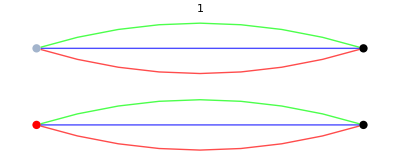
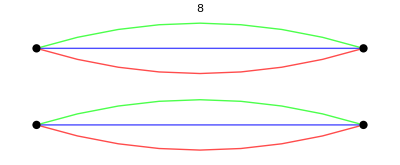
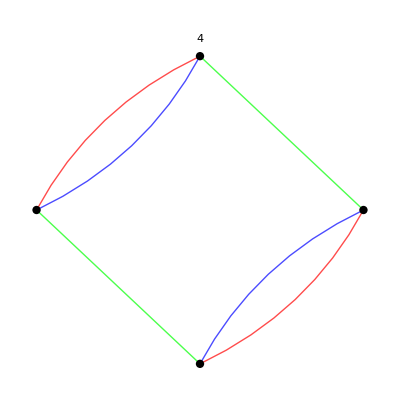
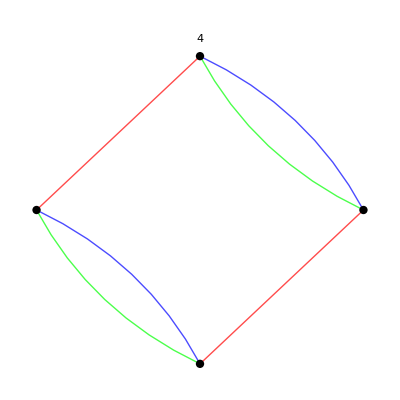
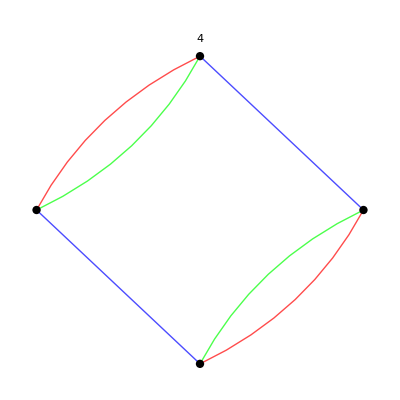
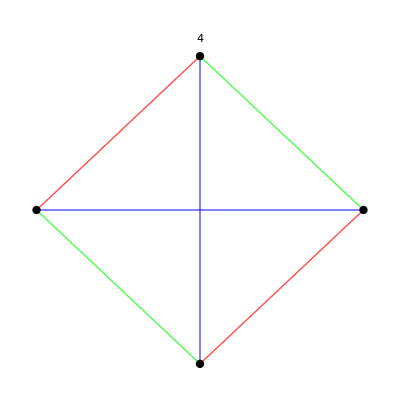
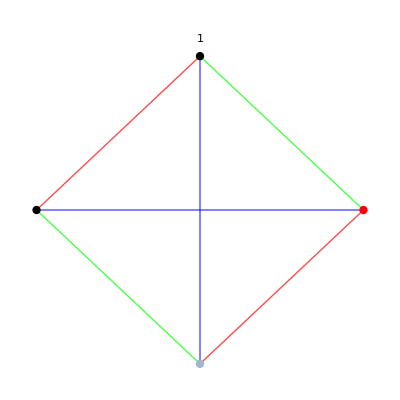
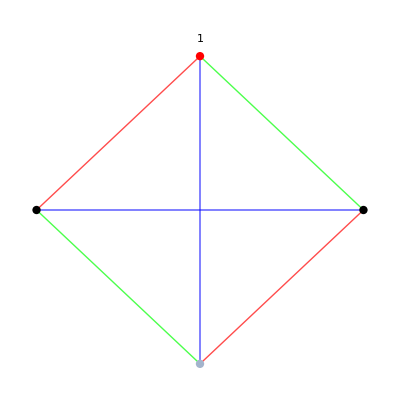
λd_D J(-Graphics-/N^3)+gd J(-Graphics-/N^3)+gp J(-Graphics-/(3 N^2)+-Graphics-/(3 N^2)+-Graphics-/(3 N^2))+gt J(-Graphics-/N^(3/2))+λt J(-Graphics-/(3 N^(3/2))+-Graphics-/(3 N^(3/2))+-Graphics-/(3 N^(3/2)))+λd_S J(-Graphics-/N^3)+λp_ⅇ J(-Graphics-/(3 N^2)+-Graphics-/(3 N^2)+-Graphics-/(3 N^2))+λp_O J(-Graphics-/(3 N^2)+-Graphics-/(3 N^2)+-Graphics-/(3 N^2))+λp_S J(-Graphics-/(3 N^2)+-Graphics-/(3 N^2)+-Graphics-/(3 N^2))

Sub to scalar rule: {N→1,λt→λ/12,λp_ⅇ→λ/12,λp_S→λ/12,λp_O→λ/12,λd_S→λ/12,λd_D→λ/12,gt→g/72,gp→g/72,gd→g/72}. Using it on the potential, we obtain:g/24+λ/2

```mathematica
(********************************************************************************************************)
(*********************************Lagrangian calculation*************************************************)
colPermGroupedVerticesToSFs=Thread/@{
		{λ[1], λ[2], λ[3]}->λt N^(-3/2)/3,
		{λ[4], λ[5], λ[6]}->Subscript[λp, E] N^-2/3,
		{λ[7], λ[8], λ[9]}->Subscript[λp, S] N^-2/3,
		{λ[10], λ[11], λ[12]}->Subscript[λp, O] N^-2/3,
		{λ[13]}->Subscript[λd, S] N^-3,{λ[14]}->Subscript[λd, D] N^-3,

		{g[1]}->gt N^(-3/2),
		{g[2],g[3], g[4]}->gp N^-2/3,
		{g[5]} -> gd N^-3
};

colPermIncProps = Thread/@{
		{ϕϕ[1]}->1, {ψψ[1]}->1		
};
couplingConstantsAssoc = <|λ->{λt ,Subscript[λp, E] ,Subscript[λp, S],Subscript[λp, O],Subscript[λd, S],Subscript[λd, D]}, g->{gt, gp, gd}|>;
couplingConstants=Join@@Values[couplingConstantsAssoc];
kineticParamsAssoc = <|ϕϕ->m, ψψb->M|>;
kineticParams = Values[kineticParamsAssoc];
AbortAssert[#[[1]][[1]]&/@#&/@colPermGroupedVerticesToSFs == Join[coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[λ]])/.reduceHooks, vertexData[λ]], coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[g]])/.reduceHooks,  vertexData[g]]]];

(*This is the assignment of N scalings to the various vertices; we use the same coupling constant for each colour permutation, by symmetry*)
verticesToSFs = Join@@colPermGroupedVerticesToSFs;
verticesExponent = Exponent[#, N]&/@Association[verticesToSFs];
allObjectExponents = Association[verticesExponent, <|ϕϕ[1]->0, ψψb[1]->0|>];

everyColPermOfEveryVtx = Join@@(Values[everyPossibleVertexInFullForm[#]]&/@Keys[couplingConstantsAssoc]);
AbortAssert[Values[-2 * verticesExponent] == (#[[3]]&/@everyColPermOfEveryVtx), "Using the properties of Associations, check that -2* the vertex exponent = the # of coloured faces from fetchVertices."];
Print["Vertex factor assignment (no symmetry factors will be added): ", verticesToSFs];
Print["The powers of N associated to each vertex are as follows: ", verticesExponent];
AbortAssert[(1/(Values[verticesToSFs]/.N->1)/.Power[_,_]->1 )===Join[((Sequence@@ConstantArray[#, #]) & /@( Length[First[#]]&/@Join[fetchVertices[vertexData[λ]], fetchVertices[vertexData[g]]]))], "Ensure that we are dividing each one by the number of colour permutations; thus we average over colour permutations."];

potential =Total@Values[MapThread[(#2[[1]]->Graph[#1[[1]]]  #2[[2]] )&, {everyColPermOfEveryVtx, Normal@verticesToSFs}]];
Collect[potential, couplingConstants,J]

subToScalar = {N->1,Sequence@@Thread[couplingConstantsAssoc[λ]->1/(Length[couplingConstantsAssoc[λ]]2)λ],Sequence@@Thread[couplingConstantsAssoc[g]->1/(Length[couplingConstantsAssoc[g]]4!)g]};

potential2 =Total@Values[MapThread[(#2[[1]]->(1)*  #2[[2]] )&, {Join[everyColPermOfEveryVtx], Normal@verticesToSFs}]];
potential2/.subToScalar;
Print["Sub to scalar rule: ", subToScalar, ". Using it on the potential, we obtain:", potential2/.subToScalar];
```

```mathematica
verticesToSFs
```

{λ(1)→λt/(3 N^(3/2)),λ(2)→λt/(3 N^(3/2)),λ(3)→λt/(3 N^(3/2)),λ(4)→λp_ⅇ/(3 N^2),λ(5)→λp_ⅇ/(3 N^2),λ(6)→λp_ⅇ/(3 N^2),λ(7)→λp_S/(3 N^2),λ(8)→λp_S/(3 N^2),λ(9)→λp_S/(3 N^2),λ(10)→λp_O/(3 N^2),λ(11)→λp_O/(3 N^2),λ(12)→λp_O/(3 N^2),λ(13)→λd_S/N^3,λ(14)→λd_D/N^3,g(1)→gt/N^(3/2),g(2)→gp/(3 N^2),g(3)→gp/(3 N^2),g(4)→gp/(3 N^2),g(5)→gd/N^3}

```mathematica
NotebookEvaluate[FileNameJoin[{homePath,"colourisingDiagrams.m"}]];
```

```mathematica
zeroLoopData =<||>
```

<||>

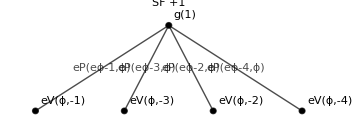

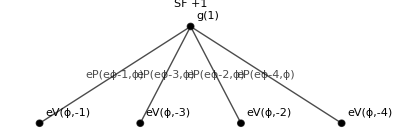
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {g(1)}=> number of bubble options Times@@{5}=5. Now applying every possible bubble:

Large N corrections for g at 0L, diagram 1: <|{g(1)(3)}→(4 gt)/N^(3/2),{g(1)(4)}→(4 gt)/N^(3/2),{g(1)(1)}→(4 gt)/N^(3/2),{g(1)(2)}→(4 gt)/N^(3/2),{g(1)(6)}→(4 gt)/N^(3/2),{g(1)(5)}→(4 gt)/N^(3/2),{g(2)(3)}→(4 gp)/(3 N^2),{g(2)(4)}→(4 gp)/(3 N^2),{g(2)(1)}→(4 gp)/(3 N^2),{g(2)(2)}→(4 gp)/(3 N^2),{g(2)(6)}→(4 gp)/(3 N^2),{g(2)(5)}→(4 gp)/(3 N^2),{g(3)(3)}→(4 gp)/(3 N^2),{g(3)(4)}→(4 gp)/(3 N^2),{g(3)(1)}→(4 gp)/(3 N^2),{g(3)(2)}→(4 gp)/(3 N^2),{g(3)(6)}→(4 gp)/(3 N^2),{g(3)(5)}→(4 gp)/(3 N^2),{g(4)(3)}→(4 gp)/(3 N^2),{g(4)(4)}→(4 gp)/(3 N^2),{g(4)(1)}→(4 gp)/(3 N^2),{g(4)(2)}→(4 gp)/(3 N^2),{g(4)(6)}→(4 gp)/(3 N^2),{g(4)(5)}→(4 gp)/(3 N^2),{g(5)(1)}→(8 gd)/N^3,{g(5)(3)}→(8 gd)/N^3,{g(5)(2)}→(8 gd)/N^3|> times diagWithoutAbsSF(g,0,1)

```mathematica
thisGraphResult ={g,0};
allPossibleGraphsForg ={Graph[{UndirectedEdge[eV[ϕ,-1],g[1],eP["eϕ-1",ϕ]],UndirectedEdge[eV[ϕ,-3],g[1],eP["eϕ-3",ϕ]],UndirectedEdge[eV[ϕ,-2],g[1],eP["eϕ-2",ϕ]],UndirectedEdge[eV[ϕ,-4],g[1],eP["eϕ-4",ϕ]]},{BaseStyle->{GrayLevel[0]},EdgeLabels->{"EdgeTag"},GraphLayout->{"Dimension"->2},ImageSize->Medium,PlotLabel->"SF +1",VertexLabels->{"Name"},VertexStyle->{g[1]->GrayLevel[0]}}]}
symFacs= {1};
zeroLoopData[thisGraphResult] = getNCorrectionsSerialMemSave[#, allPossibleGraphsForg,symFacs,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 1;
```

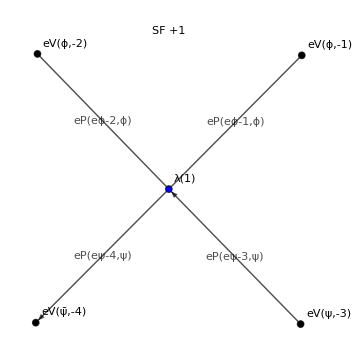

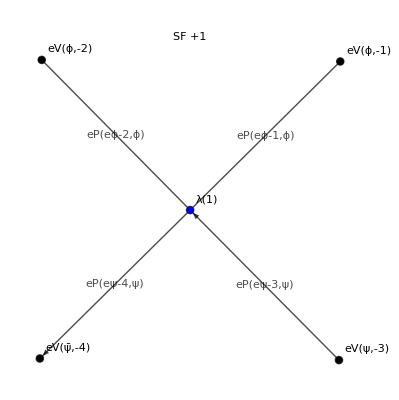
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {λ(1)}=> number of bubble options Times@@{14}=14. Now applying every possible bubble:

Large N corrections for λ at 0L, diagram 1: <|{λ(1)(2)}→λt/(3 N^(3/2)),{λ(1)(1)}→λt/(3 N^(3/2)),{λ(2)(2)}→λt/(3 N^(3/2)),{λ(2)(1)}→λt/(3 N^(3/2)),{λ(3)(2)}→λt/(3 N^(3/2)),{λ(3)(1)}→λt/(3 N^(3/2)),{λ(4)(2)}→λp_ⅇ/(3 N^2),{λ(4)(1)}→λp_ⅇ/(3 N^2),{λ(5)(2)}→λp_ⅇ/(3 N^2),{λ(5)(1)}→λp_ⅇ/(3 N^2),{λ(6)(2)}→λp_ⅇ/(3 N^2),{λ(6)(1)}→λp_ⅇ/(3 N^2),{λ(7)(2)}→λp_S/(3 N^2),{λ(7)(1)}→λp_S/(3 N^2),{λ(8)(2)}→λp_S/(3 N^2),{λ(8)(1)}→λp_S/(3 N^2),{λ(9)(2)}→λp_S/(3 N^2),{λ(9)(1)}→λp_S/(3 N^2),{λ(10)(2)}→λp_O/(3 N^2),{λ(10)(1)}→λp_O/(3 N^2),{λ(11)(2)}→λp_O/(3 N^2),{λ(11)(1)}→λp_O/(3 N^2),{λ(12)(2)}→λp_O/(3 N^2),{λ(12)(1)}→λp_O/(3 N^2),{λ(13)(1)}→(2 λd_S)/N^3,{λ(14)(2)}→λd_D/N^3,{λ(14)(1)}→λd_D/N^3|> times diagWithoutAbsSF(λ,0,1)

```mathematica
thisGraphResult ={λ,0};
allPossibleGraphsForLam ={Graph[{UndirectedEdge[eV[ϕ,-1],λ[1],eP["eϕ-1",ϕ]],DirectedEdge[eV[ψ,-3],λ[1],eP["eψ-3",ψ]],UndirectedEdge[eV[ϕ,-2],λ[1],eP["eϕ-2",ϕ]],DirectedEdge[λ[1],eV[OverBar[ψ],-4],eP["eψ-4",ψ]]},{BaseStyle->{GrayLevel[0]},EdgeLabels->{"EdgeTag"},GraphLayout->{"Dimension"->2},ImageSize->Medium,PlotLabel->"SF +1",VertexLabels->{"Name"},VertexStyle->{λ[1]->RGBColor[0,0,1]}}]}
symFacs= {1};
zeroLoopData[thisGraphResult] = getNCorrectionsSerialMemSave[#, allPossibleGraphsForLam,symFacs,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 1;
```

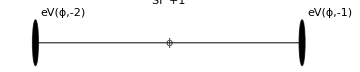

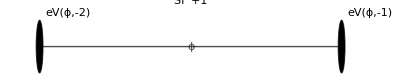
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {}=> number of bubble options Times@@{}=1. Now applying every possible bubble:

Large N corrections for ϕϕ at 0L, diagram 1: <|{ϕϕ(1)(1)}→1|> times diagWithoutAbsSF(ϕϕ,0,1)

```mathematica
thisGraphResult ={ϕϕ,0};
allPossibleGraphsForPhiPhi = {Graph[{UndirectedEdge[eV[ϕ,-1],eV[ϕ,-2],ϕ]},{BaseStyle->{GrayLevel[0]},EdgeLabels->{"EdgeTag"},GraphLayout->{"Dimension"->2},ImageSize->Medium,PlotLabel->"SF +1",VertexLabels->{"Name"},VertexStyle->{}}]}
symFacs= {1};
zeroLoopData[thisGraphResult] = getNCorrectionsSerialMemSave[#, allPossibleGraphsForPhiPhi,symFacs,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 1;
```

```mathematica
(*This is not a problem - note that we have divided through already by the automorphism group arising from the permutation of the graphs*)
```

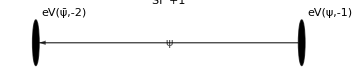

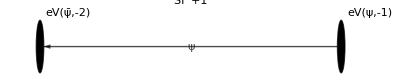
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {}=> number of bubble options Times@@{}=1. Now applying every possible bubble:

Large N corrections for ψψb at 0L, diagram 1: <|{ψψb(1)(1)}→1|> times diagWithoutAbsSF(ψψb,0,1)

```mathematica
thisGraphResult ={ψψb,0};
allPossibleGraphsForPsiPsib = {Graph[{DirectedEdge[eV[ψ,-1],eV[OverBar[ψ],-2],ψ]},{BaseStyle->{GrayLevel[0]},EdgeLabels->{"EdgeTag"},GraphLayout->{"Dimension"->2},ImageSize->Medium,PlotLabel->"SF +1",VertexLabels->{"Name"},VertexStyle->{}}]}
symFacs= {1};
zeroLoopData[thisGraphResult] = getNCorrectionsSerialMemSave[#, allPossibleGraphsForPsiPsib,symFacs,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @1;
```

```mathematica
zeroLoopDiagramEvals = <|diagWithoutAbsSF[g,0,1]->-I g(1+ ct dZgam Ignore),diagWithoutAbsSF[λ,0,1]->-I λ(1+ ct  dZla Ignore),diagWithoutAbsSF[ϕϕ,0,1]-> Ignorect I(dZϕ2 p^2 - (dZmϕ2)m^2),diagWithoutAbsSF[ψψb,0,1]->Ignore ct (I dZψ2 DiracGamma[Momentum[p,D],D]-I dZMψ2)|>
(*Ignore this; it is vestigial for our purposes*)
```

<|diagWithoutAbsSF(g,0,1)→-ⅈ g (ct dZgam Ignore+1),diagWithoutAbsSF(λ,0,1)→-ⅈ λ (ct dZla Ignore+1),diagWithoutAbsSF(ϕϕ,0,1)→ⅈ Ignorect (dZϕ2 p^2-dZmϕ2 m^2),diagWithoutAbsSF(ψψb,0,1)→ct Ignore (ⅈ dZψ2 γ·p-ⅈ dZMψ2)|>

```mathematica
thisGraphResult ={ψψb,1};
{allPossibleGraphs,divergentGraphIndices,justResDNoSFs,recipSFsNoFermionSigns}=getDiagramsResDSFs[dataToFullLocations[thisGraphResult] ];
```

Input details: output='output-qgraf.xml';style='xmldraw.sty';model='/home/f/fraser-taliente/bin/QGRAF/Models/P2PsPsbL4';in=psi;out=psi;loops=1;loop_momentum=;options=onepi;, so model: {/home/f/fraser-taliente/bin/QGRAF/Models/P2PsPsbL4}

<|ϕ^4→g,ψ ϕ^2 ψ̄→λ,ϕ^2→ϕϕ,ψ ψ̄→ψψb|>

1 diagrams found in the input file.. The 0 graphs {} are divergent and will contribute to renormalisation.

Symmetry factors, extracted vs calculated: {2} and {2}

There are in fact 0 graphs total

```mathematica
(*thisGraphResult ={λ,3};
{allPossibleGraphs,divergentGraphIndices,justResDNoSFs,recipSFsNoFermionSigns}=getDiagramsResDSFs[dataToFullLocations[thisGraphResult] ];

resultTestNormal = getNCorrectionsSerialMemSave[#,  allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& /@ Range[6]//EchoTiming;
KeySort@resultTestNormal*)
```

```mathematica
thisOne=1;
thisGraphResult ={ψψb,1};
workThisGraph=allPossibleGraphs[[thisOne]];
internalVertices=Select[VertexList[workThisGraph], !(Head[#]===eV)&]; (*e.g. {λ[1], λ[2], g[3]*)
(*Identify what bubbles we are substituting for those internalVertices*)
listOfBubblesToTry=Tuples[Keys[everyPossibleVertexInFullForm[Head[#]]]&/@internalVertices];
startPoint=1;
maxToDo=-1;
explodedWorkingGraph=explodeTheseVertices[workThisGraph, internalVertices,vertexData];
```

```mathematica
explodedWorkingGraph
```

MyGraph({bO(ϕ(1),λ(1))bO(ϕ(2),λ(1))ϕ,eV(ψ,-1)bO(ψ̄(4),λ(1))ψ,bO(ψ(3),λ(1))eV(ψ̄,-2)ψ})

```mathematica
allVertexResults =MapProgress[ (explodeAndGetExternalContractionsFaster[explodedWorkingGraph,internalVertices,#])&,listOfBubblesToTry[[startPoint;;maxToDo]]]//EchoTiming(*//RuntimeTools`Profile*); 
(*allVertexResults =Map[ (explodeAndGetExternalContractionsFaster[explodedWorkingGraph,internalVertices,#])&,listOfBubblesToTry[[startPoint;;maxToDo]]]//EchoTiming(*//RuntimeTools`Profile*); allVertexResults =Map[ (explodeAndGetExternalContractionsFaster[explodedWorkingGraph,internalVertices,listOfBubblesToTry[[1]]])&,listOfBubblesToTry[[startPoint;;maxToDo]]]//EchoTiming(*//RuntimeTools`Profile*); 
*)
```

0.112382

```mathematica
allVRs2 = identifyMatchingExtBubbleHookPermForFlat[allVertexResults, thisGraphResult[[1]], listOfBubblesToTry[[startPoint;;maxToDo]]];
```

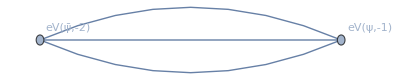
{{-Graphics-,N},1}

```mathematica
allVertexResults[[1,2]]
```

```mathematica
possibleMatches=  everyPossibleColAndHookPermOfVtx[λ];
	canonicalELToKey = Association@KeyValueMap[#2[[1]]-> #1 &, possibleMatches];
```

canonicalELToKey

```mathematica
allVRs2[[1,2]]
```

{{Missing[KeyAbsent,{eV(ψ,-3)eV(ψ̄,-4)RGBColor[1, 0, 0],eV(ψ,-3)ϕ(1)RGBColor[0, 0, 1],eV(ψ,-3)ϕ(2)RGBColor[0, 1, 0],eV(ψ̄,-4)ϕ(1)RGBColor[0, 1, 0],eV(ψ̄,-4)ϕ(2)RGBColor[0, 0, 1],ϕ(1)ϕ(2)RGBColor[1, 0, 0]}]},1,{λ(1)}}

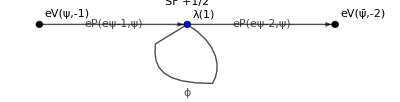
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {λ(1)}=> number of bubble options Times@@{14}=14. Now applying every possible bubble:

Large N corrections for ψψb at 1L, diagram 1: <|{ψψb(1)(1)}→1/2 (2 λd_S+2 λp_ⅇ)+O(√(1/N))|> times diagWithoutAbsSF(ψψb,1,1)

```mathematica
resultTestNormal = getNCorrectionsSerialMemSave[#,  allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 1//AbsoluteTiming;
```

```mathematica
(*
resultTestNormal = getNCorrections[#, allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 100//AbsoluteTiming;
resultTestSerial = getNCorrectionsSerial[#, allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]& @ 100//AbsoluteTiming*)
```

```mathematica
doParallel=True; (*This is a global variable*)
oPrint=List;
gResult= getAllPossibleGraphsAndSFs[{λ,2},subToScalar, allObjectExponents,dataToFullLocations];
oPrint=Print;
```

numLoops>= 2, so just divergents:

Large N corrections for λ at 2L, diagram 16: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(4)(2)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(5)(1)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(5)(2)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(6)(1)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(6)(2)}→(λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(7)(1)}→O((1/N)^3),{λ(7)(2)}→O((1/N)^3),{λ(8)(1)}→O((1/N)^3),{λ(8)(2)}→O((1/N)^3),{λ(9)(1)}→O((1/N)^3),{λ(9)(2)}→O((1/N)^3),{λ(10)(1)}→O((1/N)^4),{λ(10)(2)}→O((1/N)^4),{λ(11)(1)}→O((1/N)^4),{λ(11)(2)}→O((1/N)^4),{λ(12)(1)}→O((1/N)^4),{λ(12)(2)}→O((1/N)^4),{λ(13)(1)}→(2 (3 λd_S λt^2+2 λp_ⅇ λt^2))/(9 N^3)+O((1/N)^6),{λ(14)(1)}→O((1/N)^4),{λ(14)(2)}→O((1/N)^4)|> times diagWithoutAbsSF(λ,2,16)

Large N corrections for λ at 2L, diagram 17: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→O((1/N)^3),{λ(4)(2)}→O((1/N)^4),{λ(5)(1)}→O((1/N)^3),{λ(5)(2)}→O((1/N)^4),{λ(6)(1)}→O((1/N)^3),{λ(6)(2)}→O((1/N)^4),{λ(7)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(7)(2)}→O((1/N)^4),{λ(8)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(8)(2)}→O((1/N)^4),{λ(9)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(9)(2)}→O((1/N)^4),{λ(10)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(10)(2)}→O((1/N)^3),{λ(11)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(11)(2)}→O((1/N)^3),{λ(12)(1)}→O((1/N)^3),{λ(12)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(13)(1)}→O((1/N)^4),{λ(14)(1)}→(2 (3 λd_D λt^2+2 λp_O λt^2+2 λp_S λt^2))/(9 N^3)+O((1/N)^6),{λ(14)(2)}→O((1/N)^4)|> times diagWithoutAbsSF(λ,2,17)

Large N corrections for λ at 2L, diagram 20: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→O((1/N)^3),{λ(4)(2)}→O((1/N)^4),{λ(5)(1)}→O((1/N)^3),{λ(5)(2)}→O((1/N)^4),{λ(6)(1)}→O((1/N)^3),{λ(6)(2)}→O((1/N)^4),{λ(7)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(7)(2)}→O((1/N)^4),{λ(8)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(8)(2)}→O((1/N)^4),{λ(9)(1)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(9)(2)}→O((1/N)^4),{λ(10)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(10)(2)}→O((1/N)^3),{λ(11)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(11)(2)}→O((1/N)^3),{λ(12)(1)}→O((1/N)^3),{λ(12)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(13)(1)}→O((1/N)^4),{λ(14)(1)}→(2 (3 λd_D λt^2+2 λp_O λt^2+2 λp_S λt^2))/(9 N^3)+O((1/N)^6),{λ(14)(2)}→O((1/N)^4)|> times diagWithoutAbsSF(λ,2,20)

Large N corrections for λ at 2L, diagram 22: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(4)(2)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(5)(1)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(5)(2)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(6)(1)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(6)(2)}→(2 λt^2 λp_ⅇ)/(27 N^2)+O((1/N)^5),{λ(7)(1)}→O((1/N)^3),{λ(7)(2)}→O((1/N)^3),{λ(8)(1)}→O((1/N)^3),{λ(8)(2)}→O((1/N)^3),{λ(9)(1)}→O((1/N)^3),{λ(9)(2)}→O((1/N)^3),{λ(10)(1)}→O((1/N)^4),{λ(10)(2)}→O((1/N)^4),{λ(11)(1)}→O((1/N)^4),{λ(11)(2)}→O((1/N)^4),{λ(12)(1)}→O((1/N)^4),{λ(12)(2)}→O((1/N)^4),{λ(13)(1)}→((4 λd_S λt^2)/3+(8 λp_ⅇ λt^2)/9)/N^3+O((1/N)^6),{λ(14)(1)}→O((1/N)^4),{λ(14)(2)}→O((1/N)^4)|> times diagWithoutAbsSF(λ,2,22)

Large N corrections for λ at 2L, diagram 24: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→O((1/N)^4),{λ(4)(2)}→O((1/N)^3),{λ(5)(1)}→O((1/N)^4),{λ(5)(2)}→O((1/N)^3),{λ(6)(1)}→O((1/N)^4),{λ(6)(2)}→O((1/N)^3),{λ(7)(1)}→O((1/N)^4),{λ(7)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(8)(1)}→O((1/N)^4),{λ(8)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(9)(1)}→O((1/N)^4),{λ(9)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(10)(1)}→O((1/N)^3),{λ(10)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(11)(1)}→O((1/N)^3),{λ(11)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(12)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(12)(2)}→O((1/N)^3),{λ(13)(1)}→O((1/N)^4),{λ(14)(1)}→O((1/N)^4),{λ(14)(2)}→(2 (3 λd_D λt^2+2 λp_O λt^2+2 λp_S λt^2))/(9 N^3)+O((1/N)^6)|> times diagWithoutAbsSF(λ,2,24)

Large N corrections for λ at 2L, diagram 14: <|{λ(1)(1)}→O((1/N)^(5/2)),{λ(1)(2)}→O((1/N)^(5/2)),{λ(2)(1)}→O((1/N)^(5/2)),{λ(2)(2)}→O((1/N)^(5/2)),{λ(3)(1)}→O((1/N)^(5/2)),{λ(3)(2)}→O((1/N)^(5/2)),{λ(4)(1)}→O((1/N)^4),{λ(4)(2)}→O((1/N)^3),{λ(5)(1)}→O((1/N)^4),{λ(5)(2)}→O((1/N)^3),{λ(6)(1)}→O((1/N)^4),{λ(6)(2)}→O((1/N)^3),{λ(7)(1)}→O((1/N)^4),{λ(7)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(8)(1)}→O((1/N)^4),{λ(8)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(9)(1)}→O((1/N)^4),{λ(9)(2)}→(2 λt^2 λp_O)/(27 N^2)+O((1/N)^5),{λ(10)(1)}→O((1/N)^3),{λ(10)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(11)(1)}→O((1/N)^3),{λ(11)(2)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(12)(1)}→(2 λt^2 λp_S)/(27 N^2)+O((1/N)^5),{λ(12)(2)}→O((1/N)^3),{λ(13)(1)}→O((1/N)^4),{λ(14)(1)}→O((1/N)^4),{λ(14)(2)}→(2 (3 λd_D λt^2+2 λp_O λt^2+2 λp_S λt^2))/(9 N^3)+O((1/N)^6)|> times diagWithoutAbsSF(λ,2,14)

```mathematica
(*gResult >> "~/Downloads/gResult.out";*)
```

```mathematica
(*(*What if we remove all the tets: what happens? Observe the graphs that continue to contribute: they should all be non-divergent.*)
noTets = Normal[#,Association]&/@gResult/.gt->0/.λt->0//FullSimplify;
whichDiagIdxsAppear =Union@Cases[gResult, diagWithoutAbsSF[_, _, diagNum_]->diagNum,∞] ;
allPossibleGraphs[[#]]&/@whichDiagIdxsAppear;
whichDiagIdxsAppear*)
```

```mathematica
oPrint=List;
thisGraphResult ={λ,3};
{allPossibleGraphs,divergentGraphIndices,justResDNoSFs,recipSFsNoFermionSigns}=getDiagramsResDSFs[dataToFullLocations[thisGraphResult] ];
```

resD does not exist. Use Lists/degreeOfDiv.out instead.

NB - only superficial divergence here: , {-1,0,-3,-1,-1,-1,0,0,-3,-1,-1,0,0,-2,0,-3,-1,0,-2,0,0,-1,-1,-3,-3,-1,-1,0,-1,-1,0,-1,-1,-3,-3,-1,-1,0,-1,-1,-1,-1,-2,-2,0,-3,-3,-1,-1,-1,-2,-2,0,-1,-1,-3,-3,-3,-1,-1,0,-2,-2,-2,-2,-3,-3,-3,-3,0,-2,-2,-2,-2,-1,0,-2,-1,0,0,-1,-1,0,-3,-1,-1,-1,-1,0,3,3,4,3,3,4,2,3,2,2,4,2,2,4,3,4,2,3,3,3,4,3,3,3,4,3,3,4,2,3,1,2,3,3,1,2,3,3,3,3,4,3,3,4,2,3,0,1,2,1,1,2,0,2,0,1,2,-1,1,0,0,1,2,1,1,1,2,0,0,0,0,2,0,0,2,2,0,0,1,1,1,1,1,1,2,0,0,-1,-1,0,0,-1,-1,0,0,1,1,1,2,0,0,2,2,3,3,3,3,2,2,3,3,3,3,3,2,2,2,2,3,3,3,1,1,2,2,2,2,3,3,3,-1,1,2,1,2,0,2,1,1,0,2,2,0,2,2,1,1,0,2}. The superficially divergent diagrams are {2,7,8,12,13,15,18,20,21,28,31,38,45,53,61,70,76,79,80,83,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,179,180,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238}

```mathematica
(*allPossibleGraphs[[#]]&/@Intersection[NLeadingDiagsglam3, divDiagslam3]*)
```

```mathematica
(*thisOne=20;
oPrint=List;
testRun = MapProgress[getNCorrections[#, allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents]&,Range@Length@allPossibleGraphs];
oPrint=Print;*)
```

```mathematica
(*(*What if we remove all the tets: what happens? Observe the graphs that continue to contribute: they should all be non-divergent.*)
noTets = Normal/@testRun/.gt->0/.λt->0//FullSimplify;
whichDiagsAppear =allPossibleGraphs[[#]]&/@Cases[noTets, diagWithoutAbsSF[_, _, diagNum_]->diagNum,∞] ;
Style[whichDiagsAppear,Smaller]*)
```

```mathematica
(****************************************************************************************************************)
(*Now testing everything together:*)
```

```mathematica
(*Print["Doing divergentGraphIndices: ", divergentGraphIndices];
thisEvaluated= getNCorrections[16,allPossibleGraphs,recipSFsNoFermionSigns,thisGraphResult[[1]],thisGraphResult[[2]], subToScalar,allObjectExponents];*)
```

***********Recovering scalar diagrams for ϕϕ at 2 loops  in /home/f/fraser-taliente/dphil/FMout/P2PsPsbL4/Processes/2-phiphi**********************

Input details: output='output-qgraf.xml';style='xmldraw.sty';model='/home/f/fraser-taliente/bin/QGRAF/Models/P2PsPsbL4';in=phi;out=phi;loops=2;loop_momentum=;options=onepi;, so model: {/home/f/fraser-taliente/bin/QGRAF/Models/P2PsPsbL4}

<|ϕ^4→g,ϕ^2 ψ ψ̄→λ,ϕ^2→ϕϕ,ψ ψ̄→ψψb|>

5 diagrams found in the input file.. The 1 graphs {5} are divergent and will contribute to renormalisation.

Fermion signs detected, so SF mapping to remove signs: {1/4,-1/2,-1/2,1/6,-1}->{1/4,1/2,1/2,1/6,1}

Symmetry factors, extracted vs calculated: {4,2,2,6,1} and {4,2,2,6,1}

This is a selection of the 0 divergent diagrams with |symmetry factor|=/=1: {}

All graphs

********************** Beginning calculation of diagrams: **********************

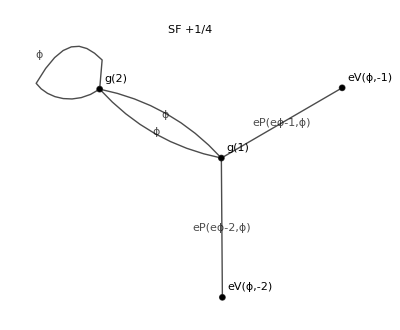
*** Doing diagram 1→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {g[2],g[1]}=> number of bubble options Times@@{5,5}=25. Now applying every possible bubble:

Done in 0.324814s. Identifying external contractions for each...

Done in 0.011166s. For example, we have {0,{ϕϕ[1][1]},64 gd^2} for a case of bubbles {g[5],g[5]}.

If we set N=1, and apply substituteToNeq, then 1/4 g^2 diagWithoutAbsSF[ϕϕ,2,1]: should match graph symmetry factor.

Large N corrections for ϕϕ at 2L, diagram 1: <|{ϕϕ[1][1]}→1/4 (64 gd^2+128 gd gp+64 gp^2)|> times diagWithoutAbsSF[ϕϕ,2,1]

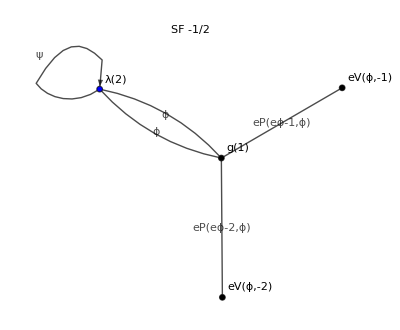
*** Doing diagram 2→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {λ[2],g[1]}=> number of bubble options Times@@{14,5}=70. Now applying every possible bubble:

Done in 0.329129s. Identifying external contractions for each...

Done in 0.011152s. For example, we have {0,{ϕϕ[1][1]},(8 gd λd_D)/N^3} for a case of bubbles {λ[14],g[5]}.

If we set N=1, and apply substituteToNeq, then 1/2 g λ diagWithoutAbsSF[ϕϕ,2,2]: should match graph symmetry factor.

Large N corrections for ϕϕ at 2L, diagram 2: <|{ϕϕ[1][1]}→1/2 (16 gd λd_S+16 gp λd_S+16 gd λp_ⅇ+16 gp λp_ⅇ)|> times diagWithoutAbsSF[ϕϕ,2,2]

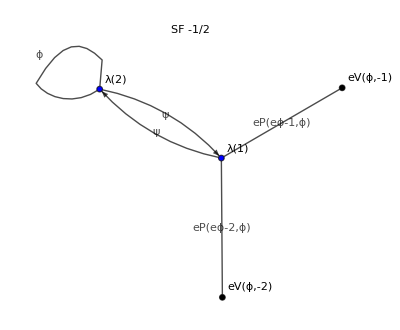
*** Doing diagram 3→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {λ[2],λ[1]}=> number of bubble options Times@@{14,14}=196. Now applying every possible bubble:

Done in 0.336858s. Identifying external contractions for each...

Done in 0.01135s. For example, we have {0,{ϕϕ[1][1]},λd_D^2/N^6} for a case of bubbles {λ[14],λ[14]}.

If we set N=1, and apply substituteToNeq, then 1/2 λ^2 diagWithoutAbsSF[ϕϕ,2,3]: should match graph symmetry factor.

Large N corrections for ϕϕ at 2L, diagram 3: <|{ϕϕ[1][1]}→1/2 (4 λd_S^2+8 λd_S λp_ⅇ+4 λp_ⅇ^2)|> times diagWithoutAbsSF[ϕϕ,2,3]

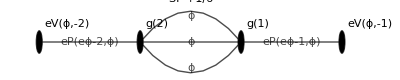
*** Doing diagram 4→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {g[2],g[1]}=> number of bubble options Times@@{5,5}=25. Now applying every possible bubble:

Done in 0.300807s. Identifying external contractions for each...

Done in 0.010895s. For example, we have {0,{ϕϕ[1][1]},(64 gd^2)/N^3} for a case of bubbles {g[5],g[5]}.

If we set N=1, and apply substituteToNeq, then 1/6 g^2 diagWithoutAbsSF[ϕϕ,2,4]: should match graph symmetry factor.

Large N corrections for ϕϕ at 2L, diagram 4: <|{ϕϕ[1][1]}→16 gt^2|> times diagWithoutAbsSF[ϕϕ,2,4]

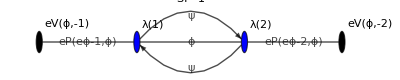
*** Doing diagram 5→-Graphics-. NB: ensure that this graph only has automorphisms due to vertex hook permutation and propagator permutation!

Internal vertices: {λ[2],λ[1]}=> number of bubble options Times@@{14,14}=196. Now applying every possible bubble:

Done in 0.329027s. Identifying external contractions for each...

Done in 0.011239s. For example, we have {0,{ϕϕ[1][1]},λd_D^2/N^6} for a case of bubbles {λ[14],λ[14]}.

If we set N=1, and apply substituteToNeq, then λ^2 diagWithoutAbsSF[ϕϕ,2,5]: should match graph symmetry factor.

Large N corrections for ϕϕ at 2L, diagram 5: <|{ϕϕ[1][1]}→(2 λt^2)/3|> times diagWithoutAbsSF[ϕϕ,2,5]

********************** Calculation of diagrams complete; now merging. Result: <|{ϕϕ[1][1]}→1/4 (64 gd^2+128 gd gp+64 gp^2) diagWithoutAbsSF[ϕϕ,2,1]+16 gt^2 diagWithoutAbsSF[ϕϕ,2,4]+2/3 λt^2 diagWithoutAbsSF[ϕϕ,2,5]+1/2 diagWithoutAbsSF[ϕϕ,2,2] (16 gd λd_S+16 gp λd_S+16 gd λp_ⅇ+16 gp λp_ⅇ)+1/2 diagWithoutAbsSF[ϕϕ,2,3] (4 λd_S^2+8 λd_S λp_ⅇ+4 λp_ⅇ^2)|>

```mathematica
phiphiResult= getAllPossibleGraphsAndSFs[{ϕϕ,2},subToScalar, allObjectExponents,dataToFullLocations];
```

```mathematica
(*doParallel=True;
oPrint=List;
gResult= getAllPossibleGraphsAndSFs[{ϕϕ,3},subToScalar, allObjectExponents,dataToFullLocations];*)
```

```mathematica
possibleLocationsLoopsAndHeads
```

{{ϕϕ,1}→1-phiphi,{ϕϕ,2}→2-phiphi,{ϕϕ,3}→9-phiphi,{ϕϕ,4}→13-phiphi,{ψψb,1}→3-psipsi,{ψψb,2}→4-psipsi,{ψψb,3}→10-psipsi,{ψψb,4}→14-psipsi,{λ,1}→5-phipsiphipsi,{λ,2}→6-phipsiphipsi,{λ,3}→11-phipsiphipsi,{λ,4}→15-phipsiphipsi,{g,1}→7-phiphiphiphi,{g,2}→8-phiphiphiphi,{g,3}→12-phiphiphiphi,{g,4}→16-phiphiphiphi}

```mathematica
locations2Loops  = possibleLocationsLoopsAndHeads[[{1,2,5,6,9,10, 13,14}]]
```

{{ϕϕ,1}→1-phiphi,{ϕϕ,2}→2-phiphi,{ψψb,1}→3-psipsi,{ψψb,2}→4-psipsi,{λ,1}→5-phipsiphipsi,{λ,2}→6-phipsiphipsi,{g,1}→7-phiphiphiphi,{g,2}→8-phiphiphiphi}

```mathematica
doParallel=True;
oPrint=List;fPrint=List;
allOfTheResults = AssociationMap[getAllPossibleGraphsAndSFs[#,subToScalar, allObjectExponents,dataToFullLocations]&, First/@locations2Loops]//EchoTiming;
(*allOfTheResults >> "~/dphil/largeNmodels/data/largeNDivergentCorrectionsForP2PsPsb2Loops.out";*)
oPrint=Print;fPrint=Print;
```

Fri 10 Mar 2023 14:58:15 diag 11

Fri 10 Mar 2023 14:58:15 diag 2

Fri 10 Mar 2023 14:58:15 diag 5

Fri 10 Mar 2023 14:58:15 diag 20

Fri 10 Mar 2023 14:58:15 diag 23

Fri 10 Mar 2023 14:58:15 diag 8

Fri 10 Mar 2023 14:58:16 diag 17

Fri 10 Mar 2023 14:58:16 diag 14

Fri 10 Mar 2023 14:58:20 diag 12

Fri 10 Mar 2023 14:58:21 diag 6

Fri 10 Mar 2023 14:58:21 diag 3

Fri 10 Mar 2023 14:58:21 diag 9

Fri 10 Mar 2023 14:58:21 diag 24

Fri 10 Mar 2023 14:58:21 diag 15

Fri 10 Mar 2023 14:58:22 diag 18

Fri 10 Mar 2023 14:58:22 diag 21

Fri 10 Mar 2023 14:58:26 diag 25

Fri 10 Mar 2023 14:58:27 diag 28

Fri 10 Mar 2023 14:58:27 diag 31

Fri 10 Mar 2023 14:58:27 diag 34

Fri 10 Mar 2023 14:58:27 diag 37

Fri 10 Mar 2023 14:58:28 diag 40

Fri 10 Mar 2023 14:58:29 diag 42

Fri 10 Mar 2023 14:58:29 diag 44

Fri 10 Mar 2023 14:58:33 diag 35

Fri 10 Mar 2023 14:58:33 diag 32

Fri 10 Mar 2023 14:58:33 diag 26

Fri 10 Mar 2023 14:58:33 diag 29

Fri 10 Mar 2023 14:58:34 diag 38

Fri 10 Mar 2023 14:58:34 diag 43

Fri 10 Mar 2023 14:58:35 diag 41

Fri 10 Mar 2023 14:58:36 diag 45

Fri 10 Mar 2023 14:58:39 diag 27

Fri 10 Mar 2023 14:58:39 diag 36

Fri 10 Mar 2023 14:58:40 diag 39

Fri 10 Mar 2023 14:58:40 diag 33

Fri 10 Mar 2023 14:58:40 diag 30

72.4583

```mathematica
(*allOfTheResultsOld= << "/home/f/fraser-taliente/dphil/largeNmodels/data/largeNDivergentCorrectionsForP2PsPsb2Loops.out";*)
```

```mathematica
allOfTheResultsOld= << "/home/f/fraser-taliente/dphil/largeNmodels/data/largeNDivergentCorrectionsForP2PsPsb2Loops.out";
```

```mathematica
allOfTheResults[[1]]
```

{<|{ϕϕ(1)(1)}→2 l (2 (gd+gp) diagWithoutAbsSF(ϕϕ,1,1)+diagWithoutAbsSF(ϕϕ,1,2) (λd_S+λp_ⅇ))+O(√(1/N))|>,{<|{ϕϕ(1)(1)}→1/2 (8 gd+8 gp) diagWithoutAbsSF(ϕϕ,1,1)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→diagWithoutAbsSF(ϕϕ,1,2) (2 λd_S+2 λp_ⅇ)+O(√(1/N))|>}}

```mathematica
allOfTheResults[[1]]
```

{<|{ϕϕ(1)(1)}→2 l (2 (gd+gp) diagWithoutAbsSF(ϕϕ,1,1)+diagWithoutAbsSF(ϕϕ,1,2) (λd_S+λp_ⅇ))+O(√(1/N))|>,{<|{ϕϕ(1)(1)}→1/2 (8 gd+8 gp) diagWithoutAbsSF(ϕϕ,1,1)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→diagWithoutAbsSF(ϕϕ,1,2) (2 λd_S+2 λp_ⅇ)+O(√(1/N))|>}}

```mathematica
allOfTheResultsOld[[5]]
```

{Association[FullSimplify[Normal[finalResult$813385]/.{diagWithoutAbsSF(λ,1,idx$_):>l^1 diagWithoutAbsSF(λ,1,idx$)}]],$Aborted}

```mathematica
(*Merge[{allOfTheResults,allOfTheResultsOld}, Merge[{#[[1,1]],#[[2,1]]},Simplify@Equal[Normal@#[[1]], Normal@#[[2]]]&]&][[8]]*)
```

```mathematica
allOfTheResultsOld =<< "~/dphil/largeNmodels/data/largeNDivergentCorrectionsForP2PsPsb2Loops.out";

Merge[{allOfTheResults,allOfTheResultsOld}, SameQ[#[[1]],#[[2]]]&]
```

Merge::list1: The argument allOfTheResults is not a valid list of Associations or rules or lists of rules.

Merge[{allOfTheResults,<|{ϕϕ,1}→{<|{ϕϕ(1)(1)}→(4 (gd+gp) l diagWithoutAbsSF(ϕϕ,1,1)+2 l diagWithoutAbsSF(ϕϕ,1,2) (λd_S+λp_ⅇ))+O(√(1/N))|>,{<|{ϕϕ(1)(1)}→4 (gd+gp) diagWithoutAbsSF(ϕϕ,1,1)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→2 diagWithoutAbsSF(ϕϕ,1,2) (λd_S+λp_ⅇ)+O(√(1/N))|>}},{ϕϕ,2}→{<|{ϕϕ(1)(1)}→2/3 l^2 (24 diagWithoutAbsSF(ϕϕ,2,1) (gd+gp)^2+24 gt^2 diagWithoutAbsSF(ϕϕ,2,4)+λt^2 diagWithoutAbsSF(ϕϕ,2,5)+3 (λd_S+λp_ⅇ) (4 (gd+gp) diagWithoutAbsSF(ϕϕ,2,2)+diagWithoutAbsSF(ϕϕ,2,3) (λd_S+λp_ⅇ)))+O(√(1/N))|>,{<|{ϕϕ(1)(1)}→16 (gd^2+2 gp gd+gp^2) diagWithoutAbsSF(ϕϕ,2,1)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→8 diagWithoutAbsSF(ϕϕ,2,2) (gd λd_S+gp λd_S+gd λp_ⅇ+gp λp_ⅇ)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→2 diagWithoutAbsSF(ϕϕ,2,3) (λd_S^2+2 λp_ⅇ λd_S+λp_ⅇ^2)+O(√(1/N))|>,<|{ϕϕ(1)(1)}→16 gt^2 diagWithoutAbsSF(ϕϕ,2,4)+O((1/N)^1)|>,<|{ϕϕ(1)(1)}→2/3 λt^2 diagWithoutAbsSF(ϕϕ,2,5)+O((1/N)^1)|>}},{ψψb,1}→{<|{ψψb(1)(1)}→l diagWithoutAbsSF(ψψb,1,1) (λd_S+λp_ⅇ)+O(√(1/N))|>,{<|{ψψb(1)(1)}→diagWithoutAbsSF(ψψb,1,1) (λd_S+λp_ⅇ)+O(√(1/N))|>}},{ψψb,2}→{<|{ψψb(1)(1)}→1/3 l^2 (diagWithoutAbsSF(ψψb,2,3) λt^2+6 (λd_S+λp_ⅇ) (2 (gd+gp) diagWithoutAbsSF(ψψb,2,1)+diagWithoutAbsSF(ψψb,2,2) (λd_S+λp_ⅇ)))+O(√(1/N))|>,{<|{ψψb(1)(1)}→4 diagWithoutAbsSF(ψψb,2,1) (gd λd_S+gp λd_S+gd λp_ⅇ+gp λp_ⅇ)+O(√(1/N))|>,<|{ψψb(1)(1)}→2 diagWithoutAbsSF(ψψb,2,2) (λd_S^2+2 λp_ⅇ λd_S+λp_ⅇ^2)+O(√(1/N))|>,<|{ψψb(1)(1)}→1/3 λt^2 diagWithoutAbsSF(ψψb,2,3)+O((1/N)^1)|>}},{λ,1}→{Association[FullSimplify[Normal[finalResult$813385]/.{diagWithoutAbsSF(λ,1,idx$_):>l^1 diagWithoutAbsSF(λ,1,idx$)}]],$Aborted},{λ,2}→{Association[FullSimplify[Normal[finalResult$813457]/.{diagWithoutAbsSF(λ,2,idx$_):>l^2 diagWithoutAbsSF(λ,2,idx$)}]],$Aborted},{g,1}→{Association[FullSimplify[Normal[finalResult$813721]/.{diagWithoutAbsSF(g,1,idx$_):>l^1 diagWithoutAbsSF(g,1,idx$)}]],$Aborted},{g,2}→{Association[FullSimplify[Normal[finalResult$813822]/.{diagWithoutAbsSF(g,2,idx$_):>l^2 diagWithoutAbsSF(g,2,idx$)}]],$Aborted}|>},#1⟦1⟧===#1⟦2⟧&]

```mathematica
(*allOfTheResults=allOfTheResultsOld;*)
```

```mathematica
couplingConstants//InputForm
```

{λt, Subscript[λp, E], Subscript[λp, S], Subscript[λp, O], Subscript[λd, S], Subscript[λd, D], gt, gp, gd}

```mathematica
resultsFromHydra = Association[Get/@FileNames["runFor*", "~/dphil/largeNmodels/o3results/"]];
```

```mathematica
(*checkResults =Merge[{allOfTheResults,KeyTake[resultsFromHydra, Keys@allOfTheResults]},Merge[{#[[1,1]], #[[2,1]]}, Equal[Normal[#[[1]],Series],Normal[#[[1]],Series]]&]&];
checkResults*)
```

```mathematica
(*resultsFromHydra = Association@MapIndexed[ Get["~/dphil/largeNmodels/o3results/runFor" <> ToString[#2[[1]]]] &, possibleLocationsLoopsAndHeads];
Run["scp -r ludo@hydra:~/dphil/FMout/P2PsPsbL4/large/ /tmp/"];*)
```

```mathematica
(*i=0;
getSafe[type_Symbol, int_,loc_]:=Check[Get[loc],(++i);type[int, 4]-><|failed->failed[type,int]/N|>];
l4results = Association@Map[getSafe[λ,#,"/tmp/large/l"<>ToString[#]<>"result.out"] &,  Range[1,2635]];
Print["Number failed: ", i]

i=0;
getSafe[type_Symbol, int_,loc_]:=Check[Get[loc],(++i);type[int, 4]-><|failed->failed[type,int]/N|>];
g4results = Association@Map[getSafe[g, #, "/tmp/large/g"<>ToString[#]<>"result.out"] &,  Range[1,5478]];
Print["Number failed: ", i]
allg4sTogether = Merge[Values[g4results], Total];
alll4sTogether = Merge[Values[l4results], Total];
*)
(*Put[{g4->allg4sTogether,l4->alll4sTogether}, "~/dphil/largeNmodels/betaFunctions/g4AndL4Merged.out"];*)
```

```mathematica
recovered4L4PtON3=Association@Get["~/dphil/largeNmodels/betaFunctions/g4AndL4Merged.out"];
```

```mathematica
allg4sTogether=recovered4L4PtON3[g4];
alll4sTogether = recovered4L4PtON3[l4];
```

```mathematica
ByteCount/@allg4sTogether
resultsFromHydra[{g,4}] ={allg4sTogether};
resultsFromHydra[{λ,4}] ={alll4sTogether};
```

<|{g(1)(1)}→240,{g(1)(2)}→240,{g(1)(3)}→240,{g(1)(4)}→240,{g(1)(5)}→240,{g(1)(6)}→240,{g(2)(1)}→843424,{g(2)(2)}→843424,{g(2)(3)}→843424,{g(2)(4)}→843424,{g(2)(5)}→843424,{g(2)(6)}→843424,{g(3)(1)}→843424,{g(3)(2)}→843424,{g(3)(3)}→843424,{g(3)(4)}→843424,{g(3)(5)}→843424,{g(3)(6)}→843424,{g(4)(1)}→843424,{g(4)(2)}→843424,{g(4)(3)}→843424,{g(4)(4)}→843424,{g(4)(5)}→843424,{g(4)(6)}→843424,{g(5)(1)}→1429376,{g(5)(2)}→1429376,{g(5)(3)}→1429376|>

```mathematica
(*Old, some missing, ByteCounts: <|{g(1)(1)}->240,{g(1)(2)}->240,{g(1)(3)}->240,{g(1)(4)}->240,{g(1)(5)}->240,{g(1)(6)}->240,{g(2)(1)}->703856,{g(2)(2)}->671792,{g(2)(3)}->703856,{g(2)(4)}->671792,{g(2)(5)}->671792,{g(2)(6)}->671792,{g(3)(1)}->703856,{g(3)(2)}->671792,{g(3)(3)}->703856,{g(3)(4)}->671792,{g(3)(5)}->671792,{g(3)(6)}->671792,{g(4)(1)}->671792,{g(4)(2)}->703856,{g(4)(3)}->671792,{g(4)(4)}->703856,{g(4)(5)}->671792,{g(4)(6)}->671792,{g(5)(1)}->1201304,{g(5)(2)}->1152872,{g(5)(3)}->1152872,failed->303376|>*)
```

```mathematica
Print["Are the obtained remote runs the same as the local runs?"];
KeyValueMap[Normal[resultsFromHydra[#1],Association]===Normal[#2,Association]&, allOfTheResults]
```

Are the obtained remote runs the same as the local runs?

KeyValueMap::invak: The argument allOfTheResults is not a valid Association.

KeyValueMap[Normal[resultsFromHydra(#1),Association]===Normal[#2,Association]&,allOfTheResults]

```mathematica
(*runJustThese = First/@locations2loops
dataForUs= KeyTake[resultsFromHydra,runJustThese];*)
dataForUs=resultsFromHydra;(*KeyDrop[resultsFromHydra, {{ϕϕ, 4}, {ψψb, 4}}];*)
dataForUs[[1]]
whichDiags =Union@Cases[dataForUs, diagWithoutAbsSF[__],Infinity];
Print["How many diagrams: ", Length[whichDiags]];
```

{<|{ϕϕ(1)(1)}→2 l (2 (gd+gp) diagWithoutAbsSF(ϕϕ,1,1)+diagWithoutAbsSF(ϕϕ,1,2) (λp_ⅇ+λd_S))|>,{<|{ϕϕ(1)(1)}→1/2 (8 gd+8 gp) diagWithoutAbsSF(ϕϕ,1,1)|>,<|{ϕϕ(1)(1)}→diagWithoutAbsSF(ϕϕ,1,2) (2 λp_ⅇ+2 λd_S)|>}}

How many diagrams: 4372

```mathematica
sumsForHead =First/@dataForUs;
sumsForHead//Keys
```

(ϕϕ | 1
λ | 2
λ | 3
g | 1
g | 2
g | 3
ϕϕ | 2
ϕϕ | 3
ϕϕ | 4
ψψb | 1
ψψb | 2
ψψb | 3
ψψb | 4
λ | 1
g | 4
λ | 4)

```mathematica
allQGLoopDiagramData = Get["~/dphil/largeNmodels/betaFunctions/qgRoutePhi2PsPsbL4.in"];
allQGLoopDiagramData[{ϕϕ,2}]//Keys
```

{loopIntsToDo,diagsToEvaluateNoSFs,diagsNoSFs,loopsExtractedNoSFs,simpWithSF,traces,initialInserted,fromQG,symFacs,mapDWSFToRepresentative}

```mathematica
allQGLoopDiagramData[{ϕϕ,2}]["diagsToEvaluateNoSFs"][[{1}]]
```

<|ⅈ g^2 ((2 ct dZgam+1)/((k1^2-m^2)^2.(k2^2-m^2))+(4 ct (m^2 (dZm+dZϕ)-dZϕ k1^2))/((k1^2-m^2)^3.(k2^2-m^2))+(2 ct (m^2 (dZm+dZϕ)-dZϕ k2^2))/((k1^2-m^2)^2.(k2^2-m^2)^2))→ⅈ g^2 (2 ct dZgam+1) loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/(k2^2-m^2),{k2})+2 ⅈ ct g^2 m^2 (dZm+dZϕ) loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2})+4 ⅈ ct g^2 m^2 (dZm+dZϕ) loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(1/(k2^2-m^2),{k2})-4 ⅈ ct dZϕ g^2 loopIntegral(k1^2/((k1^2-m^2)^3),{k1}) loopIntegral(1/(k2^2-m^2),{k2})-2 ⅈ ct dZϕ g^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(k2^2/((k2^2-m^2)^2),{k2})|>

```mathematica
mapsDWSFToRepresentative = Join@@Values[#["mapDWSFToRepresentative"] &/@allQGLoopDiagramData]//EchoTiming;
sumsForHeadReducedNoTree=ParallelMap[ #/.mapsDWSFToRepresentative &,sumsForHead]//EchoTiming;
```

279.832

```mathematica
sumsForHeadReduced=mergeDisjointKeys[{sumsForHeadReducedNoTree, zeroLoopData}];
diagramsThatAppear=Union[Cases[dataForUs, diagWithoutAbsSF[_,_,_],Infinity]];
diagramsThatAppearReduced=Union[Cases[sumsForHeadReduced, diagWithoutAbsSF[_,_,_],Infinity]];
Print["Obtained reduction: ", Length[diagramsThatAppear]->Length[diagramsThatAppearReduced]]
```

Obtained reduction: 4372→1124

```mathematica
insertionsForTraceAndPropCount ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>psi2 DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]],
QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>phi2,
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> 1, 
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[t_,r_],scalar_[u_, s_]]/;MemberQ[{{phi}},{scalar}]:>1, 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]], 
(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,

(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
};
getNumberOfTracesPlusPropPhisAndPsis[expr_]:=Module[{},
inserted=(expr/.insertionsForTraceAndPropCount);
exp = Exponent[DiracChainJoin[inserted]/.DiracTrace[_]->Tr1s,Tr1s,List]; 
numPhis = Exponent[inserted,phi2, Max]; 
numPsis = Exponent[inserted,psi2,Max]; 
AbortAssert[Length[exp]===1, "Should only have one of each"];
{First@exp, phi2CT^numPhis psi2CT^numPsis}
];
```

```mathematica
(*This function generates an association <|diagWOSF[_..] -> {evaluated OR left in LI form}|> for each key of the form {ϕϕ, 3}*)
getEvalOrLIFromdWASF[ diagWithoutAbsSF[pointFunction_, 0 (*Loop count = 0*), diagId_Integer]]:=zeroLoopDiagramEvals[diagWithoutAbsSF[pointFunction, 0 (*Loop count = 0*), diagId]];
getEvalOrLIFromdWASF[ diagWithoutAbsSF[pointFunction_, loopCount_Integer, diagId_Integer]]:=allQGLoopDiagramData[{pointFunction, loopCount}]["diagsToEvaluateNoSFs"][(*Turn un-FCLoopExtracted diagram to FCLoopExtracted[[2]]:*)allQGLoopDiagramData[{pointFunction, loopCount}]["diagsNoSFs"][diagWithoutAbsSF[pointFunction, loopCount, diagId]]];
(*c.f. allQGLoopDiagramData[{ϕϕ,2}]["diagsToEvaluateNoSFs"]&/@allQGLoopDiagramData[{ϕϕ,2}]["diagsNoSFs"]*)
numTracesAndPropCTsFromDiag[diagWithoutAbsSF[head_,loopCount_, diagNum_]]:=Module[{numTr, propCTs},
 {numTr, propCTs}=getNumberOfTracesPlusPropPhisAndPsis[allQGLoopDiagramData[{head, loopCount}]["fromQG"][[diagNum]]];
(Tr1s/2)^numTr*propCTs
];
diagramsContLIs=EchoTiming@AssociationMap[numTracesAndPropCTsFromDiag[#]*getEvalOrLIFromdWASF[#]/.ct->0& ,diagramsThatAppearReduced];
AbortAssert[FreeQ[Normal@allQGLoopDiagramData, Tr1s], "Can't be there already!"];
```

7.32013

```mathematica
{diagramsThatAppear//Length, diagramsThatAppear[[1;;10]]}
```

{4372,{diagWithoutAbsSF(g,1,1),diagWithoutAbsSF(g,1,2),diagWithoutAbsSF(g,1,3),diagWithoutAbsSF(g,1,4),diagWithoutAbsSF(g,1,5),diagWithoutAbsSF(g,1,6),diagWithoutAbsSF(g,2,1),diagWithoutAbsSF(g,2,2),diagWithoutAbsSF(g,2,3),diagWithoutAbsSF(g,2,4)}}

```mathematica
(*Select[diagramsContLIs,(Total[Join[Cases[#,g^a_.->a],Cases[#,lambda^a_.->a,Infinity]]])!=5&]*)
```

```mathematica
reducedres=Union@Cases[diagramsContLIs, loopIntegral[__], Infinity];
reducedres//Length
```

1170

```mathematica
Select[reducedres,! FreeQ[#, p]&]//Length
```

94

```mathematica
Print["doing for p, not p1!!!!!!!!!!!!!!!!!!!!!!!!!!!"]
```

doing for p, not p1!!!!!!!!!!!!!!!!!!!!!!!!!!!

```mathematica
(*We now group Feynman integrals into groups that cannot be isomorphic:*)
myGrouper[loopIntegral[integrand_,ks_]]:={Length[ks],Length@Cases[integrand,p,Infinity],Length@Cases[integrand,Pair[_,_],Infinity],(*Length@Cases[(Cases[integrand,Pair[_,_],Infinity]),p1,Infinity],*)Sort@Cases[integrand,PropagatorDenominator[sum_,mass_]:>{Length@Cases[sum, D,Infinity],Length@Cases[sum,p,Infinity],mass},Infinity]};

(*In this fourth criterion: D is a proxy for counting the number of momenta. We therefore get a sorted list like {{1,0, m},{1,0, m},{2,1,m},{2,1,safeM}}, with a 1*)
gatherForGroup[groupName_,groupMembers_] := Gather[groupMembers, areTwoLIsTheSame[#1,#2, groupName[[1]](*numLoops*)]&](*//EchoTiming*);
(*soGather=Gather[test,areTwoLIsTheSame]; (*gathers into sublists each set of elements in list that gives the same value when f is applied.*)*)
```

```mathematica
grouped=GroupBy[reducedres,myGrouper];
Print[Values[Length/@grouped] -> Length[grouped], " different categories with max ", Max@@(Values[Length/@grouped])];
Print["Check: ", Total@Values[Length/@grouped] , "=", Length[reducedres]];
```

{4,4,4,4,4,4,3,3,4,1,1,1,1,1,4,7,4,1,7,1,1,1,1,4,1,1,1,1,1,1,1,1,1,1,1,4,4,4,1,1,1,2,3,3,2,2,2,2,3,2,2,2,2,2,1,1,1,1,1,1,1,1,2,2,2,2,3,3,6,5,2,2,1,2,1,6,3,1,2,2,1,1,1,3,1,2,1,1,2,1,2,2,2,1,1,1,12,3,2,2,7,5,2,11,4,1,3,2,2,1,3,1,3,3,2,1,1,3,3,2,3,1,1,1,1,1,1,5,5,1,2,1,1,1,1,1,3,7,3,7,1,3,2,3,1,2,2,1,1,2,1,2,1,1,2,1,1,4,3,4,1,1,2,7,8,8,2,1,2,1,2,4,6,2,3,4,4,6,9,8,4,3,4,3,6,9,3,3,4,4,2,15,3,2,2,2,3,12,3,10,5,4,2,4,24,30,12,6,6,4,2,5,2,5,14,17,5,2,3,5,10,14,23,3,4,4,3,6,9,4,1,6,2,5,5,2,4,2,2,2,3,2,5,4,5,4,8,4,7,2,12,3,7,6,4,6,4,2,4,3,1,6,2,4,3,2,4,2,1,1,1,1,6,6,3,6,6,8,9,2,2,4,6,6,3,3,5,4,10,8,10,1,1,1,1,1,2,2,2,1,3,1,1,1,1,2,6,3,3,2,6,6,4,1,3,4,5,6,2,2,2,6,6,2,2,2,4,4,2,1,2,1,1,1,1,3,1,2,1,2,2,2,2,1}→344 different categories with max 30

Check: 1170=1170

```mathematica
fdsCached[integral_]:=fdsCached[integral] = FeynAmpDenominatorSimplify[integral];
```

```mathematica
generateShifts[numberLoopMomenta_, choicesOfMomentum_]:=Module[{allPermsGrouped,choicesOfMomentumPermed,allPerms,getAllPlusMinusCombinations,reorgsAssociatedToEachPerm,allPermsIncludingPM,reducePerms, allFinalMaps},
allPermsGrouped=Permutations/@choicesOfMomentum;
choicesOfMomentumPermed=perm@@#&/@choicesOfMomentum;
allPerms=perm@@#&/@(Join@@allPermsGrouped);
 getAllPlusMinusCombinations[listOfMoms_perm]:=perm@@#&/@((List@@listOfMoms) * # &/@Tuples[{-1,1},Length[List@@listOfMoms]] );
allPermsIncludingPM = Sequence@@getAllPlusMinusCombinations[#]&/@ allPerms;(*;
AssociationMap[Thread[allPerms->],choicesOfMomentum]*)
(*permutationActors=Union[Sort[Thread[#]]&/@(allPermOptions/. perm->List)]*)
reorgsAssociatedToEachPerm = Association@Map[(#/.perm->List )-> Thread[#->allPermsIncludingPM]&, choicesOfMomentumPermed];
reducePerms[listOfMaps_List] :=Union[Sort[Thread[#]]&/@(listOfMaps/.perm->List)];

allFinalMaps = Map[reducePerms,reorgsAssociatedToEachPerm ];
allFinalMaps
];
choicesOfMomentum=Union[#[[2]]&/@reducedres];
(*choicesOfMomentum=(*Union[#[[2]]&/@test]*){{k1},{k2},{k3},{k4},{k1,k2},{k1,k2,k3},{k1,k3,k4},{k2,k3,k4},{k1,k2,k3,k4}};*)(*NB already sorted*)
choicesOfMomentumLengthGrouped = GroupBy[choicesOfMomentum,Length];
shiftsForEachLoopCount = Association@Map[#[[1]]->generateShifts[#[[1]], #[[2]]]&, Normal[choicesOfMomentumLengthGrouped, Association]];
Print[Length/@#&/@shiftsForEachLoopCount];

areTwoLIsTheSame[int1_loopIntegral, int2_loopIntegral, numLoops_Integer]:= Or@@(SameQ[fdsCached[int1[[1]]] , fdsCached[#]] & /@ (int2[[1]] /. shiftsForEachLoopCount[numLoops][int2[[2]]]));

whyTwoLIsTheSame[int1_loopIntegral, int2_loopIntegral, numLoops_Integer]:= shiftsForEachLoopCount[numLoops][[1,FirstPosition[SameQ[int1[[1]] , FeynAmpDenominatorSimplify[#]] & /@ (int2[[1]] /. shiftsForEachLoopCount[numLoops][int2[[2]]]), True][[1]]]];
```

<|1→<|{k1}→8,{k2}→8,{k3}→8,{k4}→8|>,2→<|{k1,k2}→48,{k1,k3}→48,{k1,k4}→48,{k2,k3}→48,{k2,k4}→48,{k3,k4}→48|>,3→<|{k1,k2,k3}→192,{k1,k2,k4}→192,{k1,k3,k4}→192,{k2,k3,k4}→192|>,4→<|{k1,k2,k3,k4}→384|>|>

```mathematica
shortgroup=KeyTake[grouped,Keys[grouped]];
Print[Values[Length/@shortgroup]];
```

{4,4,4,4,4,4,3,3,4,1,1,1,1,1,4,7,4,2,2,1,7,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,6,5,5,1,1,1,2,3,3,2,3,3,2,3,2,2,2,2,1,2,1,1,1,1,1,1,1,1,2,2,2,2,3,3,6,5,2,2,1,2,1,6,3,1,2,2,1,1,1,3,1,2,1,1,2,1,2,2,2,1,1,1,12,3,2,2,7,5,2,11,4,1,3,2,2,1,3,1,3,3,2,1,1,3,3,2,3,1,1,1,1,1,1,5,5,1,2,1,1,1,1,1,3,7,3,7,1,3,2,3,1,2,2,1,1,2,1,2,1,1,2,1,1,2,4,2,3,2,6,2,2,2,1,2,3,3,1,3,7,8,4,4,8,2,1,2,1,2,8,9,3,2,3,6,9,7,2,8,6,11,8,5,4,3,4,3,6,9,3,3,4,4,2,15,3,2,2,2,3,12,3,10,5,4,2,4,24,30,12,6,6,4,2,5,2,5,14,17,5,2,3,5,10,14,23,3,4,4,3,6,9,4,1,6,5,5,2,3,2,2,2,3,2,5,4,5,4,8,4,7,2,12,3,7,6,4,6,4,2,4,3,1,6,2,4,3,2,2,2,2,2,2,4,4,4,3,2,2,1,1,1,1,6,6,3,6,6,8,9,2,2,4,6,6,3,3,5,4,10,8,10,2,3,2,2,1,1,1,1,2,2,2,1,3,1,1,2,1,1,2,6,3,3,2,2,6,6,4,1,1,3,4,5,6,2,2,2,6,6,2,2,2,4,4,2,1,2,1,1,1,1,3,1,1,1,3,1,2,1,2,2,2,2,1}

```mathematica
shortgroup=KeyTake[grouped,Keys[grouped]];
(*Print[Length/@shortgroup];*)
(*doneForAll=Association@KeyValueMap[#1->gatherForGroup[#1,#2]&,shortgroup];*)
(*doneForAll=Association@ParallelMap[(#[[1]]->gatherForGroup[#1[[1]],#1[[2]]])&,Normal[shortgroup,Association], ProgressReporting->True] //EchoTiming;*)
(*ParallelNeeds["FeynCalc`"]*)
myFunction[arg_, {index_}] := Module[{},
PrintTemporary[index, " is length ", Length[arg[[2]]]];
Return[arg[[1]]->gatherForGroup[arg[[1]],arg[[2]]]]
];
doneForAll=Association@MapIndexed[myFunction,Normal[shortgroup,Association]] //EchoTiming;
```

343.662

```mathematica
Print[Values[Length/@shortgroup]->Values[Length/@doneForAll]];
Print[Total@Values[Length/@shortgroup]->Total@Values[Length/@doneForAll]];
justallgroupings=Association@Map[First[#]->#&,Join@@Values[doneForAll]];
justallgroupings
```

{4,4,4,4,4,4,3,3,4,1,1,1,1,1,4,7,4,2,2,1,7,1,1,1,1,1,4,2,1,1,1,1,1,1,1,1,1,1,6,5,5,1,1,1,2,3,3,2,3,3,2,3,2,2,2,2,1,2,1,1,1,1,1,1,1,1,2,2,2,2,3,3,6,5,2,2,1,2,1,6,3,1,2,2,1,1,1,3,1,2,1,1,2,1,2,2,2,1,1,1,12,3,2,2,7,5,2,11,4,1,3,2,2,1,3,1,3,3,2,1,1,3,3,2,3,1,1,1,1,1,1,5,5,1,2,1,1,1,1,1,3,7,3,7,1,3,2,3,1,2,2,1,1,2,1,2,1,1,2,1,1,2,4,2,3,2,6,2,2,2,1,2,3,3,1,3,7,8,4,4,8,2,1,2,1,2,8,9,3,2,3,6,9,7,2,8,6,11,8,5,4,3,4,3,6,9,3,3,4,4,2,15,3,2,2,2,3,12,3,10,5,4,2,4,24,30,12,6,6,4,2,5,2,5,14,17,5,2,3,5,10,14,23,3,4,4,3,6,9,4,1,6,5,5,2,3,2,2,2,3,2,5,4,5,4,8,4,7,2,12,3,7,6,4,6,4,2,4,3,1,6,2,4,3,2,2,2,2,2,2,4,4,4,3,2,2,1,1,1,1,6,6,3,6,6,8,9,2,2,4,6,6,3,3,5,4,10,8,10,2,3,2,2,1,1,1,1,2,2,2,1,3,1,1,2,1,1,2,6,3,3,2,2,6,6,4,1,1,3,4,5,6,2,2,2,6,6,2,2,2,4,4,2,1,2,1,1,1,1,3,1,1,1,3,1,2,1,2,2,2,2,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,1,1,1,1,2,2,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,3,3,2,2,2,2,1,2,1,2,3,1,2,2,1,1,1,2,1,2,1,1,2,1,1,2,1,1,1,1,4,1,1,2,6,3,1,8,2,1,2,1,1,1,2,1,2,3,2,1,1,3,2,2,3,1,1,1,1,1,1,4,3,1,2,1,1,1,1,1,3,7,3,7,1,3,2,3,1,2,2,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,2,2,2,1,1,2,2,3,1,3,3,3,2,3,3,2,1,2,1,2,6,7,3,2,3,6,8,6,2,6,4,9,5,4,2,3,4,3,5,9,3,3,4,4,2,4,3,2,2,2,3,8,3,10,5,3,2,3,7,20,7,5,5,3,2,5,2,5,12,8,4,2,3,5,10,14,23,3,4,4,3,6,9,4,1,1,1,1,2,3,2,2,2,2,2,5,4,2,2,7,4,6,2,12,3,7,6,4,6,4,2,4,3,1,5,1,4,3,1,1,2,1,2,1,4,4,3,3,2,2,1,1,1,1,4,6,3,4,6,8,2,1,2,3,2,3,3,3,5,2,7,8,10,1,3,1,1,1,1,1,1,2,2,2,1,3,1,1,1,1,1,2,6,3,3,2,2,6,6,4,1,1,3,4,5,6,2,2,2,6,5,2,1,2,4,4,2,1,1,1,1,1,1,3,1,1,1,3,1,2,1,2,2,2,2,1}

1294→1010

<|loopIntegral(1/(k1^2-m^2),{k1})→{loopIntegral(1/(k1^2-m^2),{k1}),loopIntegral(1/(k2^2-m^2),{k2}),loopIntegral(1/(k3^2-m^2),{k3}),loopIntegral(1/(k4^2-m^2),{k4})},loopIntegral(1/(k1^2-M^2),{k1})→{loopIntegral(1/(k1^2-M^2),{k1}),loopIntegral(1/(k2^2-M^2),{k2}),loopIntegral(1/(k3^2-M^2),{k3}),loopIntegral(1/(k4^2-M^2),{k4})},1007,loopIntegral(((k1·p) (k3·k4))/(((k1+k2-p)^2-M^2).(k1^2-M^2).(k3^2-M^2).(k2^2-m^2)^2.((k2-k3-k4)^2-m^2).(k4^2-M^2)),{k1,k2,k3,k4})→{loopIntegral(((k1·p) (k3·k4))/(((k1+k2-p)^2-M^2).(k1^2-M^2).(k3^2-M^2).(k2^2-m^2)^2.((k2-k3-k4)^2-m^2).(k4^2-M^2)),{k1,k2,k3,k4})}|>
 |  |  |  |

```mathematica
(*Put[justallgroupings,"~/dphil/FMout/P2PsPsbL4/qgGroupingsOfIsomorphics.in"];*)
```

```mathematica
justallgroupingsOld= Get["~/dphil/FMout/P2PsPsbL4/qgGroupingsOfIsomorphics.in"];
justallgroupings = justallgroupingsOld;
(*AbortAssert[And@@Values[Merge[{justallgroupingsOld,justallgroupings}, SameQ[#[[1]], #[[2]]]&]], "Must match."];
Merge[{justallgroupingsOld, justallgroupings},SameQ[#[[1]], #[[2]]]&][[1;;3]]*)
```

```mathematica
fiestaThese = Keys[justallgroupings];
(*Put[fiestaThese, "~/dphil/FMout/P2PsPsbL4/qgfiestalThese.in"];*)
fiestaTheseOld= Get["~/dphil/FMout/P2PsPsbL4/qgfiestalThese.in"];
AbortAssert[fiestaTheseOld === fiestaThese, "Must match."];
```

```mathematica
(*Run["scp ~/dphil/FMout/P2PsPsbL4/qgfiestalThese.in ludo@hydra:~/dphil/FMout/P2PsPsbL4/qgfiestal/"]*)
```

```mathematica
integralsWithTheirDuplicates =Select[justallgroupings, Length[#]>1&];
replaceDuplicates = Dispatch[Join@@KeyValueMap[Thread[#2->#1]&, integralsWithTheirDuplicates]];
```

```mathematica
diagramsThatAppearReduced[[1;;10]]
(*Recall: diagramsContLIs=AssociationMap[getEvalOrLIFromdWASF ,diagramsThatAppearReduced]*)
```

{diagWithoutAbsSF(g,0,1),diagWithoutAbsSF(g,1,1),diagWithoutAbsSF(g,1,2),diagWithoutAbsSF(g,2,1),diagWithoutAbsSF(g,2,2),diagWithoutAbsSF(g,2,3),diagWithoutAbsSF(g,2,10),diagWithoutAbsSF(g,2,11),diagWithoutAbsSF(g,2,12),diagWithoutAbsSF(g,2,22)}

```mathematica
(*Collect[#/.replaceDuplicates, loopIntegral[__]] &/@ diagramsContLIs[[1000;;1003]]*)
justRemainingDiagrams =#/.replaceDuplicates&/@ diagramsContLIs;
justRemainingDiagrams[[1;;3]]
```

<|diagWithoutAbsSF(g,0,1)→-ⅈ g,diagWithoutAbsSF(g,1,1)→g^2 phi2CT^2 loopIntegral(1/((k1^2-m^2)^2),{k1}),diagWithoutAbsSF(g,1,2)→1/2 psi2CT^2 Tr1s (-2 λ^2 M^2 loopIntegral(1/((k1^2-M^2)^2),{k1})-2 λ^2 loopIntegral(k1^2/((k1^2-M^2)^2),{k1}))|>

```mathematica
finalAnalyticFCForm = Get["~/dphil/largeNmodels/betaFunctions/finalQGAnalyticON3.out"]/.p1->p; (*Note this map from p1 to p here*)
finalAnalyticFCFormMap= Dispatch[Normal[finalAnalyticFCForm, Association]];
Select[finalAnalyticFCForm, !FreeQ2[#, {p1,safeM}]&][[1]]
```

Part::partw: Part 1 of <||> does not exist.

<||>⟦1⟧

```mathematica
(*These are mostly counterterm ones, which we have deleted:*)
checkWhichLIsRemain = Union[Cases[Values[justRemainingDiagrams], loopIntegral[__], Infinity]];
onesThatDisappeared=Complement[Keys[finalAnalyticFCForm], checkWhichLIsRemain]//Short
(*Select[diagramsContLIs, !FreeQ[#, onesThatDisappeared[[1]]]&]
#/.replaceDuplicates&/@Select[diagramsContLIs, !FreeQ[#, onesThatDisappeared[[1]]]&]
#===Association[Normal@replaceDuplicates][#]&@onesThatDisappeared[[1]]//InputForm
justallgroupings[onesThatDisappeared[[1]]]  (*Explained!*)
(*Select[diagramsContLIs, !FreeQ[#, onesThatDisappeared[[2]]]&];
#/.replaceDuplicates&/@ Select[diagramsContLIs, !FreeQ[#, onesThatDisappeared[[2]]]&];*)*)
```

{loopIntegral(1/((k1^2-m^2).(k2^2-m^2).(«1»)^2),{k1,k2}),«101»,loopIntegral((((«1»«1»)^2)/(«1»),{k1,k2})}

```mathematica
limitedFullSimplify=Quiet[FullSimplify[#, TimeConstraint->{1,5}],{FullSimplify::gtime, FullSimplify::time}]&;
limitedFullSimplify001=Quiet[FullSimplify[#, TimeConstraint->{0.01,0.05}],{FullSimplify::gtime, FullSimplify::time}]&;
correctSeries[diagWithoutAbsSF[head_, loopCount_, diagNumber_Integer], expr_]:=Module[{ser, replaced, simplified},
Switch[loopCount,
0,
	ser=100;,
1,
	ser =2;,
2,
	ser =1;,
3, 
	ser =-1;,
4, 
	ser=-1;,
_,
	ser= 2;
];

replaced = Series[expr/.finalAnalyticFCFormMap/.zeroToAllOrders->0/.Λ->Κ/π^(1/2)/.thisIsZero->0/.Pair[Momentum[p,D], Momentum[p,D]]->p^2, {Epsilon,0,ser}];

If[replaced===O[Epsilon]/Epsilon,
nextOrder= Κ*Epsilon^0*nonDivergent;
,
 loopOrder=Max[0,Exponent[replaced,Κ]];(*e.g. Exponent[-g ,κ]->-Infinity, so account for that.*)
nextOrder= Κ^loopOrder*Epsilon^epsOrd*nextEpOr ;
];

(*replaced=expr/.finalAnalyticFCFormMap/.zeroToAllOrders->0/.thisIsZero->0/.IdZψ->dZψ*I /.Pair[Momentum[p,D], Momentum[p,D]]->p^2;*)
simplified = Collect[Normal@replaced ,{Κ,phi2CT,psi2CT,π},limitedFullSimplify001];
Return[diagWithoutAbsSF[head, loopCount, diagNumber]->simplified];
];
andEvaluatedEach =Association[KeyValueMap[correctSeries[#1, #2]&, justRemainingDiagrams]]//EchoTiming;
Select[andEvaluatedEach, !FreeQ[#, zeroToAllOrders]&]
Tally@Values[Head/@andEvaluatedEach]
Style[Select[andEvaluatedEach, !FreeQ[#, D]&],Tiny]
```

13.3933

<||>

(Times | 344
Integer | 780)

<|diagWithoutAbsSF(ψψb,2,3)→Κ^2 phi2CT^2 psi2CT ((ⅈ ε λ^2 someCoeff (M p^2+γ·p))/(π p^2)-(2 ⅈ λ^2 (γ·p (2 ε (4 m^3-3 m (M^2+p^2)-M^3) tanh^-1(p/(2 m+M))+ε p (-4 m^2+2 m M+2 M^2+3 p^2)+ε p^3 log(mubar^2/((2 m+M)^2-p^2))+p^3)+3 M p^2 (p (3 ε+ε log(mubar^2/((2 m+M)^2-p^2))+1)-2 ε (2 m+M) tanh^-1(p/(2 m+M)))))/(3 ε p^3)),diagWithoutAbsSF(ψψb,4,48)→(2 ⅈ Κ^4 λ^4 phi2CT^4 psi2CT^3 (9 M p^2 (4 ε (10 m+9 M) tanh^-1(p/(2 m+M))-5 p (8 ε+2 ε log(mubar^2/((2 m+M)^2-p^2))+1))-γ·p (12 ε (4 m^3-3 m (9 M^2+p^2)-13 M^3) tanh^-1(p/(2 m+M))+4 ε p (-6 m^2+3 m M+39 M^2+5 p^2)+6 ε p^3 log(mubar^2/((2 m+M)^2-p^2))+3 p^3)))/(27 ε^2 p^3),diagWithoutAbsSF(ψψb,4,49)→(2 ⅈ g^2 Κ^4 λ^2 phi2CT^6 psi2CT (γ·p ((-4 m^2+M^2+p^2) tanh^-1(p/(2 m+M))+p (2 m-M))+2 M p^2 tanh^-1(p/(2 m+M))))/(ε m p^3),diagWithoutAbsSF(ψψb,4,50)→Κ^4 phi2CT^4 psi2CT^3 ((2 ⅈ λ^4 M^2 Tr1s γ·p (p (M-2 m)-(-4 m^2+M^2+p^2) tanh^-1(p/(2 m+M))))/(ε m p^3)-(2 ⅈ λ^4 Tr1s γ·p (3 (32 m^4-12 m^2 (4 M^2+p^2)-2 m M^3+9 M^2 (M^2+p^2)) tanh^-1(p/(2 m+M))+p (-48 m^3+24 m^2 M+60 m M^2+3 m p^2 log(mubar^2/((2 m+M)^2-p^2))+13 m p^2-27 M^3)))/(27 ε m p^3)-(4 ⅈ λ^4 M^3 Tr1s tanh^-1(p/(2 m+M)))/(ε m p)-(2 ⅈ λ^4 M Tr1s (m p (log(mubar^2/((2 m+M)^2-p^2))+4)-2 (4 m-3 M) (m+M) tanh^-1(p/(2 m+M))))/(3 ε m p)-(ⅈ λ^4 M Tr1s)/(3 ε^2)-(ⅈ λ^4 Tr1s γ·p)/(9 ε^2))|>

```mathematica
nonZeros =Select[andEvaluatedEach,!(#===0)&];
unioned=Association@Union[Normal[nonZeros,Association],SameTest->(#1[[2]]===#2[[2]]&)];
Length[unioned]
```

269

```mathematica
findDiv=Series[#,m->M]&/@unioned;
Length/@KeySelect[GroupBy[findDiv,#/.HoldPattern@SeriesData[_,_,_,nmin_,nmax_,_]:>{nmin,nmax}&],ListQ]
(*Should all be fine: no divergences when m=M*)
```

<|{0,1}→220,{1,2}→12,{0,2}→2|>

```mathematica
takeOneOfEach =Association[Reverse/@Normal@GroupBy[Keys[#], Head@First[#/.verticesToSFs]&, First]]&/@sumsForHeadReduced
```

<|{ϕϕ,1}→<|{ϕϕ(1)(1)}→ϕϕ(1)|>,{λ,2}→<|{λ(1)(1)}→λt/(3 N^(3/2)),{λ(4)(1)}→λp_ⅇ/(3 N^2),{λ(7)(1)}→λp_S/(3 N^2),{λ(10)(1)}→λp_O/(3 N^2),{λ(13)(1)}→λd_S/N^3,{λ(14)(1)}→λd_D/N^3|>,{λ,3}→<|{λ(1)(1)}→λt/(3 N^(3/2)),{λ(4)(1)}→λp_ⅇ/(3 N^2),{λ(7)(1)}→λp_S/(3 N^2),{λ(10)(1)}→λp_O/(3 N^2),{λ(13)(1)}→λd_S/N^3,{λ(14)(1)}→λd_D/N^3|>,{g,1}→<|{g(1)(1)}→gt/N^(3/2),{g(2)(1)}→gp/(3 N^2),{g(5)(1)}→gd/N^3|>,{g,2}→<|{g(1)(1)}→gt/N^(3/2),{g(2)(1)}→gp/(3 N^2),{g(5)(1)}→gd/N^3|>,{g,3}→<|{g(1)(1)}→gt/N^(3/2),{g(2)(1)}→gp/(3 N^2),{g(5)(1)}→gd/N^3|>,{ϕϕ,2}→<|{ϕϕ(1)(1)}→ϕϕ(1)|>,{ϕϕ,3}→<|{ϕϕ(1)(1)}→ϕϕ(1)|>,{ϕϕ,4}→<|{ϕϕ(1)(1)}→ϕϕ(1)|>,{ψψb,1}→<|{ψψb(1)(1)}→ψψb(1)|>,{ψψb,2}→<|{ψψb(1)(1)}→ψψb(1)|>,{ψψb,3}→<|{ψψb(1)(1)}→ψψb(1)|>,{ψψb,4}→<|{ψψb(1)(1)}→ψψb(1)|>,{λ,1}→<|{λ(1)(1)}→λt/(3 N^(3/2)),{λ(4)(1)}→λp_ⅇ/(3 N^2),{λ(7)(1)}→λp_S/(3 N^2),{λ(10)(1)}→λp_O/(3 N^2),{λ(13)(1)}→λd_S/N^3,{λ(14)(1)}→λd_D/N^3|>,{g,4}→<|{g(1)(1)}→gt/N^(3/2),{g(2)(1)}→gp/(3 N^2),{g(5)(1)}→gd/N^3|>,{λ,4}→<|{λ(1)(1)}→λt/(3 N^(3/2)),{λ(4)(1)}→λp_ⅇ/(3 N^2),{λ(7)(1)}→λp_S/(3 N^2),{λ(10)(1)}→λp_O/(3 N^2),{λ(13)(1)}→λd_S/N^3,{λ(14)(1)}→λd_D/N^3|>,{g,0}→<|{g(1)(3)}→gt/N^(3/2),{g(2)(3)}→gp/(3 N^2),{g(5)(1)}→gd/N^3|>,{λ,0}→<|{λ(1)(2)}→λt/(3 N^(3/2)),{λ(4)(2)}→λp_ⅇ/(3 N^2),{λ(7)(2)}→λp_S/(3 N^2),{λ(10)(2)}→λp_O/(3 N^2),{λ(13)(1)}→λd_S/N^3,{λ(14)(2)}→λd_D/N^3|>,{ϕϕ,0}→<|{ϕϕ(1)(1)}→ϕϕ(1)|>,{ψψb,0}→<|{ψψb(1)(1)}→ψψb(1)|>|>

```mathematica
mapOtherCCs={λt->λt/2,Subscript[λp,E]->λpE/2,Subscript[λp,S]->λpS/2,Subscript[λp,O]->λpO/2,Subscript[λd,S]->λdS/2,Subscript[λd,D]->λdD/2,gt->gt/24,gp->gp/24,gd->gd/24}
```

{λt→λt/2,λp_ⅇ→λpE/2,λp_S→λpS/2,λp_O→λpO/2,λd_S→λdS/2,λd_D→λdD/2,gt→gt/24,gp→gp/24,gd→gd/24}

```mathematica
(**************FROM NOW ON, USING THESE, THE CORRECT FORMS OF THE COUPLING CONSTANTS****************************:*)
```

```mathematica
takeJustTheRepresentatives[headAndLoop_, sumsForThatHead_]:=Association@KeyValueMap[#2->(sumsForThatHead[#1]/.mapOtherCCs) &,takeOneOfEach[headAndLoop]];
takeJustOneFromEach = Association@KeyValueMap[#1->takeJustTheRepresentatives[#1, #2]&,sumsForHeadReduced];
AbortAssert[Complement[Union[Cases[Values[Values/@sumsForHeadReduced], diagWithoutAbsSF[__],Infinity]], Keys[andEvaluatedEach]]==={}, "have all diagrams"];
Print[ByteCount[sumsForHeadReduced]->ByteCount[takeJustOneFromEach], " contain the same information, by symmetry"];
andEvaluatedEach//Short
```

18689728→3717832 contain the same information, by symmetry

<|diagWithoutAbsSF(g,0,1)→-ⅈ g,«1122»,diagWithoutAbsSF(ψψb,4,78)→0|>

```mathematica
takeJustOneFromEach[[{1}]]
```

<|{ϕϕ,1}→<|ϕϕ(1)→2 l (2 (gd/24+gp/24) diagWithoutAbsSF(ϕϕ,1,1)+(λdS/2+λpE/2) diagWithoutAbsSF(ϕϕ,1,2))|>|>

```mathematica
andEvaluatedEachJustLoopDiagsDispatched=Dispatch[KeySelect[andEvaluatedEach, #[[2]]>0 &]];
```

```mathematica
newCouplingConstants =Variables[#[[2]]&/@ mapOtherCCs]
Print[addOrderInCC = Join[Thread[newCouplingConstants-> a * newCouplingConstants],Thread[(eZa/@newCouplingConstants)-> (eZa/@newCouplingConstants)] ]]
(*mapToCTsNonDispatch =  Join[{m->m Sqrt[(1+ ct  dZmϕ2)/(1+ct dZϕ2)],M->M((1+ ct  dZMψ2)/(1+ct dZψ2)), phi2CT->1/(1+ct dZϕ2), psi2CT->1/(1+ct dZψ2)},#->#(1+ct eZa[#]/Epsilon^2)&/@newCouplingConstants]*)
mapToCTsNonDispatch =  Join[{m->m Sqrt[(1+ ct  eZmϕ2/Epsilon^2)/(1+ct eZϕ2/Epsilon^2)],M->M((1+ ct  eZMψ2/Epsilon^2)/(1+ct eZψ2/Epsilon^2)), phi2CT->1/(1+ct eZϕ2/Epsilon^2), psi2CT->1/(1+ct eZψ2/Epsilon^2)},#->#(1+ct eZa[#]/Epsilon^2)&/@newCouplingConstants]
mapToCTs = Dispatch[mapToCTsNonDispatch];

zeroLoopDiagramEvals = <|diagWithoutAbsSF[g,0,1]->-I g,diagWithoutAbsSF[λ,0,1]->-I λ,diagWithoutAbsSF[ϕϕ,0,1]-> ct I(eZϕ2/Epsilon^2 p^2 - (eZmϕ2/Epsilon^2)m^2),diagWithoutAbsSF[ψψb,0,1]-> ct (I eZψ2/Epsilon^2 DiracGamma[Momentum[p,D],D]-I M eZMψ2/Epsilon^2)|>
```

{gd,gp,gt,λdD,λdS,λpE,λpO,λpS,λt}

{gd→a gd,gp→a gp,gt→a gt,λdD→a λdD,λdS→a λdS,λpE→a λpE,λpO→a λpO,λpS→a λpS,λt→a λt,eZa(gd)→eZa(gd),eZa(gp)→eZa(gp),eZa(gt)→eZa(gt),eZa(λdD)→eZa(λdD),eZa(λdS)→eZa(λdS),eZa(λpE)→eZa(λpE),eZa(λpO)→eZa(λpO),eZa(λpS)→eZa(λpS),eZa(λt)→eZa(λt)}

{m→m √(((ct eZmϕ2)/ε^2+1)/((ct eZϕ2)/ε^2+1)),M→(M ((ct eZMψ2)/ε^2+1))/((ct eZψ2)/ε^2+1),phi2CT→1/((ct eZϕ2)/ε^2+1),psi2CT→1/((ct eZψ2)/ε^2+1),gd→gd ((ct eZa(gd))/ε^2+1),gp→gp ((ct eZa(gp))/ε^2+1),gt→gt ((ct eZa(gt))/ε^2+1),λdD→λdD ((ct eZa(λdD))/ε^2+1),λdS→λdS ((ct eZa(λdS))/ε^2+1),λpE→λpE ((ct eZa(λpE))/ε^2+1),λpO→λpO ((ct eZa(λpO))/ε^2+1),λpS→λpS ((ct eZa(λpS))/ε^2+1),λt→λt ((ct eZa(λt))/ε^2+1)}

<|diagWithoutAbsSF(g,0,1)→-ⅈ g,diagWithoutAbsSF(λ,0,1)→-ⅈ λ,diagWithoutAbsSF(ϕϕ,0,1)→ⅈ ct ((eZϕ2 p^2)/ε^2-(eZmϕ2 m^2)/ε^2),diagWithoutAbsSF(ψψb,0,1)→ct ((ⅈ eZψ2 γ·p)/ε^2-(ⅈ eZMψ2 M)/ε^2)|>

```mathematica
loopCountToCTOrder=<|0->10, 1->4,2->3, 3->2, 4->1|>;
applyKnown[{key_Symbol,loopCount_Integer},expr_Association]:=Collect[Normal[(Normal[#(*remove N series*)]/.andEvaluatedEachJustLoopDiagsDispatched/.mapToCTs/.zeroLoopDiagramEvals/.{λ->1,g->1,l->1} ) + O[ct]^(loopCountToCTOrder[loopCount]+1)/ct],{Κ,ct,Epsilon}]&/@expr; (*To make sure we don't raise it to zero.*)
(*Note that we do /.mapToCTs before evaluating the zero loop diagrams. This is in fact important, as otherwise the tree ct M^2 dZM gets expanded.*)
substituteAll=EchoTiming@Association@KeyValueMap[#1->applyKnown[#1,#2]  &,takeJustOneFromEach];
substituteAll[[{-2,-1}]]
```

35.1228

<|{ϕϕ,0}→<|ϕϕ(1)→-(ⅈ ct (eZmϕ2 m^2-eZϕ2 p^2))/ε^2|>,{ψψb,0}→<|ψψb(1)→-(ⅈ ct (eZMψ2 M-eZψ2 γ·p))/ε^2|>|>

```mathematica
matchedStructureWithTreeLevel=Merge[Values[substituteAll], Total];
treeNoCT = #/.{ct->0,Κ->0,orderEps0->0} &/@matchedStructureWithTreeLevel
```

<|ϕϕ(1)→0,λt/(3 N^(3/2))→-(ⅈ λt)/(6 N^(3/2)),λp_ⅇ/(3 N^2)→-(ⅈ λpE)/(6 N^2),λp_S/(3 N^2)→-(ⅈ λpS)/(6 N^2),λp_O/(3 N^2)→-(ⅈ λpO)/(6 N^2),λd_S/N^3→-(ⅈ λdS)/N^3,λd_D/N^3→-(ⅈ λdD)/(2 N^3),gt/N^(3/2)→-(ⅈ gt)/(6 N^(3/2)),gp/(3 N^2)→-(ⅈ gp)/(18 N^2),gd/N^3→-(ⅈ gd)/(3 N^3),ψψb(1)→0|>

```mathematica
(*Print["Assuming that they are zero*********************************************************************"];*)
matchedStructure=Merge[{matchedStructureWithTreeLevel, treeNoCT}, ((#[[1]]-#[[2]])(*/.{eZa[gt]->0, eZa[λt]->0,g->1, λ->1}*))&];
```

```mathematica
bosonPSwapped = matchedStructure[ϕϕ[1]];
Cases[bosonPSwapped, Momentum[__],Infinity]//InputForm
phiPoleResidue1 =1/(2p)D[bosonPSwapped,p](* /.p->m*);(*This is d/d(p^2).*)
phiPoleMassm =bosonPSwapped(*/.p->m*);
```

{}

```mathematica
(*CoefficientList gives {coeff of x0, x1, x2, ...}*)
Cases[matchedStructure[ψψb[1]], DiracGamma[___],Infinity]//Union//InputForm
{coeffMasslike, coeffOfPslash} = CoefficientList[matchedStructure[ψψb[1]], DiracGamma[Momentum[p,D],D]];

Collect[Normal[(matchedStructure[ψψb[1]]/.DiracGamma[Momentum[p,D],D]->0 )-coeffMasslike], {Κ,ct,λt}]
```

0

{DiracGamma[Momentum[p, D], D]}

```mathematica
fieldEquationsToEqualZero =<|ϕ2p2 -> phiPoleResidue1,ϕ2m2 -> phiPoleMassm, ψM -> coeffMasslike , ψpsl->coeffOfPslash|>;
{ByteCount/@ KeyTake[matchedStructure, {ϕϕ[1],ψψb[1]}],ByteCount/@fieldEquationsToEqualZero}
newEquations=mergeDisjointKeys[{fieldEquationsToEqualZero, KeyDrop[matchedStructure,{ϕϕ[1],ψψb[1]}]}];
```

{<|ϕϕ(1)→499824,ψψb(1)→344328|>,<|ϕ2p2→257224,ϕ2m2→499824,ψM→282216,ψpsl→115384|>}

```mathematica
counterTermParams =Join[eZa /@ newCouplingConstants, {eZψ2, eZϕ2, eZMψ2, eZmϕ2}]
```

{eZa(gd),eZa(gp),eZa(gt),eZa(λdD),eZa(λdS),eZa(λpE),eZa(λpO),eZa(λpS),eZa(λt),eZψ2,eZϕ2,eZMψ2,eZmϕ2}

```mathematica
maxLoop =2;maxEps =2;
MAXaORDER =5;
MINaORDER= 2;
generateExpansion[name_, maxEps_]:=Module[{theseGuys,getAllOrders},
theseGuys = Subscript[name, #]&/@Range[1,maxEps(*****************THISDUDE*************)];
getAllOrders[this_,min_,max_]:= this[#]&/@Range[min, max];
gotAllFactors = Flatten[getAllOrders[#,MINaORDER,MAXaORDER]&/@theseGuys] ;
summedAndAddedFactors=gotAllFactors/. Subscript[name, epsCount_][aCount_]-> (Subscript[name, epsCount][aCount])/Epsilon^(epsCount-maxEps)a^aCount;
Return[{name->Total@summedAndAddedFactors, gotAllFactors}]
];
expanddZs = generateExpansion[#,maxEps]&/@counterTermParams
rulesExpanddZs = First/@expanddZs;
```

(eZa(gd)→a^5 ε (eZa(gd))_1(5)+a^5 (eZa(gd))_2(5)+a^4 ε (eZa(gd))_1(4)+a^4 (eZa(gd))_2(4)+a^3 ε (eZa(gd))_1(3)+a^3 (eZa(gd))_2(3)+a^2 ε (eZa(gd))_1(2)+a^2 (eZa(gd))_2(2) | {(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_1(5),(eZa(gd))_2(2),(eZa(gd))_2(3),(eZa(gd))_2(4),(eZa(gd))_2(5)}
eZa(gp)→a^5 ε (eZa(gp))_1(5)+a^5 (eZa(gp))_2(5)+a^4 ε (eZa(gp))_1(4)+a^4 (eZa(gp))_2(4)+a^3 ε (eZa(gp))_1(3)+a^3 (eZa(gp))_2(3)+a^2 ε (eZa(gp))_1(2)+a^2 (eZa(gp))_2(2) | {(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_1(5),(eZa(gp))_2(2),(eZa(gp))_2(3),(eZa(gp))_2(4),(eZa(gp))_2(5)}
eZa(gt)→a^5 ε (eZa(gt))_1(5)+a^5 (eZa(gt))_2(5)+a^4 ε (eZa(gt))_1(4)+a^4 (eZa(gt))_2(4)+a^3 ε (eZa(gt))_1(3)+a^3 (eZa(gt))_2(3)+a^2 ε (eZa(gt))_1(2)+a^2 (eZa(gt))_2(2) | {(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_1(5),(eZa(gt))_2(2),(eZa(gt))_2(3),(eZa(gt))_2(4),(eZa(gt))_2(5)}
eZa(λdD)→a^5 ε (eZa(λdD))_1(5)+a^5 (eZa(λdD))_2(5)+a^4 ε (eZa(λdD))_1(4)+a^4 (eZa(λdD))_2(4)+a^3 ε (eZa(λdD))_1(3)+a^3 (eZa(λdD))_2(3)+a^2 ε (eZa(λdD))_1(2)+a^2 (eZa(λdD))_2(2) | {(eZa(λdD))_1(2),(eZa(λdD))_1(3),(eZa(λdD))_1(4),(eZa(λdD))_1(5),(eZa(λdD))_2(2),(eZa(λdD))_2(3),(eZa(λdD))_2(4),(eZa(λdD))_2(5)}
eZa(λdS)→a^5 ε (eZa(λdS))_1(5)+a^5 (eZa(λdS))_2(5)+a^4 ε (eZa(λdS))_1(4)+a^4 (eZa(λdS))_2(4)+a^3 ε (eZa(λdS))_1(3)+a^3 (eZa(λdS))_2(3)+a^2 ε (eZa(λdS))_1(2)+a^2 (eZa(λdS))_2(2) | {(eZa(λdS))_1(2),(eZa(λdS))_1(3),(eZa(λdS))_1(4),(eZa(λdS))_1(5),(eZa(λdS))_2(2),(eZa(λdS))_2(3),(eZa(λdS))_2(4),(eZa(λdS))_2(5)}
eZa(λpE)→a^5 ε (eZa(λpE))_1(5)+a^5 (eZa(λpE))_2(5)+a^4 ε (eZa(λpE))_1(4)+a^4 (eZa(λpE))_2(4)+a^3 ε (eZa(λpE))_1(3)+a^3 (eZa(λpE))_2(3)+a^2 ε (eZa(λpE))_1(2)+a^2 (eZa(λpE))_2(2) | {(eZa(λpE))_1(2),(eZa(λpE))_1(3),(eZa(λpE))_1(4),(eZa(λpE))_1(5),(eZa(λpE))_2(2),(eZa(λpE))_2(3),(eZa(λpE))_2(4),(eZa(λpE))_2(5)}
eZa(λpO)→a^5 ε (eZa(λpO))_1(5)+a^5 (eZa(λpO))_2(5)+a^4 ε (eZa(λpO))_1(4)+a^4 (eZa(λpO))_2(4)+a^3 ε (eZa(λpO))_1(3)+a^3 (eZa(λpO))_2(3)+a^2 ε (eZa(λpO))_1(2)+a^2 (eZa(λpO))_2(2) | {(eZa(λpO))_1(2),(eZa(λpO))_1(3),(eZa(λpO))_1(4),(eZa(λpO))_1(5),(eZa(λpO))_2(2),(eZa(λpO))_2(3),(eZa(λpO))_2(4),(eZa(λpO))_2(5)}
eZa(λpS)→a^5 ε (eZa(λpS))_1(5)+a^5 (eZa(λpS))_2(5)+a^4 ε (eZa(λpS))_1(4)+a^4 (eZa(λpS))_2(4)+a^3 ε (eZa(λpS))_1(3)+a^3 (eZa(λpS))_2(3)+a^2 ε (eZa(λpS))_1(2)+a^2 (eZa(λpS))_2(2) | {(eZa(λpS))_1(2),(eZa(λpS))_1(3),(eZa(λpS))_1(4),(eZa(λpS))_1(5),(eZa(λpS))_2(2),(eZa(λpS))_2(3),(eZa(λpS))_2(4),(eZa(λpS))_2(5)}
eZa(λt)→a^5 ε (eZa(λt))_1(5)+a^5 (eZa(λt))_2(5)+a^4 ε (eZa(λt))_1(4)+a^4 (eZa(λt))_2(4)+a^3 ε (eZa(λt))_1(3)+a^3 (eZa(λt))_2(3)+a^2 ε (eZa(λt))_1(2)+a^2 (eZa(λt))_2(2) | {(eZa(λt))_1(2),(eZa(λt))_1(3),(eZa(λt))_1(4),(eZa(λt))_1(5),(eZa(λt))_2(2),(eZa(λt))_2(3),(eZa(λt))_2(4),(eZa(λt))_2(5)}
eZψ2→a^5 ε eZψ2_1(5)+a^5 eZψ2_2(5)+a^4 ε eZψ2_1(4)+a^4 eZψ2_2(4)+a^3 ε eZψ2_1(3)+a^3 eZψ2_2(3)+a^2 ε eZψ2_1(2)+a^2 eZψ2_2(2) | {eZψ2_1(2),eZψ2_1(3),eZψ2_1(4),eZψ2_1(5),eZψ2_2(2),eZψ2_2(3),eZψ2_2(4),eZψ2_2(5)}
eZϕ2→a^5 ε eZϕ2_1(5)+a^5 eZϕ2_2(5)+a^4 ε eZϕ2_1(4)+a^4 eZϕ2_2(4)+a^3 ε eZϕ2_1(3)+a^3 eZϕ2_2(3)+a^2 ε eZϕ2_1(2)+a^2 eZϕ2_2(2) | {eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_1(5),eZϕ2_2(2),eZϕ2_2(3),eZϕ2_2(4),eZϕ2_2(5)}
eZMψ2→a^5 ε eZMψ2_1(5)+a^5 eZMψ2_2(5)+a^4 ε eZMψ2_1(4)+a^4 eZMψ2_2(4)+a^3 ε eZMψ2_1(3)+a^3 eZMψ2_2(3)+a^2 ε eZMψ2_1(2)+a^2 eZMψ2_2(2) | {eZMψ2_1(2),eZMψ2_1(3),eZMψ2_1(4),eZMψ2_1(5),eZMψ2_2(2),eZMψ2_2(3),eZMψ2_2(4),eZMψ2_2(5)}
eZmϕ2→a^5 ε eZmϕ2_1(5)+a^5 eZmϕ2_2(5)+a^4 ε eZmϕ2_1(4)+a^4 eZmϕ2_2(4)+a^3 ε eZmϕ2_1(3)+a^3 eZmϕ2_2(3)+a^2 ε eZmϕ2_1(2)+a^2 eZmϕ2_2(2) | {eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_1(5),eZmϕ2_2(2),eZmϕ2_2(3),eZmϕ2_2(4),eZmϕ2_2(5)})

```mathematica
Keys[newEquations]//InputForm
```

{ϕ2p2, ϕ2m2, ψM, ψpsl, λt/(3*N^(3/2)), Subscript[λp, E]/(3*N^2), Subscript[λp, S]/(3*N^2), 
 Subscript[λp, O]/(3*N^2), Subscript[λd, S]/N^3, Subscript[λd, D]/N^3, gt/N^(3/2), gp/(3*N^2), gd/N^3}

```mathematica
newEquationsSomeRemoved=newEquations;(*KeyDrop[newEquations,{(*λt/(3*N^(3/2)),Subscript[λp,E]/(3*N^2),Subscript[λp,S]/(3*N^2),Subscript[λp,O]/(3*N^2),Subscript[λd,S]/N^3,Subscript[λd,D]/N^3,*)gt/N^(3/2),gp/(3*N^2),gd/N^3}];*)
```

```mathematica
newEquationsWithCouplingConstOrder=( #/.addOrderInCC(*/.eZa[gt]->0*)/.eZa[λt]->0/.rulesExpanddZs(*/.Thread[{(*λt,λpE,λpS,λpO,λdS,λdD,*)gt,gp,gd}->0]*))&/@newEquationsSomeRemoved;
```

```mathematica
Keys[newEquationsWithCouplingConstOrder]
```

{ϕ2p2,ϕ2m2,ψM,ψpsl,λt/(3 N^(3/2)),λp_ⅇ/(3 N^2),λp_S/(3 N^2),λp_O/(3 N^2),λd_S/N^3,λd_D/N^3,gt/N^(3/2),gp/(3 N^2),gd/N^3}

```mathematica
(*Variables[Values@newEquationsWithCouplingConstOrder]*)
```

```mathematica
allZs= Join@@(#[[2]]&/@expanddZs)
getAllToSolve[input_]:=Select[allZs,!FreeQ[input, #]&]
```

{(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_1(5),(eZa(gd))_2(2),(eZa(gd))_2(3),(eZa(gd))_2(4),(eZa(gd))_2(5),(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_1(5),(eZa(gp))_2(2),(eZa(gp))_2(3),(eZa(gp))_2(4),(eZa(gp))_2(5),(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_1(5),(eZa(gt))_2(2),(eZa(gt))_2(3),(eZa(gt))_2(4),(eZa(gt))_2(5),(eZa(λdD))_1(2),(eZa(λdD))_1(3),(eZa(λdD))_1(4),(eZa(λdD))_1(5),(eZa(λdD))_2(2),(eZa(λdD))_2(3),(eZa(λdD))_2(4),(eZa(λdD))_2(5),(eZa(λdS))_1(2),(eZa(λdS))_1(3),(eZa(λdS))_1(4),(eZa(λdS))_1(5),(eZa(λdS))_2(2),(eZa(λdS))_2(3),(eZa(λdS))_2(4),(eZa(λdS))_2(5),(eZa(λpE))_1(2),(eZa(λpE))_1(3),(eZa(λpE))_1(4),(eZa(λpE))_1(5),(eZa(λpE))_2(2),(eZa(λpE))_2(3),(eZa(λpE))_2(4),(eZa(λpE))_2(5),(eZa(λpO))_1(2),(eZa(λpO))_1(3),(eZa(λpO))_1(4),(eZa(λpO))_1(5),(eZa(λpO))_2(2),(eZa(λpO))_2(3),(eZa(λpO))_2(4),(eZa(λpO))_2(5),(eZa(λpS))_1(2),(eZa(λpS))_1(3),(eZa(λpS))_1(4),(eZa(λpS))_1(5),(eZa(λpS))_2(2),(eZa(λpS))_2(3),(eZa(λpS))_2(4),(eZa(λpS))_2(5),(eZa(λt))_1(2),(eZa(λt))_1(3),(eZa(λt))_1(4),(eZa(λt))_1(5),(eZa(λt))_2(2),(eZa(λt))_2(3),(eZa(λt))_2(4),(eZa(λt))_2(5),eZψ2_1(2),eZψ2_1(3),eZψ2_1(4),eZψ2_1(5),eZψ2_2(2),eZψ2_2(3),eZψ2_2(4),eZψ2_2(5),eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_1(5),eZϕ2_2(2),eZϕ2_2(3),eZϕ2_2(4),eZϕ2_2(5),eZMψ2_1(2),eZMψ2_1(3),eZMψ2_1(4),eZMψ2_1(5),eZMψ2_2(2),eZMψ2_2(3),eZMψ2_2(4),eZMψ2_2(5),eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_1(5),eZmϕ2_2(2),eZmϕ2_2(3),eZmϕ2_2(4),eZmϕ2_2(5)}

```mathematica
oEpsilon0=O[Epsilon]^1/Epsilon;
limitedFullSimplify=Quiet[FullSimplify[#, TimeConstraint->{1,5}],{FullSimplify::gtime, FullSimplify::time}]&;
limitedFullSimplify01=Quiet[FullSimplify[#, TimeConstraint->{0.1,0.5}],{FullSimplify::gtime, FullSimplify::time}]&;
getToNextOrder[input_]:=Module[{(*refined, allOrders, solutionsBatch,whatSolving*)},
refined=Series[#, {Epsilon,0,-1}]&/@input;
justDivergentCoefficientList[0]={0,0};
justDivergentCoefficientList[expr_]:=Rest@CoefficientList[expr, 1/Epsilon];

allOrders=Flatten@Values[{justDivergentCoefficientList[#]}&/@refined]; (*NB, CoefficientList[{a/ϵ^2+b/ϵ+c ϵ},{1/ϵ}] fails as not a polynomial in 1/epsilon. The first term is the finite part, always zero, because of Series, so we drop it.*)
Print["Solving: ",whatSolving =  getAllToSolve[allOrders]];
solutionsBatch =Solve[Thread[allOrders==0],whatSolving];
AbortAssert[Length[solutionsBatch]===1, "Solution not found, solutions: "<>ToString[solutionsBatch]];
Print["And thus: ",Values[evaluationIngetToNextOrder = ParallelMap[limitedFullSimplify01[(#/.solutionsBatch[[1]])+oEpsilon0]&,input]]];
solutionsBatch[[1]]
];
```

```mathematica
originalForm =EchoTiming@ParallelMap[Series[#, {a,0,5}]&,newEquationsWithCouplingConstOrder];
```

74.5897

```mathematica
justDivergents[list_List]:=Normal@Series[list, {Epsilon,0,-1}];
(*deleteLeadingZeros[list_List]:= Reverse[Internal`DeleteTrailingZeros[Reverse[list]]];*)
originalFormAsListFull =EchoTiming@ParallelMap[( justDivergents@If[#===0, ConstantArray[0, 10], (*else get list part of series:*)CoefficientList[#, a]])&,originalForm];
```

23.3874

```mathematica
originalFormAsListFull//Keys
```

{ϕ2p2,ϕ2m2,ψM,ψpsl,λt/(3 N^(3/2)),λp_ⅇ/(3 N^2),λp_S/(3 N^2),λp_O/(3 N^2),λd_S/N^3,λd_D/N^3,gt/N^(3/2),gp/(3 N^2),gd/N^3}

```mathematica
whichCCsToTest={λt,λpE,λpO,λpS,λdS,λdD,gt,gp,gd}
whichCCsToDrop =Complement[newCouplingConstants,whichCCsToTest]
getKeyToDropFromNewCC=<|gd->gd/N^3,gp->gp/(3 N^2),gt->gt/N^(3/2),λdD->Subscript[λd, D]/N^3,λdS->Subscript[λd, S]/N^3,λpE->Subscript[λp, ⅇ]/(3 N^2),λpO->Subscript[λp, O]/(3 N^2),λpS->Subscript[λp, S]/(3 N^2),λt->λt/(3 N^(3/2))|>;
(*This was a starting point: Thread[newCouplingConstants->Sort[Keys[originalFormAsListFull][[5;;-1]]]]//StandardForm*)
```

{λt,λpE,λpO,λpS,λdS,λdD,gt,gp,gd}

{}

```mathematica
originalFormAsList= #/.Thread[whichCCsToDrop->0]&/@KeyDrop[originalFormAsListFull,getKeyToDropFromNewCC/@whichCCsToDrop];
```

```mathematica
#[[3]]&/@originalFormAsList
```

<|ϕ2p2→(ⅈ ct eZϕ2_2(2))/ε^2-(ⅈ (Κ^2 λt^2 Tr1s-18 ct eZϕ2_1(2)))/(18 ε),ϕ2m2→(-ⅈ ct (eZmϕ2_1(2) m^2-eZϕ2_1(2) p^2)-1/18 ⅈ Κ^2 (gt^2+3 λt^2 m^2 Tr1s-12 λt^2 M^2 Tr1s+λt^2 p^2 Tr1s))/ε-(ⅈ ct (eZmϕ2_2(2) m^2-eZϕ2_2(2) p^2))/ε^2,ψM→-(ⅈ (6 ct eZMψ2_1(2) M+Κ^2 λt^2 M))/(6 ε)-(ⅈ ct eZMψ2_2(2) M)/ε^2,ψpsl→(ⅈ ct eZψ2_2(2))/ε^2-(ⅈ (Κ^2 λt^2-18 ct eZψ2_1(2)))/(18 ε),λt/(3 N^(3/2))→0,λp_ⅇ/(3 N^2)→0,λp_S/(3 N^2)→0,λp_O/(3 N^2)→0,λd_S/N^3→0,λd_D/N^3→0,gt/N^(3/2)→0,gp/(3 N^2)→0,gd/N^3→0|>

```mathematica
#[[1;;2]]&/@originalFormAsList
sol1 =getToNextOrder[#[[3]]&/@originalFormAsList]
```

<|ϕ2p2→{0,0},ϕ2m2→{0,0},ψM→{0,0},ψpsl→{0,0},λt/(3 N^(3/2))→{0,0},λp_ⅇ/(3 N^2)→{0,0},λp_S/(3 N^2)→{0,0},λp_O/(3 N^2)→{0,0},λd_S/N^3→{0,0},λd_D/N^3→{0,0},gt/N^(3/2)→{0,0},gp/(3 N^2)→{0,0},gd/N^3→{0,0}|>

Solving: {eZψ2_1(2),eZψ2_2(2),eZϕ2_1(2),eZϕ2_2(2),eZMψ2_1(2),eZMψ2_2(2),eZmϕ2_1(2),eZmϕ2_2(2)}

And thus: {O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Κ^2 λt^2 Tr1s)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→-(Κ^2 (gt^2+3 λt^2 m^2 Tr1s-12 λt^2 M^2 Tr1s))/(18 ct m^2),eZmϕ2_2(2)→0}

```mathematica
input2=ParallelMap[limitedFullSimplify[#[[4]]/.sol1 ]&,originalFormAsList];
sol2=Join[sol1,getToNextOrder[input2]];
sol2//FullSimplify
```

Solving: {(eZa(gd))_1(2),(eZa(gd))_2(2),(eZa(gp))_1(2),(eZa(gp))_2(2),(eZa(gt))_1(2),(eZa(gt))_2(2),(eZa(λdD))_1(2),(eZa(λdD))_2(2),(eZa(λdS))_1(2),(eZa(λdS))_2(2),(eZa(λpE))_1(2),(eZa(λpE))_2(2),(eZa(λpO))_1(2),(eZa(λpO))_2(2),(eZa(λpS))_1(2),(eZa(λpS))_2(2),eZψ2_1(3),eZψ2_2(3),eZϕ2_1(3),eZϕ2_2(3),eZMψ2_1(3),eZMψ2_2(3),eZmϕ2_1(3),eZmϕ2_2(3)}

And thus: {O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Κ^2 λt^2 Tr1s)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→-(Κ^2 (gt^2+3 λt^2 Tr1s (m^2-4 M^2)))/(18 ct m^2),eZmϕ2_2(2)→0,(eZa(gd))_1(2)→(Κ^2 λt^2 Tr1s (-3 gd-2 gp+72 λdS M+48 λpE M))/(9 ct gd),(eZa(gd))_2(2)→0,(eZa(gp))_1(2)→-(Κ^2 λt^2 Tr1s (gp-24 λpE M))/(9 ct gp),(eZa(gp))_2(2)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(λdD))_1(2)→-(Κ^2 λt^2 (3 λdD+2 (λpO+λpS)))/(9 ct λdD),(eZa(λdD))_2(2)→0,(eZa(λdS))_1(2)→-(Κ^2 λt^2 (Tr1s+1) (3 λdS+2 λpE))/(18 ct λdS),(eZa(λdS))_2(2)→0,(eZa(λpE))_1(2)→-(Κ^2 λt^2 (Tr1s+1))/(18 ct),(eZa(λpE))_2(2)→0,(eZa(λpO))_1(2)→-(Κ^2 λpS λt^2)/(9 ct λpO),(eZa(λpO))_2(2)→0,(eZa(λpS))_1(2)→-(Κ^2 λpO λt^2)/(9 ct λpS),(eZa(λpS))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(3)→0,eZMψ2_2(3)→0,eZmϕ2_1(3)→0,eZmϕ2_2(3)→0}

```mathematica
input3=ParallelMap[limitedFullSimplify[#[[5]]/.sol2 ]&,originalFormAsList];
```

```mathematica
sol3=Join[sol2,getToNextOrder[input3]];
sol3
```

Solving: {(eZa(gd))_1(3),(eZa(gd))_2(3),(eZa(gp))_1(3),(eZa(gp))_2(3),(eZa(gt))_1(3),(eZa(gt))_2(3),(eZa(λdD))_1(3),(eZa(λdD))_2(3),(eZa(λdS))_1(3),(eZa(λdS))_2(3),(eZa(λpE))_1(3),(eZa(λpE))_2(3),(eZa(λpO))_1(3),(eZa(λpO))_2(3),(eZa(λpS))_1(3),(eZa(λpS))_2(3),eZψ2_1(4),eZψ2_2(4),eZϕ2_1(4),eZϕ2_2(4),eZMψ2_1(4),eZMψ2_2(4),eZmϕ2_1(4),eZmϕ2_2(4)}

And thus: {O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Tr1s Κ^2 λt^2)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→-(Κ^2 (gt^2+3 m^2 Tr1s λt^2-12 M^2 Tr1s λt^2))/(18 ct m^2),eZmϕ2_2(2)→0,(eZa(gd))_1(2)→-(Tr1s Κ^2 (3 gd+2 gp-72 M λdS-48 M λpE) λt^2)/(9 ct gd),(eZa(gd))_2(2)→0,(eZa(gp))_1(2)→-(Tr1s Κ^2 (gp-24 M λpE) λt^2)/(9 ct gp),(eZa(gp))_2(2)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(λdD))_1(2)→-(3 Κ^2 λdD λt^2+2 Κ^2 λpO λt^2+2 Κ^2 λpS λt^2)/(9 ct λdD),(eZa(λdD))_2(2)→0,(eZa(λdS))_1(2)→-(3 Tr1s Κ^2 λdS λt^2+3 Κ^2 λdS λt^2+2 Tr1s Κ^2 λpE λt^2+2 Κ^2 λpE λt^2)/(18 ct λdS),(eZa(λdS))_2(2)→0,(eZa(λpE))_1(2)→-(Tr1s Κ^2 λt^2+Κ^2 λt^2)/(18 ct),(eZa(λpE))_2(2)→0,(eZa(λpO))_1(2)→-(Κ^2 λpS λt^2)/(9 ct λpO),(eZa(λpO))_2(2)→0,(eZa(λpS))_1(2)→-(Κ^2 λpO λt^2)/(9 ct λpS),(eZa(λpS))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(3)→0,eZMψ2_2(3)→0,eZmϕ2_1(3)→0,eZmϕ2_2(3)→0,(eZa(gd))_1(3)→(4 ⅈ (2 m Tr1s Κ^3 λt^4+27 m Tr1s Κ^3 λdS^2 λt^2+19 m Tr1s Κ^3 λpE^2 λt^2+48 m Tr1s Κ^3 λdS λpE λt^2))/(9 ct gd),(eZa(gd))_2(3)→0,(eZa(gp))_1(3)→(2 ⅈ (5 m Tr1s Κ^3 λt^4+16 m Tr1s Κ^3 λpE^2 λt^2+12 m Tr1s Κ^3 λdS λpE λt^2))/(9 ct gp),(eZa(gp))_2(3)→0,(eZa(gt))_1(3)→0,(eZa(gt))_2(3)→0,(eZa(λdD))_1(3)→0,(eZa(λdD))_2(3)→0,(eZa(λdS))_1(3)→0,(eZa(λdS))_2(3)→0,(eZa(λpE))_1(3)→0,(eZa(λpE))_2(3)→0,(eZa(λpO))_1(3)→0,(eZa(λpO))_2(3)→0,(eZa(λpS))_1(3)→0,(eZa(λpS))_2(3)→0,eZψ2_1(4)→((8 Tr1s+1) Κ^4 λt^4)/(972 ct),eZψ2_2(4)→-((2 Tr1s+1) Κ^4 λt^4)/(648 ct),eZϕ2_1(4)→((11 Tr1s^2+10 Tr1s) Κ^4 λt^4)/(1944 ct),eZϕ2_2(4)→-((Tr1s^2+2 Tr1s) Κ^4 λt^4)/(648 ct),eZMψ2_1(4)→-((2 Tr1s+5) Κ^4 λt^4)/(108 ct),eZMψ2_2(4)→((2 Tr1s+5) Κ^4 λt^4)/(216 ct),eZmϕ2_1(4)→-(m^2 Tr1s^2 λt^4 Κ^4-28 M^2 Tr1s^2 λt^4 Κ^4-54 m^2 Tr1s λt^4 Κ^4-84 M^2 Tr1s λt^4 Κ^4-432 m^2 Tr1s λdS^2 λt^2 Κ^4-432 m^2 Tr1s λpE^2 λt^2 Κ^4+4 gt^2 Tr1s λt^2 Κ^4-864 m^2 Tr1s λdS λpE λt^2 Κ^4)/(216 ct m^2),eZmϕ2_2(4)→-(-5 m^2 Tr1s^2 λt^4 Κ^4+16 M^2 Tr1s^2 λt^4 Κ^4-2 m^2 Tr1s λt^4 Κ^4+40 M^2 Tr1s λt^4 Κ^4-2 gt^2 Tr1s λt^2 Κ^4)/(216 ct m^2)}

```mathematica
(*Can't solve this order!*)
```

```mathematica
input4=ParallelMap[Collect[#[[6]]/.sol3 ,Join[{Κ},newCouplingConstants,{ct,Tr1s,Log[__]}],limitedFullSimplify001]&,KeyDrop[originalFormAsList, Keys@fieldEquationsToEqualZero]];
```

```mathematica
CollectThroughSeries[expr_,whatToCollect_List, func_]:=expr/.HoldPattern@SeriesData[x_,x0_, list_, nmin_,nmax_,den_]:> SeriesData[x,x0, Collect[list, whatToCollect, func], nmin,nmax,den]
```

```mathematica
(*(*Collect[,Join[{Κ},newCouplingConstants,{Tr1s, Log[__]}],limitedFullSimplify01]*)CollectThroughSeries[(#[[6]]/.ct->0)+O[Epsilon]/Epsilon,Join[{Κ},newCouplingConstants],limitedFullSimplify001]&/@KeyDrop[originalFormAsList, Keys@fieldEquationsToEqualZero]*)
```

```mathematica
sols4temp=Join[sol3,getToNextOrder[input4]];
```

Solving: {(eZa(gd))_1(4),(eZa(gd))_2(4),(eZa(gp))_1(4),(eZa(gp))_2(4),(eZa(gt))_1(4),(eZa(gt))_2(4),(eZa(λdD))_1(4),(eZa(λdD))_2(4),(eZa(λdS))_1(4),(eZa(λdS))_2(4),(eZa(λpE))_1(4),(eZa(λpE))_2(4),(eZa(λpO))_1(4),(eZa(λpO))_2(4),(eZa(λpS))_1(4),(eZa(λpS))_2(4)}

And thus: {O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0),O(ε^0)}

```mathematica
logMaps=lg* Association@{Log[81] -> 4log3, Log[m] -> logm, Log[2*m + M] -> log2mM, Log[(2*m + M)^2/(9*m^2)] -> 2log2mM-2log3-2logm, Log[m + 2*M] -> logm2M, 
 Log[(m + 2*M)^2/(2*m + M)^2] ->2 logm2M-2log2mM, Log[mubar^2/(9*m^2)] -> 2logμb-2log3-2logm, Log[mubar^2/(4*m^2)] -> 2logμb-2log2 -2logm, Log[mubar^2/(4*M^2)] -> 2logμb -2log2 - 2logM,  Log[mubar^2/(2*m + M)^2] -> 2logμb-2log2mM,
 Log[mubar^2/(m +2*M)^2] -> 2logμb-2logm2M, Log[(2*m + M)^2/(m + 2*M)^2] -> 2log2mM - 2logm2M}
```

<|log(81)→4 lg log3,log(m)→lg logm,log(2 m+M)→lg log2mM,log((2 m+M)^2/(9 m^2))→lg (2 log2mM-2 log3-2 logm),log(m+2 M)→lg logm2M,log((m+2 M)^2/(2 m+M)^2)→lg (2 logm2M-2 log2mM),log(mubar^2/(9 m^2))→lg (-2 log3+2 logμb-2 logm),log(mubar^2/(4 m^2))→lg (-2 log2+2 logμb-2 logm),log(mubar^2/(4 M^2))→lg (-2 log2+2 logμb-2 logM),log(mubar^2/(2 m+M)^2)→lg (2 logμb-2 log2mM),log(mubar^2/(m+2 M)^2)→lg (2 logμb-2 logm2M),log((2 m+M)^2/(m+2 M)^2)→lg (2 log2mM-2 logm2M)|>

```mathematica
finalSolsStillLogMapped =Collect[Collect[#/.logMaps, {lg},limitedFullSimplify01],Join[{-1,ct,Κ,m^2-M^2,I, λt,λpE},newCouplingConstants],limitedFullSimplify01]&/@Association[sols4temp]
```

<|eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Tr1s Κ^2 λt^2)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→Κ^2 (-gt^2/(18 ct m^2)-((m^2-4 M^2) Tr1s λt^2)/(6 ct m^2)),eZmϕ2_2(2)→0,(eZa(gd))_1(2)→Κ^2 (-(2 gp Tr1s)/(9 ct gd)+(8 M λdS Tr1s)/(ct gd)+(16 M λpE Tr1s)/(3 ct gd)-Tr1s/(3 ct)) λt^2,(eZa(gd))_2(2)→0,(eZa(gp))_1(2)→Κ^2 ((8 M Tr1s λpE)/(3 ct gp)-Tr1s/(9 ct)) λt^2,(eZa(gp))_2(2)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(λdD))_1(2)→Κ^2 (-(2 λpO)/(9 ct λdD)-(2 λpS)/(9 ct λdD)-1/(3 ct)) λt^2,(eZa(λdD))_2(2)→0,(eZa(λdS))_1(2)→Κ^2 (-(λpE (Tr1s+1))/(9 ct λdS)-(Tr1s+1)/(6 ct)) λt^2,(eZa(λdS))_2(2)→0,(eZa(λpE))_1(2)→-((Tr1s+1) Κ^2 λt^2)/(18 ct),(eZa(λpE))_2(2)→0,(eZa(λpO))_1(2)→-(Κ^2 λpS λt^2)/(9 ct λpO),(eZa(λpO))_2(2)→0,(eZa(λpS))_1(2)→-(Κ^2 λpO λt^2)/(9 ct λpS),(eZa(λpS))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(3)→0,eZMψ2_2(3)→0,eZmϕ2_1(3)→0,eZmϕ2_2(3)→0,(eZa(gd))_1(3)→Κ^3 ((8 ⅈ m Tr1s λt^4)/(9 ct gd)+((12 ⅈ m Tr1s λdS^2)/(ct gd)+(64 ⅈ m Tr1s λpE λdS)/(3 ct gd)+(76 ⅈ m Tr1s λpE^2)/(9 ct gd)) λt^2),(eZa(gd))_2(3)→0,(eZa(gp))_1(3)→Κ^3 ((10 ⅈ m Tr1s λt^4)/(9 ct gp)+((32 ⅈ m Tr1s λpE^2)/(9 ct gp)+(8 ⅈ m Tr1s λdS λpE)/(3 ct gp)) λt^2),(eZa(gp))_2(3)→0,(eZa(gt))_1(3)→0,(eZa(gt))_2(3)→0,(eZa(λdD))_1(3)→0,(eZa(λdD))_2(3)→0,(eZa(λdS))_1(3)→0,(eZa(λdS))_2(3)→0,(eZa(λpE))_1(3)→0,(eZa(λpE))_2(3)→0,(eZa(λpO))_1(3)→0,(eZa(λpO))_2(3)→0,(eZa(λpS))_1(3)→0,(eZa(λpS))_2(3)→0,eZψ2_1(4)→((8 Tr1s+1) Κ^4 λt^4)/(972 ct),eZψ2_2(4)→-((2 Tr1s+1) Κ^4 λt^4)/(648 ct),eZϕ2_1(4)→(Tr1s (11 Tr1s+10) Κ^4 λt^4)/(1944 ct),eZϕ2_2(4)→-(Tr1s (Tr1s+2) Κ^4 λt^4)/(648 ct),eZMψ2_1(4)→-((2 Tr1s+5) Κ^4 λt^4)/(108 ct),eZMψ2_2(4)→((2 Tr1s+5) Κ^4 λt^4)/(216 ct),eZmϕ2_1(4)→Κ^4 ((Tr1s (28 M^2 (Tr1s+3)-m^2 (Tr1s-54)) λt^4)/(216 ct m^2)+(-(Tr1s gt^2)/(54 ct m^2)+(2 Tr1s λdS^2)/ct+(2 Tr1s λpE^2)/ct+(4 Tr1s λdS λpE)/ct) λt^2),eZmϕ2_2(4)→Κ^4 ((Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) λt^4)/(216 ct m^2)+(gt^2 Tr1s λt^2)/(108 ct m^2)),(eZa(gd))_1(4)→Κ^4 ((-(23 gp Tr1s)/(81 ct gd)-((Tr1s+34) Tr1s)/(108 ct)+(2 M (4 M Tr1s+7 m (Tr1s+3)) λdS Tr1s)/(9 ct gd m)+(2 M (12 M Tr1s+m (17 Tr1s+47)) λpE Tr1s)/(27 ct gd m)) λt^4+((12 M^2 Tr1s^2 λdS^3)/(ct gd m)-(2 gp Tr1s λdS^2)/(ct gd)-(2 Tr1s λdS^2)/ct+(76 M^2 Tr1s^2 λpE^3)/(9 ct gd m)+((268 M^2 λdS Tr1s^2)/(9 ct gd m)-(38 gp Tr1s)/(27 ct gd)-(38 Tr1s)/(27 ct)) λpE^2+((100 M^2 Tr1s^2 λdS^2)/(3 ct gd m)-(32 gp Tr1s λdS)/(9 ct gd)-(32 Tr1s λdS)/(9 ct)) λpE) λt^2),(eZa(gd))_2(4)→Κ^4 ((Tr1s (4 Tr1s+1))/(54 ct)+(gp Tr1s (5 Tr1s+1))/(81 ct gd)-(20 M Tr1s (Tr1s+1) λdS)/(9 ct gd)-(4 M Tr1s (13 Tr1s+11) λpE)/(27 ct gd)) λt^4,(eZa(gp))_1(4)→Κ^4 (((10 M^2 λdS Tr1s^2)/(9 ct gp m)-((3 Tr1s+70) Tr1s)/(324 ct)+(2 M (15 M Tr1s+4 m (Tr1s+4)) λpE Tr1s)/(27 ct gp m)-(5 gd Tr1s)/(27 ct gp)) λt^4+((32 M^2 Tr1s^2 λpE^3)/(9 ct gp m)+((56 M^2 λdS Tr1s^2)/(9 ct gp m)-(16 Tr1s)/(27 ct)-(16 gd Tr1s)/(27 ct gp)) λpE^2+((8 M^2 Tr1s^2 λdS^2)/(3 ct gp m)-(4 Tr1s λdS)/(9 ct)-(4 gd Tr1s λdS)/(9 ct gp)) λpE) λt^2),(eZa(gp))_2(4)→Κ^4 ((Tr1s (2 Tr1s+1))/(162 ct)-(8 M Tr1s (Tr1s+2) λpE)/(27 ct gp)) λt^4,(eZa(gt))_1(4)→0,(eZa(gt))_2(4)→0,(eZa(λdD))_1(4)→1/((m^2-M^2)^2)Κ^4 ((-((5 Tr1s+6) (m^2-M^2)^2)/(108 ct)-((5 Tr1s+7) λpO (m^2-M^2)^2)/(162 ct λdD)-((5 Tr1s+7) λpS (m^2-M^2)^2)/(162 ct λdD)) λt^4+gt (1/(54 ct)M ((Tr1s-8) log(9) m^2+2 lg (log3 (3 M^2 (Tr1s+1)-m^2 (Tr1s-5))+3 log2mM (m^2+M^2 (2 Tr1s-1))-3 logm (m^2+M^2 (2 Tr1s-1)))+3 (m^2+M^2 (2 Tr1s-1)) log((9 m^2)/(2 m+M)^2)-18 M^2 Tr1s log(3))+1/(81 ct λdD)M λpO (-18 Tr1s log(3) M^2+2 lg (4 log2mM m^2-4 logm m^2-log3 (Tr1s-5) m^2+2 logm M^2 (2-3 Tr1s)+3 log3 M^2 (Tr1s+1)+2 log2mM M^2 (3 Tr1s-2))+(4 m^2+2 M^2 (3 Tr1s-2)) log((9 m^2)/(2 m+M)^2)+((Tr1s-9) m^2+M^2) log(9))+1/(81 ct λdD)M λpS (-18 Tr1s log(3) M^2+2 lg (4 log2mM m^2-4 logm m^2-log3 (Tr1s-5) m^2+2 logm M^2 (2-3 Tr1s)+3 log3 M^2 (Tr1s+1)+2 log2mM M^2 (3 Tr1s-2))+(4 m^2+2 M^2 (3 Tr1s-2)) log((9 m^2)/(2 m+M)^2)+((Tr1s-9) m^2+M^2) log(9))) λt^3+gt^3 (-(M (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)))/(54 ct)-(M λpO (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)))/(81 ct λdD)-(M λpS (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)))/(81 ct λdD)) λt),(eZa(λdD))_2(4)→Κ^4 ((Tr1s+4)/(54 ct)+((Tr1s+5) λpO)/(81 ct λdD)+((Tr1s+5) λpS)/(81 ct λdD)) λt^4,(eZa(λdS))_1(4)→Κ^4 (-(Tr1s (Tr1s+22)+10)/(216 ct)-((13 Tr1s+6) λpE)/(162 ct λdS)) λt^4,(eZa(λdS))_2(4)→Κ^4 ((λpE (Tr1s+1)^2)/(54 ct λdS)+(5 (Tr1s+1)^2)/(216 ct)) λt^4,(eZa(λpE))_1(4)→-((Tr1s (3 Tr1s+14)+6) Κ^4 λt^4)/(648 ct),(eZa(λpE))_2(4)→((Tr1s+1)^2 Κ^4 λt^4)/(216 ct),(eZa(λpO))_1(4)→1/((m^2-M^2)^2)Κ^4 ((-((5 Tr1s+3) λpS (m^2-M^2)^2)/(324 ct λpO)-((m^2-M^2)^2)/(324 ct)) λt^4+gt (((m-M) M (m+M) λpS (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)))/(162 ct λpO)+(M (3 Tr1s log((9 m^2)/(2 m+M)^2) M^2+lg (-log3 (Tr1s-5) m^2+6 (log2mM-logm) M^2 Tr1s+3 log3 M^2 (Tr1s+1))+(m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3)))/(81 ct)) λt^3-(gt^3 M (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)) λt)/(162 ct)),(eZa(λpO))_2(4)→Κ^4 (((Tr1s+1) λpS)/(162 ct λpO)+1/(162 ct)) λt^4,(eZa(λpS))_1(4)→1/((m^2-M^2)^2)Κ^4 ((-((m^2-M^2)^2)/(324 ct)-((5 Tr1s+3) λpO (m^2-M^2)^2)/(324 ct λpS)) λt^4+gt (((m-M) M (m+M) λpO (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)))/(162 ct λpS)+(M (3 Tr1s log((9 m^2)/(2 m+M)^2) M^2+lg (-log3 (Tr1s-5) m^2+6 (log2mM-logm) M^2 Tr1s+3 log3 M^2 (Tr1s+1))+(m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3)))/(81 ct)) λt^3-(gt^3 M (2 lg (log2mM-logm)+log(m^2/(2 m+M)^2)) λt)/(162 ct)),(eZa(λpS))_2(4)→Κ^4 (((Tr1s+1) λpO)/(162 ct λpS)+1/(162 ct)) λt^4|>

```mathematica
reverseLogMaps= {log2mM->1/2 log[(2m +M)^2/m^2]+logm, logm2M->1/2 log[(m +2M)^2/m^2]+logm};(*Reverse/@Normal[logMaps[[1;;5]] /.lg->1];*)
```

```mathematica
finalSols=Collect[#/.reverseLogMaps,{Κ,ct,λt, lg,Log[_]},limitedFullSimplify01]&/@finalSolsStillLogMapped
```

<|eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Tr1s Κ^2 λt^2)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→(Κ^2 (1/6 ((4 M^2)/m^2-1) Tr1s λt^2-gt^2/(18 m^2)))/ct,eZmϕ2_2(2)→0,(eZa(gd))_1(2)→(Tr1s Κ^2 (-3 gd-2 gp+72 M λdS+48 M λpE) λt^2)/(9 ct gd),(eZa(gd))_2(2)→0,(eZa(gp))_1(2)→(Tr1s Κ^2 ((24 M λpE)/gp-1) λt^2)/(9 ct),(eZa(gp))_2(2)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(λdD))_1(2)→(Κ^2 (-(2 (λpO+λpS))/(9 λdD)-1/3) λt^2)/ct,(eZa(λdD))_2(2)→0,(eZa(λdS))_1(2)→-((Tr1s+1) Κ^2 (3 λdS+2 λpE) λt^2)/(18 ct λdS),(eZa(λdS))_2(2)→0,(eZa(λpE))_1(2)→((-Tr1s-1) Κ^2 λt^2)/(18 ct),(eZa(λpE))_2(2)→0,(eZa(λpO))_1(2)→-(Κ^2 λpS λt^2)/(9 ct λpO),(eZa(λpO))_2(2)→0,(eZa(λpS))_1(2)→-(Κ^2 λpO λt^2)/(9 ct λpS),(eZa(λpS))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(3)→0,eZMψ2_2(3)→0,eZmϕ2_1(3)→0,eZmϕ2_2(3)→0,(eZa(gd))_1(3)→(Κ^3 ((8 ⅈ m Tr1s λt^4)/(9 gd)+(4 ⅈ m Tr1s (27 λdS^2+48 λpE λdS+19 λpE^2) λt^2)/(9 gd)))/ct,(eZa(gd))_2(3)→0,(eZa(gp))_1(3)→(Κ^3 ((10 ⅈ m Tr1s λt^4)/(9 gp)+(8 ⅈ m Tr1s λpE (3 λdS+4 λpE) λt^2)/(9 gp)))/ct,(eZa(gp))_2(3)→0,(eZa(gt))_1(3)→0,(eZa(gt))_2(3)→0,(eZa(λdD))_1(3)→0,(eZa(λdD))_2(3)→0,(eZa(λdS))_1(3)→0,(eZa(λdS))_2(3)→0,(eZa(λpE))_1(3)→0,(eZa(λpE))_2(3)→0,(eZa(λpO))_1(3)→0,(eZa(λpO))_2(3)→0,(eZa(λpS))_1(3)→0,(eZa(λpS))_2(3)→0,eZψ2_1(4)→((8 Tr1s+1) Κ^4 λt^4)/(972 ct),eZψ2_2(4)→((-2 Tr1s-1) Κ^4 λt^4)/(648 ct),eZϕ2_1(4)→(Tr1s (11 Tr1s+10) Κ^4 λt^4)/(1944 ct),eZϕ2_2(4)→-(Tr1s (Tr1s+2) Κ^4 λt^4)/(648 ct),eZMψ2_1(4)→((-2 Tr1s-5) Κ^4 λt^4)/(108 ct),eZMψ2_2(4)→((2 Tr1s+5) Κ^4 λt^4)/(216 ct),eZmϕ2_1(4)→(Κ^4 (1/216 Tr1s ((28 (Tr1s+3) M^2)/m^2-Tr1s+54) λt^4+(Tr1s (108 m^2 (λdS+λpE)^2-gt^2) λt^2)/(54 m^2)))/ct,eZmϕ2_2(4)→(Κ^4 ((Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) λt^4)/(216 m^2)+(gt^2 Tr1s λt^2)/(108 m^2)))/ct,(eZa(gd))_1(4)→(Κ^4 ((Tr1s (-92 gp m-3 gd (Tr1s+34) m+24 M (21 m (Tr1s+3) λdS+m (17 Tr1s+47) λpE+12 M Tr1s (λdS+λpE))) λt^4)/(324 gd m)-(2 Tr1s (27 λdS^2+48 λpE λdS+19 λpE^2) ((gd+gp) m-6 M^2 Tr1s (λdS+λpE)) λt^2)/(27 gd m)))/ct,(eZa(gd))_2(4)→(Tr1s Κ^4 (3 gd (4 Tr1s+1)+2 (5 Tr1s gp+gp-12 M (15 (Tr1s+1) λdS+(13 Tr1s+11) λpE))) λt^4)/(162 ct gd),(eZa(gp))_1(4)→(Κ^4 (-(Tr1s (60 gd m+gp (3 Tr1s+70) m-24 M (4 m (Tr1s+4) λpE+15 M Tr1s (λdS+λpE))) λt^4)/(324 gp m)-(4 Tr1s λpE (3 λdS+4 λpE) ((gd+gp) m-6 M^2 Tr1s (λdS+λpE)) λt^2)/(27 gp m)))/ct,(eZa(gp))_2(4)→(Tr1s Κ^4 (2 Tr1s gp+gp-48 M (Tr1s+2) λpE) λt^4)/(162 ct gp),(eZa(gt))_1(4)→0,(eZa(gt))_2(4)→0,(eZa(λdD))_1(4)→1/ct Κ^4 (-((3 (5 Tr1s+6) λdD+2 (5 Tr1s+7) (λpO+λpS)) λt^4)/(324 λdD)+(-(gt Tr1s (3 λdD+2 (λpO+λpS)) log(3) M^3)/(9 (m^2-M^2)^2 λdD)+(gt lg (((9 λdD+8 (λpO+λpS)) m^2+M^2 (9 (2 Tr1s-1) λdD+4 (3 Tr1s-2) (λpO+λpS))) log((2 m+M)^2/m^2)-2 log3 (m^2 (Tr1s-5)-3 M^2 (Tr1s+1)) (3 λdD+2 (λpO+λpS))) M)/(162 (m^2-M^2)^2 λdD)+(gt ((9 λdD+8 (λpO+λpS)) m^2+M^2 (9 (2 Tr1s-1) λdD+4 (3 Tr1s-2) (λpO+λpS))) log((9 m^2)/(2 m+M)^2) M)/(162 (m^2-M^2)^2 λdD)+(gt ((3 (Tr1s-8) λdD+2 (Tr1s-9) (λpO+λpS)) m^2+2 M^2 (λpO+λpS)) log(9) M)/(162 (m^2-M^2)^2 λdD)) λt^3+(-(lg M (3 λdD+2 (λpO+λpS)) log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2 λdD)-(M (3 λdD+2 (λpO+λpS)) log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2 λdD)) λt),(eZa(λdD))_2(4)→(Κ^4 ((Tr1s+4)/54+((Tr1s+5) (λpO+λpS))/(81 λdD)) λt^4)/ct,(eZa(λdS))_1(4)→-(Κ^4 (3 (Tr1s (Tr1s+22)+10) λdS+4 (13 Tr1s+6) λpE) λt^4)/(648 ct λdS),(eZa(λdS))_2(4)→((Tr1s+1)^2 Κ^4 (5 λdS+4 λpE) λt^4)/(216 ct λdS),(eZa(λpE))_1(4)→((-Tr1s (3 Tr1s+14)-6) Κ^4 λt^4)/(648 ct),(eZa(λpE))_2(4)→((Tr1s+1)^2 Κ^4 λt^4)/(216 ct),(eZa(λpO))_1(4)→1/ct Κ^4 (-((λpO+5 Tr1s λpS+3 λpS) λt^4)/(324 λpO)+((gt Tr1s log((9 m^2)/(2 m+M)^2) M^3)/(27 (m^2-M^2)^2)+(gt lg (2 log3 (3 M^2 (Tr1s+1)-m^2 (Tr1s-5)) λpO+(λpS m^2+M^2 (6 Tr1s λpO-λpS)) log((2 m+M)^2/m^2)) M)/(162 (m^2-M^2)^2 λpO)+(gt λpS log(m^2/(2 m+M)^2) M)/(162 m^2 λpO-162 M^2 λpO)+(gt (m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3) M)/(81 (m^2-M^2)^2)) λt^3+(-(lg M log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2)-(M log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2)) λt),(eZa(λpO))_2(4)→(Κ^4 (λpO+Tr1s λpS+λpS) λt^4)/(162 ct λpO),(eZa(λpS))_1(4)→1/ct Κ^4 (-((5 Tr1s λpO+3 λpO+λpS) λt^4)/(324 λpS)+((gt Tr1s log((9 m^2)/(2 m+M)^2) M^3)/(27 (m^2-M^2)^2)+(gt lg (2 log3 (3 M^2 (Tr1s+1)-m^2 (Tr1s-5)) λpS+(m^2 λpO-M^2 (λpO-6 Tr1s λpS)) log((2 m+M)^2/m^2)) M)/(162 (m^2-M^2)^2 λpS)+(gt λpO log(m^2/(2 m+M)^2) M)/(162 m^2 λpS-162 M^2 λpS)+(gt (m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3) M)/(81 (m^2-M^2)^2)) λt^3+(-(lg M log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2)-(M log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2)) λt),(eZa(λpS))_2(4)→(Κ^4 (Tr1s λpO+λpO+λpS) λt^4)/(162 ct λpS)|>

```mathematica
finalSolsSaved=Collect[#, {-1,ct,Κ,I, λt,λpE},limitedFullSimplify01]&/@Association[sols4temp]
```

<|eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Tr1s Κ^2 λt^2)/(18 ct),eZϕ2_2(2)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→Κ^2 (-gt^2/(18 ct m^2)-((m^2-4 M^2) Tr1s λt^2)/(6 ct m^2)),eZmϕ2_2(2)→0,(eZa(gd))_1(2)→Κ^2 ((16 M Tr1s λpE)/(3 ct gd)-(Tr1s (3 gd+2 gp-72 M λdS))/(9 ct gd)) λt^2,(eZa(gd))_2(2)→0,(eZa(gp))_1(2)→Κ^2 ((8 M Tr1s λpE)/(3 ct gp)-Tr1s/(9 ct)) λt^2,(eZa(gp))_2(2)→0,(eZa(gt))_1(2)→0,(eZa(gt))_2(2)→0,(eZa(λdD))_1(2)→-(Κ^2 (3 λdD+2 (λpO+λpS)) λt^2)/(9 ct λdD),(eZa(λdD))_2(2)→0,(eZa(λdS))_1(2)→Κ^2 (-(λpE (Tr1s+1))/(9 ct λdS)-(Tr1s+1)/(6 ct)) λt^2,(eZa(λdS))_2(2)→0,(eZa(λpE))_1(2)→-((Tr1s+1) Κ^2 λt^2)/(18 ct),(eZa(λpE))_2(2)→0,(eZa(λpO))_1(2)→-(Κ^2 λpS λt^2)/(9 ct λpO),(eZa(λpO))_2(2)→0,(eZa(λpS))_1(2)→-(Κ^2 λpO λt^2)/(9 ct λpS),(eZa(λpS))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(3)→0,eZMψ2_2(3)→0,eZmϕ2_1(3)→0,eZmϕ2_2(3)→0,(eZa(gd))_1(3)→Κ^3 ((8 ⅈ m Tr1s λt^4)/(9 ct gd)+((12 ⅈ m Tr1s λdS^2)/(ct gd)+(64 ⅈ m Tr1s λpE λdS)/(3 ct gd)+(76 ⅈ m Tr1s λpE^2)/(9 ct gd)) λt^2),(eZa(gd))_2(3)→0,(eZa(gp))_1(3)→Κ^3 ((10 ⅈ m Tr1s λt^4)/(9 ct gp)+((32 ⅈ m Tr1s λpE^2)/(9 ct gp)+(8 ⅈ m Tr1s λdS λpE)/(3 ct gp)) λt^2),(eZa(gp))_2(3)→0,(eZa(gt))_1(3)→0,(eZa(gt))_2(3)→0,(eZa(λdD))_1(3)→0,(eZa(λdD))_2(3)→0,(eZa(λdS))_1(3)→0,(eZa(λdS))_2(3)→0,(eZa(λpE))_1(3)→0,(eZa(λpE))_2(3)→0,(eZa(λpO))_1(3)→0,(eZa(λpO))_2(3)→0,(eZa(λpS))_1(3)→0,(eZa(λpS))_2(3)→0,eZψ2_1(4)→((8 Tr1s+1) Κ^4 λt^4)/(972 ct),eZψ2_2(4)→-((2 Tr1s+1) Κ^4 λt^4)/(648 ct),eZϕ2_1(4)→(Tr1s (11 Tr1s+10) Κ^4 λt^4)/(1944 ct),eZϕ2_2(4)→-(Tr1s (Tr1s+2) Κ^4 λt^4)/(648 ct),eZMψ2_1(4)→-((2 Tr1s+5) Κ^4 λt^4)/(108 ct),eZMψ2_2(4)→((2 Tr1s+5) Κ^4 λt^4)/(216 ct),eZmϕ2_1(4)→Κ^4 ((Tr1s (28 M^2 (Tr1s+3)-m^2 (Tr1s-54)) λt^4)/(216 ct m^2)+((2 Tr1s λpE^2)/ct+(4 Tr1s λdS λpE)/ct+(Tr1s (108 λdS^2-gt^2/m^2))/(54 ct)) λt^2),eZmϕ2_2(4)→Κ^4 ((Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) λt^4)/(216 ct m^2)+(gt^2 Tr1s λt^2)/(108 ct m^2)),(eZa(gd))_1(4)→Κ^4 (((Tr1s (-92 gp m-3 gd (Tr1s+34) m+72 M (4 M Tr1s+7 m (Tr1s+3)) λdS))/(324 ct gd m)+(2 M Tr1s (12 M Tr1s+m (17 Tr1s+47)) λpE)/(27 ct gd m)) λt^4+((76 M^2 Tr1s^2 λpE^3)/(9 ct gd m)+((804 M^2 Tr1s^2 λdS-38 (gd+gp) m Tr1s) λpE^2)/(27 ct gd m)+(4 Tr1s λdS (75 M^2 Tr1s λdS-8 (gd+gp) m) λpE)/(9 ct gd m)-(2 Tr1s λdS^2 ((gd+gp) m-6 M^2 Tr1s λdS))/(ct gd m)) λt^2),(eZa(gd))_2(4)→Κ^4 ((Tr1s (3 gd (4 Tr1s+1)+2 gp (5 Tr1s+1)-360 M (Tr1s+1) λdS))/(162 ct gd)-(4 M Tr1s (13 Tr1s+11) λpE)/(27 ct gd)) λt^4,(eZa(gp))_1(4)→Κ^4 (((2 M Tr1s (15 M Tr1s+4 m (Tr1s+4)) λpE)/(27 ct gp m)-(Tr1s (-360 Tr1s λdS M^2+60 gd m+gp m (3 Tr1s+70)))/(324 ct gp m)) λt^4+((32 M^2 Tr1s^2 λpE^3)/(9 ct gp m)+(8 Tr1s (21 M^2 Tr1s λdS-2 (gd+gp) m) λpE^2)/(27 ct gp m)-(4 Tr1s λdS ((gd+gp) m-6 M^2 Tr1s λdS) λpE)/(9 ct gp m)) λt^2),(eZa(gp))_2(4)→Κ^4 ((Tr1s (2 Tr1s+1))/(162 ct)-(8 M Tr1s (Tr1s+2) λpE)/(27 ct gp)) λt^4,(eZa(gt))_1(4)→0,(eZa(gt))_2(4)→0,(eZa(λdD))_1(4)→1/(ct λdD)2 ⅈ N^3 ((5 ⅈ m^4 Tr1s λdD λt^4 Κ^4)/(216 (m^2-M^2)^2 N^3)+(5 ⅈ M^4 Tr1s λdD λt^4 Κ^4)/(216 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λdD λt^4 Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ m^4 λdD λt^4 Κ^4)/(36 (m^2-M^2)^2 N^3)+(ⅈ M^4 λdD λt^4 Κ^4)/(36 (m^2-M^2)^2 N^3)-(ⅈ m^2 M^2 λdD λt^4 Κ^4)/(18 (m^2-M^2)^2 N^3)+(5 ⅈ m^4 Tr1s λpO λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)+(5 ⅈ M^4 Tr1s λpO λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λpO λt^4 Κ^4)/(162 (m^2-M^2)^2 N^3)+(7 ⅈ m^4 λpO λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)+(7 ⅈ M^4 λpO λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)-(7 ⅈ m^2 M^2 λpO λt^4 Κ^4)/(162 (m^2-M^2)^2 N^3)+(5 ⅈ m^4 Tr1s λpS λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)+(5 ⅈ M^4 Tr1s λpS λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λpS λt^4 Κ^4)/(162 (m^2-M^2)^2 N^3)+(7 ⅈ m^4 λpS λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)+(7 ⅈ M^4 λpS λt^4 Κ^4)/(324 (m^2-M^2)^2 N^3)-(7 ⅈ m^2 M^2 λpS λt^4 Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λdD λt^3 log(m) Κ^4)/(6 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λdD λt^3 log(m) Κ^4)/(54 (m^2-M^2)^2 N^3)+(4 ⅈ gt m^2 M λdD λt^3 log(m) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpO λt^3 log(m) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpO λt^3 log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 λpO λt^3 log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M λpO λt^3 log(m) Κ^4)/(9 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpS λt^3 log(m) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpS λt^3 log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 λpS λt^3 log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M λpS λt^3 log(m) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λdD λt log(m) Κ^4)/(54 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λpO λt log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λpS λt log(m) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λdD λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(18 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λdD λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(36 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M λdD λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(36 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λpO λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(2 ⅈ gt M^3 λpO λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(2 ⅈ gt m^2 M λpO λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λpS λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(2 ⅈ gt M^3 λpS λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(2 ⅈ gt m^2 M λpS λt^3 log((9 m^2)/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λdD λt log((9 m^2)/(2 m+M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λpO λt log((9 m^2)/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λpS λt log((9 m^2)/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(10 ⅈ M^4 Tr1s λdD λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(2 ⅈ m^2 M^2 Tr1s λdD λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(5 ⅈ M^4 λdD λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(13 ⅈ m^2 M^2 λdD λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(20 ⅈ M^4 Tr1s λpO λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(4 ⅈ m^2 M^2 Tr1s λpO λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(4 ⅈ M^4 λpO λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(28 ⅈ m^2 M^2 λpO λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(20 ⅈ M^4 Tr1s λpS λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(4 ⅈ m^2 M^2 Tr1s λpS λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(4 ⅈ M^4 λpS λt^4 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(28 ⅈ m^2 M^2 λpS λt^4 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λdD λt^3 log(2 m+M) Κ^4)/(6 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M Tr1s λdD λt^3 log(2 m+M) Κ^4)/(54 (m^2-M^2)^2 N^3)-(4 ⅈ gt m^2 M λdD λt^3 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λpO λt^3 log(2 m+M) Κ^4)/(9 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M Tr1s λpO λt^3 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λpO λt^3 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M λpO λt^3 log(2 m+M) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 Tr1s λpS λt^3 log(2 m+M) Κ^4)/(9 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M Tr1s λpS λt^3 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λpS λt^3 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M λpS λt^3 log(2 m+M) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λdD λt^2 log(2 m+M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(2 ⅈ gt^2 M^2 λpO λt^2 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(2 ⅈ gt^2 M^2 λpS λt^2 log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λdD λt log(2 m+M) Κ^4)/(54 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λpO λt log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^3 M λpS λt log(2 m+M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λdD λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(36 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λdD λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λdD λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(36 (m^2-M^2)^2 N^3)+(5 ⅈ gt m^2 M λdD λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpO λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(54 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpO λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λpO λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(54 (m^2-M^2)^2 N^3)+(5 ⅈ gt m^2 M λpO λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpS λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(54 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpS λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 λpS λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(54 (m^2-M^2)^2 N^3)+(5 ⅈ gt m^2 M λpS λt^3 log((2 m+M)^2/(9 m^2)) Κ^4)/(162 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λdD λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(18 (m^2-M^2)^2 N^3)-(ⅈ m^2 M^2 Tr1s λdD λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(18 (m^2-M^2)^2 N^3)+(ⅈ m^4 λdD λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(7 ⅈ M^4 λdD λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(54 (m^2-M^2)^2 N^3)-(ⅈ m^2 M^2 λdD λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(4 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λpO λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ m^2 M^2 Tr1s λpO λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ m^4 λpO λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(8 ⅈ M^4 λpO λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(29 ⅈ m^2 M^2 λpO λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λpS λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ m^2 M^2 Tr1s λpS λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ m^4 λpS λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(8 ⅈ M^4 λpS λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(29 ⅈ m^2 M^2 λpS λt^4 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λdD λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λdD λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λpO λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λpO λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λpS λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λpS λt^2 log((2 m+M)^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(10 ⅈ M^4 Tr1s λdD λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(2 ⅈ m^2 M^2 Tr1s λdD λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(5 ⅈ M^4 λdD λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(13 ⅈ m^2 M^2 λdD λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(20 ⅈ M^4 Tr1s λpO λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(4 ⅈ m^2 M^2 Tr1s λpO λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(4 ⅈ M^4 λpO λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(28 ⅈ m^2 M^2 λpO λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)-(20 ⅈ M^4 Tr1s λpS λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(4 ⅈ m^2 M^2 Tr1s λpS λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(4 ⅈ M^4 λpS λt^4 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)-(28 ⅈ m^2 M^2 λpS λt^4 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λdD λt^2 log(m+2 M) Κ^4)/(27 (m^2-M^2)^2 N^3)+(2 ⅈ gt^2 M^2 λpO λt^2 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(2 ⅈ gt^2 M^2 λpS λt^2 log(m+2 M) Κ^4)/(81 (m^2-M^2)^2 N^3)+(5 ⅈ M^4 Tr1s λdD λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λdD λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(54 (m^2-M^2)^2 N^3)+(ⅈ M^4 λdD λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(7 ⅈ m^2 M^2 λdD λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(10 ⅈ M^4 Tr1s λpO λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λpO λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(2 ⅈ M^4 λpO λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(7 ⅈ m^2 M^2 λpO λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(10 ⅈ M^4 Tr1s λpS λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(5 ⅈ m^2 M^2 Tr1s λpS λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(2 ⅈ M^4 λpS λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(7 ⅈ m^2 M^2 λpS λt^4 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λdD λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λdD λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(54 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λpO λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λpO λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^2 m^2 λpS λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λpS λt^2 log((m+2 M)^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λdD λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(18 (m^2-M^2)^2 N^3)+(ⅈ m^4 λdD λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)-(2 ⅈ m^2 M^2 λdD λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λpO λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ m^4 λpO λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(4 ⅈ m^2 M^2 λpO λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ M^4 Tr1s λpS λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ m^4 λpS λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(4 ⅈ m^2 M^2 λpS λt^4 log(mubar^2/(2 m+M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λdD λt^2 log(mubar^2/(2 m+M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λpO λt^2 log(mubar^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt^2 M^2 λpS λt^2 log(mubar^2/(2 m+M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ M^4 Tr1s λdD λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(18 (m^2-M^2)^2 N^3)-(ⅈ m^4 λdD λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)+(2 ⅈ m^2 M^2 λdD λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ M^4 Tr1s λpO λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ m^4 λpO λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(4 ⅈ m^2 M^2 λpO λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ M^4 Tr1s λpS λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(27 (m^2-M^2)^2 N^3)-(ⅈ m^4 λpS λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(4 ⅈ m^2 M^2 λpS λt^4 log(mubar^2/(m+2 M)^2) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λdD λt^2 log(mubar^2/(m+2 M)^2) Κ^4)/(108 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λpO λt^2 log(mubar^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)-(ⅈ gt^2 M^2 λpS λt^2 log(mubar^2/(m+2 M)^2) Κ^4)/(162 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λdD λt^3 log(3) Κ^4)/(6 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λdD λt^3 log(3) Κ^4)/(54 (m^2-M^2)^2 N^3)+(4 ⅈ gt m^2 M λdD λt^3 log(3) Κ^4)/(27 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpO λt^3 log(3) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpO λt^3 log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 λpO λt^3 log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M λpO λt^3 log(3) Κ^4)/(9 (m^2-M^2)^2 N^3)+(ⅈ gt M^3 Tr1s λpS λt^3 log(3) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt m^2 M Tr1s λpS λt^3 log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt M^3 λpS λt^3 log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)+(ⅈ gt m^2 M λpS λt^3 log(3) Κ^4)/(9 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λdD λt log(3) Κ^4)/(54 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λpO λt log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)-(ⅈ gt^3 M λpS λt log(3) Κ^4)/(81 (m^2-M^2)^2 N^3)),(eZa(λdD))_2(4)→(Κ^4 (3 (Tr1s+4) λdD+2 (Tr1s+5) (λpO+λpS)) λt^4)/(162 ct λdD),(eZa(λdS))_1(4)→Κ^4 (-(Tr1s (Tr1s+22)+10)/(216 ct)-((13 Tr1s+6) λpE)/(162 ct λdS)) λt^4,(eZa(λdS))_2(4)→Κ^4 ((λpE (Tr1s+1)^2)/(54 ct λdS)+(5 (Tr1s+1)^2)/(216 ct)) λt^4,(eZa(λpE))_1(4)→-((Tr1s (3 Tr1s+14)+6) Κ^4 λt^4)/(648 ct),(eZa(λpE))_2(4)→((Tr1s+1)^2 Κ^4 λt^4)/(216 ct),(eZa(λpO))_1(4)→Κ^4 (-1/(324 ct (m^2-M^2)^2 λpO)(λpO m^4+5 Tr1s λpS m^4+3 λpS m^4+2 λpS log(mubar^2/(2 m+M)^2) m^4-2 λpS log(mubar^2/(m+2 M)^2) m^4-2 M^2 λpO m^2-6 M^2 λpS m^2-10 M^2 Tr1s λpS m^2-8 M^2 λpO log(m+2 M) m^2-80 M^2 λpS log(m+2 M) m^2+16 M^2 Tr1s λpS log(m+2 M) m^2+14 M^2 λpS log((m+2 M)^2/(2 m+M)^2) m^2-20 M^2 Tr1s λpS log((m+2 M)^2/(2 m+M)^2) m^2-16 M^2 λpS log(mubar^2/(2 m+M)^2) m^2+16 M^2 λpS log(mubar^2/(m+2 M)^2) m^2+M^4 λpO+3 M^4 λpS+5 M^4 Tr1s λpS+8 (m^2 M^2 (λpO-2 (Tr1s-5) λpS)-M^4 (λpO+2 (1-5 Tr1s) λpS)) log(2 m+M)+2 (λpS m^4-M^2 (2 λpO+6 Tr1s λpS+21 λpS) m^2+2 M^4 (λpO-3 Tr1s λpS+4 λpS)) log((2 m+M)^2/(m+2 M)^2)+8 M^4 λpO log(m+2 M)+16 M^4 λpS log(m+2 M)-80 M^4 Tr1s λpS log(m+2 M)+8 M^4 λpS log((m+2 M)^2/(2 m+M)^2)+40 M^4 Tr1s λpS log((m+2 M)^2/(2 m+M)^2)-12 M^4 Tr1s λpS log(mubar^2/(2 m+M)^2)+12 M^4 Tr1s λpS log(mubar^2/(m+2 M)^2)) λt^4+1/(162 ct (m^2-M^2)^2 λpO)gt M (-2 Tr1s λpO log(2 m+M) m^2+10 λpO log(2 m+M) m^2+2 λpS log(2 m+M) m^2+Tr1s λpO log((2 m+M)^2/m^2) m^2-5 λpO log((2 m+M)^2/m^2) m^2+2 (((Tr1s-5) λpO-λpS) m^2+M^2 (-9 Tr1s λpO-3 λpO+λpS)) log(m)+(λpS m^2+M^2 (6 Tr1s λpO-λpS)) log(m^2/(2 m+M)^2)+6 M^2 λpO log(2 m+M)+18 M^2 Tr1s λpO log(2 m+M)-2 M^2 λpS log(2 m+M)-3 M^2 λpO log((2 m+M)^2/m^2)-3 M^2 Tr1s λpO log((2 m+M)^2/m^2)) λt^3-(gt^2 λpS (log((m+2 M)^2/(2 m+M)^2) m^2-4 M^2 log(2 m+M)+(m^2+M^2) log((2 m+M)^2/(m+2 M)^2)+M^2 (4 log(m+2 M)-2 log((m+2 M)^2/(2 m+M)^2)+log(mubar^2/(2 m+M)^2)-log(mubar^2/(m+2 M)^2))) λt^2)/(162 ct (m^2-M^2)^2 λpO)+(gt^3 M (2 log(m)-log(m^2/(2 m+M)^2)-2 log(2 m+M)) λt)/(162 ct (m^2-M^2)^2)),(eZa(λpO))_2(4)→(Κ^4 (λpO+Tr1s λpS+λpS) λt^4)/(162 ct λpO),(eZa(λpS))_1(4)→Κ^4 (-1/(324 ct (m^2-M^2)^2 λpS)(5 Tr1s λpO m^4+3 λpO m^4+λpS m^4+2 λpO log(mubar^2/(2 m+M)^2) m^4-2 λpO log(mubar^2/(m+2 M)^2) m^4-6 M^2 λpO m^2-10 M^2 Tr1s λpO m^2-2 M^2 λpS m^2-80 M^2 λpO log(m+2 M) m^2+16 M^2 Tr1s λpO log(m+2 M) m^2-8 M^2 λpS log(m+2 M) m^2+14 M^2 λpO log((m+2 M)^2/(2 m+M)^2) m^2-20 M^2 Tr1s λpO log((m+2 M)^2/(2 m+M)^2) m^2-16 M^2 λpO log(mubar^2/(2 m+M)^2) m^2+16 M^2 λpO log(mubar^2/(m+2 M)^2) m^2+3 M^4 λpO+5 M^4 Tr1s λpO+M^4 λpS-8 (((2-10 Tr1s) λpO+λpS) M^4+m^2 (2 (Tr1s-5) λpO-λpS) M^2) log(2 m+M)+2 (λpO m^4-M^2 (6 Tr1s λpO+21 λpO+2 λpS) m^2+2 M^4 (-3 Tr1s λpO+4 λpO+λpS)) log((2 m+M)^2/(m+2 M)^2)+16 M^4 λpO log(m+2 M)-80 M^4 Tr1s λpO log(m+2 M)+8 M^4 λpS log(m+2 M)+8 M^4 λpO log((m+2 M)^2/(2 m+M)^2)+40 M^4 Tr1s λpO log((m+2 M)^2/(2 m+M)^2)-12 M^4 Tr1s λpO log(mubar^2/(2 m+M)^2)+12 M^4 Tr1s λpO log(mubar^2/(m+2 M)^2)) λt^4+1/(162 ct (m^2-M^2)^2 λpS)gt M (-2 ((λpO-Tr1s λpS+5 λpS) m^2+M^2 (-λpO+9 Tr1s λpS+3 λpS)) log(m)+(m^2 λpO-M^2 (λpO-6 Tr1s λpS)) log(m^2/(2 m+M)^2)+2 ((λpO-Tr1s λpS+5 λpS) m^2+M^2 (-λpO+9 Tr1s λpS+3 λpS)) log(2 m+M)+(m^2 (Tr1s-5)-3 M^2 (Tr1s+1)) λpS log((2 m+M)^2/m^2)) λt^3-(gt^2 λpO (log((m+2 M)^2/(2 m+M)^2) m^2-4 M^2 log(2 m+M)+(m^2+M^2) log((2 m+M)^2/(m+2 M)^2)+M^2 (4 log(m+2 M)-2 log((m+2 M)^2/(2 m+M)^2)+log(mubar^2/(2 m+M)^2)-log(mubar^2/(m+2 M)^2))) λt^2)/(162 ct (m^2-M^2)^2 λpS)+(gt^3 M (2 log(m)-log(m^2/(2 m+M)^2)-2 log(2 m+M)) λt)/(162 ct (m^2-M^2)^2)),(eZa(λpS))_2(4)→(Κ^4 (Tr1s λpO+λpO+λpS) λt^4)/(162 ct λpS)|>

```mathematica
finalSolsWithZeroTets=mergeDisjointKeys[{Association@Thread[{(*Subscript[eZa[gt],1][2],Subscript[eZa[gt],1][3],Subscript[eZa[gt],1][4],Subscript[eZa[gt],1][5],Subscript[eZa[gt],2][2],Subscript[eZa[gt],2][3],Subscript[eZa[gt],2][4],Subscript[eZa[gt],2][5],*)Subscript[eZa[λt],1][2],Subscript[eZa[λt],1][3],Subscript[eZa[λt],1][4],Subscript[eZa[λt],1][5],Subscript[eZa[λt],2][2],Subscript[eZa[λt],2][3],Subscript[eZa[λt],2][4],Subscript[eZa[λt],2][5]}->0],finalSols}];
```

```mathematica
higherOrderGuys =#->O[a]^1/a &/@DeleteCases[Complement[allZs,Keys[finalSolsWithZeroTets]],!FreeQ[#, gt|λt]&]
```

{eZmϕ2_1(5)→O(a^0),eZmϕ2_2(5)→O(a^0),eZMψ2_1(5)→O(a^0),eZMψ2_2(5)→O(a^0),eZϕ2_1(5)→O(a^0),eZϕ2_2(5)→O(a^0),eZψ2_1(5)→O(a^0),eZψ2_2(5)→O(a^0),(eZa(gd))_1(5)→O(a^0),(eZa(gd))_2(5)→O(a^0),(eZa(gp))_1(5)→O(a^0),(eZa(gp))_2(5)→O(a^0),(eZa(gt))_1(5)→O(a^0),(eZa(gt))_2(5)→O(a^0),(eZa(λdD))_1(5)→O(a^0),(eZa(λdD))_2(5)→O(a^0),(eZa(λdS))_1(5)→O(a^0),(eZa(λdS))_2(5)→O(a^0),(eZa(λpE))_1(5)→O(a^0),(eZa(λpE))_2(5)→O(a^0),(eZa(λpO))_1(5)→O(a^0),(eZa(λpO))_2(5)→O(a^0),(eZa(λpS))_1(5)→O(a^0),(eZa(λpS))_2(5)→O(a^0)}

```mathematica
finalOnes =Association[rulesExpanddZs/.finalSolsWithZeroTets/.higherOrderGuys]
```

<|eZa(gd)→(ε Tr1s Κ^2 (-3 gd-2 gp+72 M λdS+48 M λpE) λt^2 a^2)/(9 ct gd)+(ε Κ^3 ((8 ⅈ m Tr1s λt^4)/(9 gd)+(4 ⅈ m Tr1s (27 λdS^2+48 λpE λdS+19 λpE^2) λt^2)/(9 gd)) a^3)/ct+((Tr1s (12 Tr1s gd+3 gd+2 gp+10 gp Tr1s-360 M λdS-360 M Tr1s λdS-264 M λpE-312 M Tr1s λpE) λt^4 Κ^4)/(162 ct gd)+(ε ((Tr1s (-92 gp m-3 gd (Tr1s+34) m+24 M (21 m (Tr1s+3) λdS+m (17 Tr1s+47) λpE+12 M Tr1s (λdS+λpE))) λt^4)/(324 gd m)-(2 Tr1s (27 λdS^2+48 λpE λdS+19 λpE^2) ((gd+gp) m-6 M^2 Tr1s (λdS+λpE)) λt^2)/(27 gd m)) Κ^4)/ct) a^4+O(a^5),eZa(gp)→(ε Tr1s Κ^2 ((24 M λpE)/gp-1) λt^2 a^2)/(9 ct)+(2 ⅈ ε Κ^3 (5 m Tr1s λt^4+16 m Tr1s λpE^2 λt^2+12 m Tr1s λdS λpE λt^2) a^3)/(9 ct gp)+((Tr1s (2 Tr1s gp+gp-48 M (Tr1s+2) λpE) λt^4 Κ^4)/(162 ct gp)+(ε (-(Tr1s (60 gd m+gp (3 Tr1s+70) m-24 M (4 m (Tr1s+4) λpE+15 M Tr1s (λdS+λpE))) λt^4)/(324 gp m)-(4 Tr1s λpE (3 λdS+4 λpE) ((gd+gp) m-6 M^2 Tr1s (λdS+λpE)) λt^2)/(27 gp m)) Κ^4)/ct) a^4+O(a^5),eZa(gt)→O(a^5),eZa(λdD)→(ε Κ^2 (-(2 (λpO+λpS))/(9 λdD)-1/3) λt^2 a^2)/ct+((((Tr1s+4)/54+((Tr1s+5) (λpO+λpS))/(81 λdD)) λt^4 Κ^4)/ct+1/ct ε (-((3 (5 Tr1s+6) λdD+2 (5 Tr1s+7) (λpO+λpS)) λt^4)/(324 λdD)+(-(gt Tr1s (3 λdD+2 (λpO+λpS)) log(3) M^3)/(9 (m^2-M^2)^2 λdD)+(gt lg (((9 λdD+8 (λpO+λpS)) m^2+M^2 (9 (2 Tr1s-1) λdD+4 (3 Tr1s-2) (λpO+λpS))) log((2 m+M)^2/m^2)-2 log3 (m^2 (Tr1s-5)-3 M^2 (Tr1s+1)) (3 λdD+2 (λpO+λpS))) M)/(162 (m^2-M^2)^2 λdD)+(gt ((9 λdD+8 (λpO+λpS)) m^2+M^2 (9 (2 Tr1s-1) λdD+4 (3 Tr1s-2) (λpO+λpS))) log((9 m^2)/(2 m+M)^2) M)/(162 (m^2-M^2)^2 λdD)+(gt ((3 (Tr1s-8) λdD+2 (Tr1s-9) (λpO+λpS)) m^2+2 M^2 (λpO+λpS)) log(9) M)/(162 (m^2-M^2)^2 λdD)) λt^3+(-(lg M (3 λdD+2 (λpO+λpS)) log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2 λdD)-(M (3 λdD+2 (λpO+λpS)) log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2 λdD)) λt) Κ^4) a^4+O(a^5),eZa(λdS)→-((ε (Tr1s+1) Κ^2 (3 λdS+2 λpE) λt^2) a^2)/(18 (ct λdS))+(((Tr1s+1)^2 Κ^4 (5 λdS+4 λpE) λt^4)/(216 ct λdS)-(ε Κ^4 (3 (Tr1s (Tr1s+22)+10) λdS+4 (13 Tr1s+6) λpE) λt^4)/(648 ct λdS)) a^4+O(a^5),eZa(λpE)→-((ε (Tr1s+1) Κ^2 λt^2) a^2)/(18 ct)-(((3 ε Tr1s^2-3 Tr1s^2+14 ε Tr1s-6 Tr1s+6 ε-3) Κ^4 λt^4) a^4)/(648 ct)+O(a^5),eZa(λpO)→-((ε Κ^2 λpS λt^2) a^2)/(9 (ct λpO))+(((λpO+Tr1s λpS+λpS) λt^4 Κ^4)/(162 ct λpO)+1/ct ε (-((λpO+5 Tr1s λpS+3 λpS) λt^4)/(324 λpO)+((gt Tr1s log((9 m^2)/(2 m+M)^2) M^3)/(27 (m^2-M^2)^2)+(gt lg (2 log3 (3 M^2 (Tr1s+1)-m^2 (Tr1s-5)) λpO+(λpS m^2+M^2 (6 Tr1s λpO-λpS)) log((2 m+M)^2/m^2)) M)/(162 (m^2-M^2)^2 λpO)+(gt λpS log(m^2/(2 m+M)^2) M)/(162 m^2 λpO-162 M^2 λpO)+(gt (m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3) M)/(81 (m^2-M^2)^2)) λt^3+(-(lg M log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2)-(M log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2)) λt) Κ^4) a^4+O(a^5),eZa(λpS)→-((ε Κ^2 λpO λt^2) a^2)/(9 (ct λpS))+(((Tr1s λpO+λpO+λpS) λt^4 Κ^4)/(162 ct λpS)+1/ct ε (-((5 Tr1s λpO+3 λpO+λpS) λt^4)/(324 λpS)+((gt Tr1s log((9 m^2)/(2 m+M)^2) M^3)/(27 (m^2-M^2)^2)+(gt lg (2 log3 (3 M^2 (Tr1s+1)-m^2 (Tr1s-5)) λpS+(m^2 λpO-M^2 (λpO-6 Tr1s λpS)) log((2 m+M)^2/m^2)) M)/(162 (m^2-M^2)^2 λpS)+(gt λpO log(m^2/(2 m+M)^2) M)/(162 m^2 λpS-162 M^2 λpS)+(gt (m^2 (Tr1s-5)-3 M^2 (3 Tr1s+1)) log(3) M)/(81 (m^2-M^2)^2)) λt^3+(-(lg M log((2 m+M)^2/m^2) gt^3)/(162 (m^2-M^2)^2)-(M log(m^2/(2 m+M)^2) gt^3)/(162 (m^2-M^2)^2)) λt) Κ^4) a^4+O(a^5),eZa(λt)→0,eZψ2→(ε Κ^2 λt^2 a^2)/(18 ct)+((16 Tr1s ε+2 ε-6 Tr1s-3) Κ^4 λt^4 a^4)/(1944 ct)+O(a^5),eZϕ2→(ε Tr1s Κ^2 λt^2 a^2)/(18 ct)+(Tr1s (11 Tr1s ε+10 ε-3 Tr1s-6) Κ^4 λt^4 a^4)/(1944 ct)+O(a^5),eZMψ2→-((ε Κ^2 λt^2) a^2)/(6 ct)-(((2 ε-1) (2 Tr1s+5) Κ^4 λt^4) a^4)/(216 ct)+O(a^5),eZmϕ2→-((ε Κ^2 (gt^2+3 m^2 Tr1s λt^2-12 M^2 Tr1s λt^2)) a^2)/(18 (ct m^2))+((ε (1/216 Tr1s ((28 (Tr1s+3) M^2)/m^2-Tr1s+54) λt^4+(Tr1s (108 m^2 (λdS+λpE)^2-gt^2) λt^2)/(54 m^2)) Κ^4)/ct+(((Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) λt^4)/(216 m^2)+(gt^2 Tr1s λt^2)/(108 m^2)) Κ^4)/ct) a^4+O(a^5)|>

```mathematica
newCouplingConstantsAssoc=<|g->{gd,gp,gt},λ-> {λdS,λdD,λpE,λpO,λpS,λt}|>
```

<|g→{gd,gp,gt},λ→{λdS,λdD,λpE,λpO,λpS,λt}|>

```mathematica
constructingCounterterms=mergeDisjointKeys[{Association[(dZ[#]->(1+ct * eZa[#]/Epsilon^2)/((1+ct *eZϕ2/Epsilon^2)^2)-1)&/@newCouplingConstantsAssoc[g]],Association[(dZ[#]->(1+ct * eZa[#]/Epsilon^2)/((1+ct *eZϕ2/Epsilon^2)(1+ct eZψ2/Epsilon^2))-1)&/@newCouplingConstantsAssoc[λ]],<|dZ[m2]->(1+ct eZmϕ2/Epsilon^2)/(1+eZϕ2/Epsilon^2)-1,dZ[M]->(1+ct eZMψ2/Epsilon^2)/(1+ct eZψ2/Epsilon^2)-1,dZ[ϕ]->Sqrt[1+ct eZϕ2/Epsilon^2]-1,dZ[ψ]->Sqrt[1+ct eZψ2/Epsilon^2]-1|>}];
```

```mathematica
counterTerms =ParallelMap[FullSimplify[# /.finalOnes/.Epsilon->-Dminus3/.m->Sqrt[m2],Assumptions->{m2>0}]&, constructingCounterterms];
```

```mathematica
Directory[]
```

/home/f/fraser-taliente

```mathematica
Put[<|"info"->"ON3VectorModelCalc31Mar","couplingConstants"->sumOvercouplingConstants,"counterTerms"-> counterTerms,weinbergBetas-> finalBetaFunctions, betasWithKinEachCC->finalBetaFunctionsNoKappas|>,"~/dphil/largeNmodels/3dYukawa/finalBetasCountertermsForP2PPON3.out"];
```

```mathematica
(*additionalScalingRequired = {sc[gt]->-Dminus4,sc[gp]->-Dminus4,sc[gd]->-Dminus4,sc[m2]->0}
scalingSolutions ={sc[gt]->-Dminus4,sc[gp]->-Dminus4,sc[gd]->-Dminus4, sc[m2]->-2}*)
```

```mathematica
scalingSolutions =Association@Join[sc[#]->1-Dminus3 &/@ newCouplingConstantsAssoc[g],
sc[#]->-Dminus3 &/@ newCouplingConstantsAssoc[λ], {sc[m2]->2, sc[M]->1}]
sumOvercouplingConstants = Join[newCouplingConstants, {m2,M}]
additionalScalingRequired = (# -(#/.Dminus3->0))&/@scalingSolutions
```

<|sc(gd)→1-Dminus3,sc(gp)→1-Dminus3,sc(gt)→1-Dminus3,sc(λdS)→-Dminus3,sc(λdD)→-Dminus3,sc(λpE)→-Dminus3,sc(λpO)→-Dminus3,sc(λpS)→-Dminus3,sc(λt)→-Dminus3,sc(m2)→2,sc(M)→1|>

{gd,gp,gt,λdD,λdS,λpE,λpO,λpS,λt,m2,M}

<|sc(gd)→-Dminus3,sc(gp)→-Dminus3,sc(gt)→-Dminus3,sc(λdS)→-Dminus3,sc(λdD)→-Dminus3,sc(λpE)→-Dminus3,sc(λpO)→-Dminus3,sc(λpS)→-Dminus3,sc(λt)→-Dminus3,sc(m2)→0,sc(M)→0|>

```mathematica
(*C.f. WEinberg 18.6*)
weinbergb[l_, nu_Integer] := Coefficient[l counterTerms[ dZ[l]],Dminus3^-nu]
weinbergblnum[l_, nu_Integer,m_] := D[weinbergb[l,nu],m]
weinbergρ[l_]:=(sc[l]/.additionalScalingRequired)/Dminus3 (*Nb Dminus3 = - Epsilon!!!!!!!!!!!!!!*)
weinbergΔ[l_]:=sc[l]/.scalingSolutions/.Dminus3->0


weinbergBetaFuncNoEps[l_]:=- weinbergΔ[l] l - weinbergb[l,1]*weinbergρ[l] + Sum[weinbergblnum[l,1,idxm] weinbergρ[idxm] idxm,{idxm, sumOvercouplingConstants}]
weinbergα[l_]:=-weinbergρ[l]l
weinbergBetaFunc[l_]:=Simplify[ weinbergBetaFuncNoEps[l] + Dminus3 weinbergα[l]]
```

```mathematica
finalBetaFunctions =AssociationMap[Series[weinbergBetaFunc[#]/.ct->1,{a,0,5}]&,sumOvercouplingConstants]
```

<|gd→(Dminus3-1) gd+1/243 (-216 gd Tr1s Κ^2 λt^2-108 Tr1s Κ^2 (gp-36 M λdS-24 M λpE) λt^2) a^2+4/3 ⅈ √m2 Tr1s Κ^3 λt^2 (27 λdS^2+48 λpE λdS+19 λpE^2+2 λt^2) a^3+1/243 (1/(√m2)12 Tr1s Κ^2 λt^2 (36 M^2 Tr1s (λdS+λpE) (27 λdS^2+48 λpE λdS+19 λpE^2+2 λt^2) Κ^2-gp √m2 (162 λdS^2+288 λpE λdS+114 λpE^2+23 λt^2) Κ^2+6 M √m2 (21 (Tr1s+3) Κ^2 λdS λt^2+(17 Tr1s+47) Κ^2 λpE λt^2))-4 gd Tr1s Κ^4 λt^2 (486 λdS^2+864 λpE λdS+342 λpE^2+(5 Tr1s+79) λt^2)) a^4+O(a^6),gp→(Dminus3-1) gp-4/9 (gp Tr1s Κ^2 λt^2-12 M Tr1s Κ^2 λpE λt^2) a^2+2/3 ⅈ √m2 Tr1s Κ^3 λt^2 (16 λpE^2+12 λdS λpE+5 λt^2) a^3+1/243 ((18 Tr1s Κ^2 λt^2 (16 M √m2 (Tr1s+4) λpE λt^2 Κ^2-2 gd √m2 (16 λpE^2+12 λdS λpE+5 λt^2) Κ^2+12 M^2 Tr1s (16 λpE^3+28 λdS λpE^2+12 λdS^2 λpE+5 λt^2 λpE+5 λdS λt^2) Κ^2))/(√m2)-4 gp Tr1s Κ^4 λt^2 (144 λpE^2+108 λdS λpE+5 (Tr1s+11) λt^2)) a^4+O(a^6),gt→(Dminus3 gt-gt)-2/9 (gt Tr1s Κ^2 λt^2) a^2-1/243 (gt Tr1s (11 Tr1s+10) Κ^4 λt^4) a^4+O(a^6),λdD→Dminus3 λdD+1/9 (-Tr1s Κ^2 λdD λt^2-7 Κ^2 λdD λt^2-4 Κ^2 λpO λt^2-4 Κ^2 λpS λt^2) a^2+1/(486 (M^2-m2)^2)(-110 M^4 λdD λt^4 Κ^4-110 m2^2 λdD λt^4 Κ^4-11 M^4 Tr1s^2 λdD λt^4 Κ^4-11 m2^2 Tr1s^2 λdD λt^4 Κ^4+22 M^2 m2 Tr1s^2 λdD λt^4 Κ^4+220 M^2 m2 λdD λt^4 Κ^4-116 M^4 Tr1s λdD λt^4 Κ^4-116 m2^2 Tr1s λdD λt^4 Κ^4+232 M^2 m2 Tr1s λdD λt^4 Κ^4-84 M^4 λpO λt^4 Κ^4-84 m2^2 λpO λt^4 Κ^4+168 M^2 m2 λpO λt^4 Κ^4-60 M^4 Tr1s λpO λt^4 Κ^4-60 m2^2 Tr1s λpO λt^4 Κ^4+120 M^2 m2 Tr1s λpO λt^4 Κ^4-84 M^4 λpS λt^4 Κ^4-84 m2^2 λpS λt^4 Κ^4+168 M^2 m2 λpS λt^4 Κ^4-60 M^4 Tr1s λpS λt^4 Κ^4-60 m2^2 Tr1s λpS λt^4 Κ^4+120 M^2 m2 Tr1s λpS λt^4 Κ^4+216 gt lg log3 M^3 λdD λt^3 Κ^4+360 gt lg log3 M m2 λdD λt^3 Κ^4+216 gt lg log3 M^3 Tr1s λdD λt^3 Κ^4-72 gt lg log3 M m2 Tr1s λdD λt^3 Κ^4+144 gt lg log3 M^3 λpO λt^3 Κ^4+240 gt lg log3 M m2 λpO λt^3 Κ^4+144 gt lg log3 M^3 Tr1s λpO λt^3 Κ^4-48 gt lg log3 M m2 Tr1s λpO λt^3 Κ^4+144 gt lg log3 M^3 λpS λt^3 Κ^4+240 gt lg log3 M m2 λpS λt^3 Κ^4+144 gt lg log3 M^3 Tr1s λpS λt^3 Κ^4-48 gt lg log3 M m2 Tr1s λpS λt^3 Κ^4-12 gt lg M λt (gt^2 (3 λdD+2 (λpO+λpS))-((9 (2 Tr1s-1) λdD+4 (3 Tr1s-2) (λpO+λpS)) M^2+m2 (9 λdD+8 (λpO+λpS))) λt^2) log((M+2 √m2)^2/m2) Κ^4-12 gt^3 M (3 λdD+2 (λpO+λpS)) λt log(m2/(M+2 √m2)^2) Κ^4-108 gt M^3 λdD λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+108 gt M m2 λdD λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+216 gt M^3 Tr1s λdD λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4-96 gt M^3 λpO λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+96 gt M m2 λpO λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+144 gt M^3 Tr1s λpO λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4-96 gt M^3 λpS λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+96 gt M m2 λpS λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4+144 gt M^3 Tr1s λpS λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4-288 gt M m2 λdD λt^3 log(9) Κ^4-324 gt M^3 Tr1s λdD λt^3 log(9) Κ^4+36 gt M m2 Tr1s λdD λt^3 log(9) Κ^4+24 gt M^3 λpO λt^3 log(9) Κ^4-216 gt M m2 λpO λt^3 log(9) Κ^4-216 gt M^3 Tr1s λpO λt^3 log(9) Κ^4+24 gt M m2 Tr1s λpO λt^3 log(9) Κ^4+24 gt M^3 λpS λt^3 log(9) Κ^4-216 gt M m2 λpS λt^3 log(9) Κ^4-216 gt M^3 Tr1s λpS λt^3 log(9) Κ^4+24 gt M m2 Tr1s λpS λt^3 log(9) Κ^4) a^4+O(a^6),λdS→Dminus3 λdS-2/9 (Κ^2 (2 Tr1s λdS+2 λdS+Tr1s λpE+λpE) λt^2) a^2-2/243 (Κ^2 λt^2 (5 Tr1s^2 Κ^2 λdS λt^2+56 Tr1s Κ^2 λdS λt^2+23 Κ^2 λdS λt^2+39 Tr1s Κ^2 λpE λt^2+18 Κ^2 λpE λt^2)) a^4+O(a^6),λpE→Dminus3 λpE-2/9 ((Tr1s+1) Κ^2 λpE λt^2) a^2-2/243 (Κ^2 λpE λt^2 (5 Tr1s^2 Κ^2 λt^2+17 Tr1s Κ^2 λt^2+5 Κ^2 λt^2)) a^4+O(a^6),λpO→Dminus3 λpO+1/9 (-Tr1s Κ^2 λpO λt^2-Κ^2 λpO λt^2-2 Κ^2 λpS λt^2) a^2+1/(486 (M^2-m2)^2)(-8 M^4 λpO λt^4 Κ^4-8 m2^2 λpO λt^4 Κ^4-11 M^4 Tr1s^2 λpO λt^4 Κ^4-11 m2^2 Tr1s^2 λpO λt^4 Κ^4+22 M^2 m2 Tr1s^2 λpO λt^4 Κ^4+16 M^2 m2 λpO λt^4 Κ^4-26 M^4 Tr1s λpO λt^4 Κ^4-26 m2^2 Tr1s λpO λt^4 Κ^4+52 M^2 m2 Tr1s λpO λt^4 Κ^4-18 M^4 λpS λt^4 Κ^4-18 m2^2 λpS λt^4 Κ^4+36 M^2 m2 λpS λt^4 Κ^4-30 M^4 Tr1s λpS λt^4 Κ^4-30 m2^2 Tr1s λpS λt^4 Κ^4+60 M^2 m2 Tr1s λpS λt^4 Κ^4+72 gt lg log3 M^3 λpO λt^3 Κ^4+120 gt lg log3 M m2 λpO λt^3 Κ^4+72 gt lg log3 M^3 Tr1s λpO λt^3 Κ^4-24 gt lg log3 M m2 Tr1s λpO λt^3 Κ^4-12 gt lg M λt (λpO gt^2+(M^2 (λpS-6 Tr1s λpO)-m2 λpS) λt^2) log((M+2 √m2)^2/m2) Κ^4-12 gt M λt (λpO gt^2+(M^2-m2) λpS λt^2) log(m2/(M+2 √m2)^2) Κ^4+72 gt M^3 Tr1s λpO λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4-72 gt M^3 λpO λt^3 log(3) Κ^4-120 gt M m2 λpO λt^3 log(3) Κ^4-216 gt M^3 Tr1s λpO λt^3 log(3) Κ^4+24 gt M m2 Tr1s λpO λt^3 log(3) Κ^4) a^4+O(a^6),λpS→Dminus3 λpS+1/9 (-2 Κ^2 λpO λt^2-Tr1s Κ^2 λpS λt^2-Κ^2 λpS λt^2) a^2+1/(486 (M^2-m2)^2)(-18 M^4 λpO λt^4 Κ^4-18 m2^2 λpO λt^4 Κ^4+36 M^2 m2 λpO λt^4 Κ^4-30 M^4 Tr1s λpO λt^4 Κ^4-30 m2^2 Tr1s λpO λt^4 Κ^4+60 M^2 m2 Tr1s λpO λt^4 Κ^4-8 M^4 λpS λt^4 Κ^4-8 m2^2 λpS λt^4 Κ^4-11 M^4 Tr1s^2 λpS λt^4 Κ^4-11 m2^2 Tr1s^2 λpS λt^4 Κ^4+22 M^2 m2 Tr1s^2 λpS λt^4 Κ^4+16 M^2 m2 λpS λt^4 Κ^4-26 M^4 Tr1s λpS λt^4 Κ^4-26 m2^2 Tr1s λpS λt^4 Κ^4+52 M^2 m2 Tr1s λpS λt^4 Κ^4+72 gt lg log3 M^3 λpS λt^3 Κ^4+120 gt lg log3 M m2 λpS λt^3 Κ^4+72 gt lg log3 M^3 Tr1s λpS λt^3 Κ^4-24 gt lg log3 M m2 Tr1s λpS λt^3 Κ^4-12 gt lg M λt (λpS gt^2+(M^2 (λpO-6 Tr1s λpS)-m2 λpO) λt^2) log((M+2 √m2)^2/m2) Κ^4-12 gt M λt (λpS gt^2+(M^2-m2) λpO λt^2) log(m2/(M+2 √m2)^2) Κ^4+72 gt M^3 Tr1s λpS λt^3 log((9 m2)/(M+2 √m2)^2) Κ^4-72 gt M^3 λpS λt^3 log(3) Κ^4-120 gt M m2 λpS λt^3 log(3) Κ^4-216 gt M^3 Tr1s λpS λt^3 log(3) Κ^4+24 gt M m2 Tr1s λpS λt^3 log(3) Κ^4) a^4+O(a^6),λt→Dminus3 λt-1/9 ((Tr1s+1) Κ^2 λt^3) a^2+1/486 Κ^2 λt^3 (-11 Tr1s^2 Κ^2 λt^2-26 Tr1s Κ^2 λt^2-2 Κ^2 λt^2) a^4+O(a^6),m2→-2 m2+1/9 (-gt^2 Κ^2+12 M^2 Tr1s λt^2 Κ^2-4 m2 Tr1s λt^2 Κ^2) a^2+1/486 (-m2 Tr1s (11 Tr1s+10) Κ^4 λt^4-9 (m2 Tr1s λt^2 (-432 λdS^2-864 λpE λdS-432 λpE^2+(Tr1s-54) λt^2) Κ^4+2 (2 gt^2 Tr1s Κ^2 λt^2-14 M^2 Tr1s (Tr1s+3) Κ^2 λt^4) Κ^2)) a^4+O(a^6),M→-M-4/9 (M Κ^2 λt^2) a^2-2/243 (M (13 Tr1s+23) Κ^4 λt^4) a^4+O(a^6)|>

```mathematica
removeKappas=Thread[couplingConstants->couplingConstants/Κ];
finalBetaFunctionsNoKappas=FullSimplify[Κ(#/.Dminus3->-ϵ/.removeKappas)]&/@finalBetaFunctions;
finalBetaFunctionsTraced=FullSimplify[Κ(#/.Tr1s->2)]&/@finalBetaFunctionsNoKappas;
```

```mathematica
finalBetaFunctionsTraced[λpS]//FullSimplify
```

-Κ^2 λpS ϵ-1/9 a^2 (Κ^2 λt^2 (2 λpO+3 λpS))-1/(243 (M^2-m2)^2)a^4 (Κ^2 λt (6 gt lg M log((M+2 √m2)^2/m2) (gt^2 λpS+λt^2 (M^2 (λpO-12 λpS)-λpO m2))+6 gt M log(m2/(M+2 √m2)^2) (gt^2 λpS+λpO λt^2 (M^2-m2))+λt^2 (36 gt λpS M (log(3) (7 M^2+m2)-lg log3 (3 M^2+m2))-72 gt λpS M^3 log((9 m2)/(M+2 √m2)^2)+13 λt (3 λpO+4 λpS) (M^2-m2)^2)))+O(a^6)

```mathematica
Series[Limit[finalBetaFunctionsTraced[λpS]//FullSimplify,m2->M],M->0]
```

-(2 (a^4 gt^3 Κ^2 λpS λt (lg log(4)-log(4))))/(81 M)+O(M^0)

```mathematica
simpled =FullSimplify[ Solve[(Normal[finalBetaFunctionsTraced[λt]]==0)/.a->1,λt], Tr1s>1]
```

{{λt→0},{λt→-(3 √(-√(81-588 ϵ)-9))/(7 √2)},{λt→(3 √(-√(81-588 ϵ)-9))/(7 √2)},{λt→-(3 √(√(81-588 ϵ)-9))/(7 √2)},{λt→(3 √(√(81-588 ϵ)-9))/(7 √2)}}

```mathematica
collectIfIsSeries[series_SeriesData]:=MapAt[Collect[#, Join[{Κ,I}, newCouplingConstants,{Tr1s}],limitedFullSimplify01]&, series, 3];
collectIfIsSeries[anythingElse_]:=anythingElse
```

```mathematica
collectIfIsSeries[#/.Tr1s->2]&/@getOurs
```

getOurs

```mathematica
(*Now the weinberg recursion relation: 18.6.9*)
```

```mathematica
checkWeinbergRecursionRelation[l_,ν_]:={weinbergρ[l]weinbergb[l,ν+1] - Sum[weinbergρ[idxm]idxm weinbergblnum[l,ν+1,idxm]  ,{idxm, sumOvercouplingConstants}]
,
-weinbergΔ[l] weinbergb[l,ν]- Sum[ weinbergblnum[l,ν,idxm]weinbergBetaFuncNoEps[idxm]  ,{idxm, sumOvercouplingConstants}]}
```

```mathematica
(*eachHeadEvaluated = Simplify[#/.eachDiagramEvaluatedRule]&/@# &/@ sumsForHeadReduced[[{2}]];*)
```

```mathematica
(*renormalisationRulesForCCs=Join[(#->(1+ct( dZ[#]+ 4dZϕ))#)&/@couplingConstantsAssoc[g],(#->(1+ct( dZ[#]+2 dZϕ + 2dZψ))#)&/@couplingConstantsAssoc[λ]]*)
```

```mathematica
(*OLD VERSION*)
```

```mathematica
newCouplingConstants ={λt,Subscript[λp,E],Subscript[λp,S],Subscript[λp,O],Subscript[λd,S],Subscript[λd,D],γt,γp,γd}
newAllConstants = Join[ newCouplingConstants, {b2, f}]
mapToNewCCs =Thread[{gt,gp,gd, m, M}->μ {γt,γp,γd, Sqrt[b2], f}]
mapNewToOld =Join[MapThread[β[#2]->-#2+β[#1]/μ &, {{gt,gp,gd},{γt,γp,γd}}], {β[b2]->-2b2  +2 β[m] m/μ^2, β[f]->-f +β[M]/μ}]
newBetas = β /@newAllConstants
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,γt,γp,γd}

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,γt,γp,γd,b2,f}

{gt→γt μ,gp→γp μ,gd→γd μ,m→√b2 μ,M→f μ}

{β(γt)→(β(gt))/μ-γt,β(γp)→(β(gp))/μ-γp,β(γd)→(β(gd))/μ-γd,β(b2)→(2 m β(m))/μ^2-2 b2,β(f)→(β(M))/μ-f}

{β(λt),β(λp_ⅇ),β(λp_S),β(λp_O),β(λd_S),β(λd_D),β(γt),β(γp),β(γd),β(b2),β(f)}

```mathematica
newBetasSubbed =AssociationMap[FullSimplify[#/.mapNewToOld/.hExpandedBetasUnSeriesd/.mapToNewCCs/.l->1] &,newBetas]
newBetasSubbedMap =Normal[newBetasSubbed];
```

<|β(λt)→λt^3/(48 π^2)-Epsilon λt,β(λp_ⅇ)→1/24 λp_ⅇ (λt^2/π^2-24 Epsilon),β(λp_S)→(λt^2 (2 λp_O+3 λp_S))/(144 π^2)-Epsilon λp_S,β(λp_O)→(λt^2 (3 λp_O+2 λp_S))/(144 π^2)-Epsilon λp_O,β(λd_S)→(λt^2 (λp_ⅇ+2 λd_S))/(24 π^2)-Epsilon λd_S,β(λd_D)→(9 λd_D (λt^2-16 π^2 Epsilon)+4 λt^2 (λp_O+λp_S))/(144 π^2),β(γt)→γt (-Epsilon+λt^2/(36 π^2)-1),β(γp)→(γp (λt^2-18 π^2 (Epsilon+1))-f λp_ⅇ λt^2)/(18 π^2),β(γd)→(λt^2 (2 γd+γp)-18 π^2 γd (Epsilon+1)-f λt^2 (2 λp_ⅇ+3 λd_S))/(18 π^2),β(b2)→(λt^2 (b2-3 f^2))/(18 π^2)-2 b2+γt^2/π^2,β(f)→f (λt^2/(36 π^2)-1)|>

```mathematica
newCouplingConstants
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,γt,γp,γd}

```mathematica
allStationaryPoints=Solve[Thread[Values[(#==0)&/@newBetasSubbed]]/.l->1, newAllConstants]
```

{{λt→0,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,γt→0,γp→0,γd→0,b2→0,f→0},{λt→-4 √3 π √Epsilon,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,γt→0,γp→0,γd→0,b2→0,f→0},{λt→4 √3 π √Epsilon,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,γt→0,γp→0,γd→0,b2→0,f→0}}

```mathematica
newBetas
```

{β(λt),β(λp_ⅇ),β(λp_S),β(λp_O),β(λd_S),β(λd_D),β(γt),β(γp),β(γd),β(b2),β(f)}

```mathematica
newAllConstants
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,γt,γp,γd,b2,f}

```mathematica
stabilityMatrixAtSol1
```

(2 Epsilon | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Epsilon | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 Epsilon)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 Epsilon)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 Epsilon | 0 | 0 | 3 Epsilon | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (4 Epsilon)/3 | (4 Epsilon)/3 | 0 | 2 Epsilon | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Epsilon/3-1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (48 π^2 Epsilon-18 π^2 (Epsilon+1))/(18 π^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (8 Epsilon)/3 | (96 π^2 Epsilon-18 π^2 (Epsilon+1))/(18 π^2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (8 Epsilon)/3-2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (4 Epsilon)/3-1)

```mathematica
SortBy[Eigenvalues[stabilityMatrixAtSol1]/.Epsilon->ϵ,-( #/.ϵ->0.001)&]
```

{3 ϵ,2 ϵ,2 ϵ,ϵ,(2 ϵ)/3,-(2 ϵ)/3,1/3 (13 ϵ-3),1/3 (5 ϵ-3),1/3 (4 ϵ-3),(ϵ-3)/3,2/3 (4 ϵ-3)}

```mathematica
TranewAllConstants
newBetas
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,γt,γp,γd,b2,f}

{β(λt),β(λp_ⅇ),β(λp_S),β(λp_O),β(λd_S),β(λd_D),β(γt),β(γp),β(γd),β(b2),β(f)}

```mathematica
Eigenvectors[stabilityMatrixAtSol1]//InputForm
```

{{0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, -1, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/2, -1/2, 0, 1, 0, 0, 0, 0, 0}, {0, -1, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, 
 {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}}

```mathematica
Print[findTheseBetas];
Do[
stabilityMatrixAtSol1 = Table[ D[beta/.newBetasSubbedMap, whatToDiffBy], {beta, β/@newAllConstants}, {whatToDiffBy, newAllConstants}]/. solution;
Print[{solution->{ Thread[Transpose@Eigenvalues[stabilityMatrixAtSol1]-> Eigenvectors[stabilityMatrixAtSol1]]}}], {solution, allStationaryPoints[[{2}]]}]
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,gt,gp,gd,m,M}

{{λt→-4 √3 π √Epsilon,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,γt→0,γp→0,γd→0,b2→0,f→0}→{{(Epsilon-3)/3→{0,0,0,0,0,0,1,0,0,0,0},-(2 Epsilon)/3→{0,0,-1,1,0,0,0,0,0,0,0},(2 Epsilon)/3→{0,0,-1/2,-1/2,0,1,0,0,0,0,0},Epsilon→{0,-1,0,0,1,0,0,0,0,0,0},2 Epsilon→{0,0,0,0,0,1,0,0,0,0,0},2 Epsilon→{1,0,0,0,0,0,0,0,0,0,0},3 Epsilon→{0,0,0,0,1,0,0,0,0,0,0},1/3 (4 Epsilon-3)→{0,0,0,0,0,0,0,0,0,0,1},2/3 (4 Epsilon-3)→{0,0,0,0,0,0,0,0,0,1,0},1/3 (5 Epsilon-3)→{0,0,0,0,0,0,0,-1,1,0,0},1/3 (13 Epsilon-3)→{0,0,0,0,0,0,0,0,1,0,0}}}}

```mathematica
Solve[neatifiedBetaFunctionsEq0//FullSimplify, newAllConstants]
```

{}

```mathematica
neatifiedBetaFunctionsEq0/.λt -> 4Sqrt[3]π Sqrt[Epsilon]/l/.Thread[DeleteCases[findTheseBetas, λt|m|M]->0]//FullSimplify
```

{True,True,True,True,True,True,True,True,True,Epsilon (m-(3 M^2)/m)==0,Epsilon M==0}

```mathematica
AsymptoticSolve[neatifiedBetaFunctionsEq0//FullSimplify, {findTheseBetas, ConstantArray[0,Length@findTheseBetas]},{{a},{0},3}]
AsymptoticSolve[FullSimplify[neatifiedBetaFunctionsEq0]/.{l->1},{findTheseBetas,ConstantArray[0,Length@findTheseBetas]},{{a},{0},3}]
```

AsymptoticSolve[{a^3 l^2 λt^3==48 a Epsilon π^2 λt,a^3 l^2 λt^2 λp_ⅇ==24 a Epsilon π^2 λp_ⅇ,(a^3 l^2 λt^2 (2 λp_O+3 λp_S))/(144 π^2)==a Epsilon λp_S,(a^3 l^2 λt^2 (3 λp_O+2 λp_S))/(144 π^2)==a Epsilon λp_O,(a^3 l^2 λt^2 (2 λd_S+λp_ⅇ))/(24 π^2)==a Epsilon λd_S,a^3 l^2 λt^2 (9 λd_D+4 (λp_O+λp_S))==144 a Epsilon π^2 λd_D,a^3 gt l^2 λt^2==36 a Epsilon gt π^2,(a^3 l^2 λt^2 (gp-M λp_ⅇ))/(18 π^2)==a Epsilon gp,(a^3 l^2 λt^2 (2 gd+gp-3 M λd_S-2 M λp_ⅇ))/(18 π^2)==a Epsilon gd,(a l (18 gt^2+(m^2-3 M^2) λt^2))/m==0,a l M λt==0},{{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,gt,gp,gd,m,M},{0,0,0,0,0,0,0,0,0,0,0}},{{a},{0},3}]

AsymptoticSolve[{a^3 λt^3==48 a Epsilon π^2 λt,a^3 λt^2 λp_ⅇ==24 a Epsilon π^2 λp_ⅇ,(a^3 λt^2 (2 λp_O+3 λp_S))/(144 π^2)==a Epsilon λp_S,(a^3 λt^2 (3 λp_O+2 λp_S))/(144 π^2)==a Epsilon λp_O,(a^3 λt^2 (2 λd_S+λp_ⅇ))/(24 π^2)==a Epsilon λd_S,a^3 λt^2 (9 λd_D+4 (λp_O+λp_S))==144 a Epsilon π^2 λd_D,a^3 gt λt^2==36 a Epsilon gt π^2,(a^3 λt^2 (gp-M λp_ⅇ))/(18 π^2)==a Epsilon gp,(a^3 λt^2 (2 gd+gp-3 M λd_S-2 M λp_ⅇ))/(18 π^2)==a Epsilon gd,(a (18 gt^2+(m^2-3 M^2) λt^2))/m==0,a M λt==0},{{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,gt,gp,gd,m,M},{0,0,0,0,0,0,0,0,0,0,0}},{{a},{0},3}]

```mathematica
neatifiedBetaFunctionsEq0/.Thread[DeleteCases[findTheseBetas, λt]->0]
```

{-a Epsilon λt+(a^3 l^2 λt^3)/(48 π^2)==0,-a Epsilon thos+(a^3 l^2 thos λt^2)/(24 π^2)==0,-a Epsilon thos+(5 a^3 l^2 thos λt^2)/(144 π^2)==0,-a Epsilon thos+(5 a^3 l^2 thos λt^2)/(144 π^2)==0,-a Epsilon thos+(a^3 l^2 thos λt^2)/(8 π^2)==0,-a Epsilon thos+(17 a^3 l^2 thos λt^2)/(144 π^2)==0,-a Epsilon thos+(a^3 l^2 thos λt^2)/(36 π^2)==0,-a Epsilon thos+(a^3 (l^2 thos λt^2-l^2 thos^2 λt^2))/(18 π^2)==0,-a Epsilon thos+(a^3 (3 l^2 thos λt^2-5 l^2 thos^2 λt^2))/(18 π^2)==0,(a^2 l^2 (18 thos^2-2 thos^2 λt^2))/(36 π^2 thos)==0,(a^2 l^2 thos λt^2)/(36 π^2)==0}

```mathematica
defaultSolutions =Solve[neatifiedBetaFunctionsEq0//FullSimplify, findTheseBetas]
bingbong = Limit[#,thos->0]&/@neatifiedBetaFunctionsEq0/.Thread[DeleteCases[findTheseBetas, λt|m|M]->thos]//FullSimplify
newSols =Solve[bingbong/.thos->0, λt]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{λt→0,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0}}

{a^3 l^2 λt^3==48 a Epsilon π^2 λt,a^3 l^2 thos λt^2==24 a Epsilon π^2 thos,5 a^3 l^2 thos λt^2==144 a Epsilon π^2 thos,5 a^3 l^2 thos λt^2==144 a Epsilon π^2 thos,a^3 l^2 thos λt^2==8 a Epsilon π^2 thos,17 a^3 l^2 thos λt^2==144 a Epsilon π^2 thos,a^3 l^2 thos λt^2==36 a Epsilon π^2 thos,18 a Epsilon π^2 thos+a^3 l^2 (-1+M) thos λt^2==0,18 a Epsilon π^2 thos+a^3 l^2 (-3+5 M) thos λt^2==0,(a l (18 thos^2+(m^2-3 M^2) λt^2))/m==0,a l M λt==0}

{{λt→0},{λt→0}}

```mathematica
Thread[DeleteCases[findTheseBetas, λt]->thos]
```

{β[a λt]→-a Epsilon λt+(a^3 l^2 λt^3)/(48 π^2),β[a λp_ⅇ]→-a Epsilon λp_ⅇ+(a^3 l^2 λt^2 λp_ⅇ)/(24 π^2),β[a λp_S]→-a Epsilon λp_S+(a^3 l^2 λt^2 (2 λp_O+3 λp_S))/(144 π^2),β[a λp_O]→-a Epsilon λp_O+(a^3 l^2 λt^2 (3 λp_O+2 λp_S))/(144 π^2),β[a λd_S]→-a Epsilon λd_S+(a^3 l^2 λt^2 (2 λd_S+λp_ⅇ))/(24 π^2),β[a λd_D]→-a Epsilon λd_D+(a^3 (9 l^2 λt^2 λd_D+4 l^2 λt^2 λp_O+4 l^2 λt^2 λp_S))/(144 π^2),β[a gt]→-a Epsilon gt+(a^3 gt l^2 λt^2)/(36 π^2),β[a gp]→-a Epsilon gp+(a^3 (gp l^2 λt^2-l^2 M λt^2 λp_ⅇ))/(18 π^2),β[a gd]→-a Epsilon gd+(a^3 (2 gd l^2 λt^2+gp l^2 λt^2-3 l^2 M λt^2 λd_S-2 l^2 M λt^2 λp_ⅇ))/(18 π^2),β[m]→(a^2 l^2 (18 gt^2+m^2 λt^2-3 M^2 λt^2))/(36 m π^2),β[M]→(a^2 l^2 M λt^2)/(36 π^2)}

```mathematica
allBetaFunctions/.(hExpandedBetasUnSeriesd/.{a->1,l->1})/.allStationaryPoints
```

ReplaceAll::reps: {allStationaryPoints} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-Epsilon λt+λt^3/(48 π^2),-Epsilon λp_ⅇ+(λt^2 λp_ⅇ)/(24 π^2),-Epsilon λp_S+(λt^2 (2 λp_O+3 λp_S))/(144 π^2),-Epsilon λp_O+(λt^2 (3 λp_O+2 λp_S))/(144 π^2),-Epsilon λd_S+(λt^2 (2 λd_S+λp_ⅇ))/(24 π^2),-Epsilon λd_D+(9 λt^2 λd_D+4 λt^2 λp_O+4 λt^2 λp_S)/(144 π^2),-Epsilon gt+(gt λt^2)/(36 π^2),-Epsilon gp+(gp λt^2-M λt^2 λp_ⅇ)/(18 π^2),-Epsilon gd+(2 gd λt^2+gp λt^2-3 M λt^2 λd_S-2 M λt^2 λp_ⅇ)/(18 π^2),(18 gt^2+m^2 λt^2-3 M^2 λt^2)/(36 m π^2),(M λt^2)/(36 π^2)}/.allStationaryPoints

```mathematica
nextTwoSolutions={{λt->-4Sqrt[3]*Pi*Sqrt[ϵ],Subscript[λp, ⅇ]->0,Subscript[λp, S]->0,Subscript[λp, O]->0,Subscript[λd, S]->0,Subscript[λd, D]->0,gt->0,gp->0,gd->0,m->msmall,M->0},{λt->4Sqrt[3]*Pi*Sqrt[ϵ],Subscript[λp, ⅇ]->0,Subscript[λp, S]->0,Subscript[λp, O]->0,Subscript[λd, S]->0,Subscript[λd, D]->0,gt->0,gp->0,gd->0,m->msmall,M->0}}
allStationaryPoints=Join[defaultSolutions,nextTwoSolutions];
allBetaFunctions/.hExpandedBetasUnSeriesd/.allStationaryPoints/.msmall->0//FullSimplify
```

{{λt→-4 √3 π √ϵ,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0,m→msmall,M→0},{λt→4 √3 π √ϵ,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0,m→msmall,M→0}}

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
allBetaFunctions/.hExpandedBetasUnSeriesd
```

{-ϵ λt+λt^3/(48 π^2),-ϵ λp_ⅇ+(λt^2 λp_ⅇ)/(24 π^2),-ϵ λp_S+(2 λt^2 λp_O+3 λt^2 λp_S)/(144 π^2),-ϵ λp_O+(3 λt^2 λp_O+2 λt^2 λp_S)/(144 π^2),-ϵ λd_S+(2 λt^2 λd_S+λt^2 λp_ⅇ)/(24 π^2),-ϵ λd_D+(9 λt^2 λd_D+4 λt^2 λp_O+4 λt^2 λp_S)/(144 π^2),-gt ϵ+(gt λt^2)/(36 π^2),-gp ϵ+(gp λt^2-M λt^2 λp_ⅇ)/(18 π^2),-gd ϵ+(2 gd λt^2+gp λt^2-3 M λt^2 λd_S-2 M λt^2 λp_ⅇ)/(18 π^2),(18 gt^2+m^2 λt^2-3 M^2 λt^2)/(36 m π^2),(M λt^2)/(36 π^2)}

```mathematica
allBetaFunctions/.hExpandedBetasUnSeriesd /.Thread[{λt, Subscript[λp, O],Subscript[λp, E],Subscript[λp, S], Subscript[λd, D], Subscript[λd, S]}->0]
```

{0,0,0,0,0,0,-gt ϵ,-gp ϵ,-gd ϵ,gt^2/(2 m π^2),0}

```mathematica
Print[findTheseBetas];
Do[
stabilityMatrixAtSol1 = Table[ D[beta/.hExpandedBetasUnSeriesd, whatToDiffBy], {beta, allBetaFunctions}, {whatToDiffBy, findTheseBetas}]/. solution/.msmall->0;
Print[{solution->{ Eigenvalues[stabilityMatrixAtSol1],"Evecs:",  Eigenvectors[stabilityMatrixAtSol1]}}], {solution, allStationaryPoints}]

DiagonalizableMatrixQ[stabilityMatrixAtSol1]
```

{λt,λp_ⅇ,λp_S,λp_O,λd_S,λd_D,gt,gp,gd,m,M}

{{λt→0,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0}→{{-ϵ,-ϵ,-ϵ,-ϵ,-ϵ,-ϵ,-ϵ,-ϵ,-ϵ,0,0},Evecs:,(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}}

{{λt→-4 √3 π √ϵ,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0,m→msmall,M→0}→{{(13 ϵ)/3,3 ϵ,2 ϵ,2 ϵ,(5 ϵ)/3,(4 ϵ)/3,(4 ϵ)/3,ϵ,-(2 ϵ)/3,(2 ϵ)/3,ϵ/3},Evecs:,(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)}}

{{λt→4 √3 π √ϵ,λp_ⅇ→0,λp_S→0,λp_O→0,λd_S→0,λd_D→0,gt→0,gp→0,gd→0,m→msmall,M→0}→{{(13 ϵ)/3,3 ϵ,2 ϵ,2 ϵ,(5 ϵ)/3,(4 ϵ)/3,(4 ϵ)/3,ϵ,-(2 ϵ)/3,(2 ϵ)/3,ϵ/3},Evecs:,(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)}}